```mathematica
SetDirectory[NotebookDirectory[]];
Get["Packages\\TextbookFigurePreamble.wl"] ;
Get["LatticePhyllotaxis`",Path->FileNameJoin[PersistentSymbol["persistentGitHubPath"],"GeometricalPhyllotaxis\\Mathematica\\Packages"]];
```

## Data from fuchs and Lohmann 2020

```mathematica
samOuter = {{795.5,403.5},{796.5,404.5},{797.5,403.5},{797.5,402.5},{798.5,401.5},{798.5,400.5},{798.5,399.5},{799.5,398.5},{799.5,397.5},{800.5,396.5},{800.5,395.5},{800.5,394.5},{801.5,393.5},{801.5,392.5},{802.5,391.5},{802.5,390.5},{803.5,389.5},{803.5,388.5},{804.5,387.5},{805.5,386.5},{806.5,385.5},{807.5,384.5},{808.5,383.5},{809.5,383.5},{810.5,382.5},{811.5,381.5},{812.5,380.5},{812.5,379.5},{812.5,378.5},{812.5,377.5},{812.5,376.5},{812.5,375.5},{812.5,374.5},{812.5,373.5},{812.5,372.5},{812.5,371.5},{812.5,370.5},{813.5,370.5},{814.5,369.5},{815.5,369.5},{816.5,369.5},{817.5,369.5},{818.5,368.5},{819.5,368.5},{820.5,368.5},{821.5,367.5},{822.5,366.5},{822.5,365.5},{823.5,364.5},{823.5,363.5},{824.5,362.5},{824.5,361.5},{824.5,360.5},{825.5,359.5},{825.5,358.5},{826.5,357.5},{826.5,356.5},{827.5,355.5},{827.5,354.5},{828.5,353.5},{828.5,352.5},{828.5,351.5},{828.5,350.5},{828.5,349.5},{827.5,348.5},{827.5,347.5},{826.5,346.5},{826.5,345.5},{826.5,344.5},{825.5,343.5},{825.5,342.5},{824.5,341.5},{824.5,340.5},{824.5,339.5},{823.5,338.5},{823.5,337.5},{823.5,336.5},{824.5,335.5},{825.5,334.5},{825.5,333.5},{826.5,332.5},{827.5,331.5},{828.5,330.5},{828.5,329.5},{829.5,328.5},{829.5,327.5},{829.5,326.5},{829.5,325.5},{829.5,324.5},{829.5,323.5},{829.5,322.5},{829.5,321.5},{829.5,320.5},{829.5,319.5},{829.5,318.5},{829.5,317.5},{829.5,316.5},{829.5,315.5},{830.5,315.5},{831.5,315.5},{832.5,314.5},{833.5,314.5},{834.5,314.5},{835.5,314.5},{836.5,313.5},{837.5,313.5},{838.5,313.5},{839.5,312.5},{840.5,312.5},{841.5,311.5},{842.5,310.5},{843.5,309.5},{843.5,308.5},{844.5,307.5},{844.5,306.5},{845.5,305.5},{846.5,304.5},{846.5,303.5},{846.5,302.5},{846.5,301.5},{846.5,300.5},{846.5,299.5},{846.5,298.5},{846.5,297.5},{846.5,296.5},{846.5,295.5},{846.5,294.5},{846.5,293.5},{845.5,292.5},{845.5,291.5},{845.5,290.5},{845.5,289.5},{845.5,288.5},{845.5,287.5},{844.5,286.5},{844.5,285.5},{844.5,284.5},{843.5,283.5},{843.5,282.5},{843.5,281.5},{843.5,280.5},{842.5,279.5},{842.5,278.5},{842.5,277.5},{841.5,276.5},{841.5,275.5},{841.5,274.5},{841.5,273.5},{840.5,272.5},{840.5,271.5},{839.5,270.5},{839.5,269.5},{838.5,268.5},{838.5,267.5},{837.5,266.5},{837.5,265.5},{836.5,264.5},{836.5,263.5},{835.5,262.5},{835.5,261.5},{834.5,260.5},{834.5,259.5},{833.5,258.5},{833.5,257.5},{833.5,256.5},{832.5,255.5},{832.5,254.5},{832.5,253.5},{831.5,252.5},{831.5,251.5},{831.5,250.5},{831.5,249.5},{830.5,248.5},{830.5,247.5},{830.5,246.5},{830.5,245.5},{829.5,244.5},{829.5,243.5},{829.5,242.5},{829.5,241.5},{828.5,240.5},{828.5,239.5},{828.5,238.5},{828.5,237.5},{828.5,236.5},{829.5,235.5},{830.5,234.5},{831.5,234.5},{832.5,233.5},{833.5,232.5},{834.5,231.5},{835.5,230.5},{836.5,229.5},{837.5,229.5},{838.5,228.5},{839.5,227.5},{839.5,226.5},{839.5,225.5},{839.5,224.5},{839.5,223.5},{839.5,222.5},{839.5,221.5},{839.5,220.5},{839.5,219.5},{839.5,218.5},{839.5,217.5},{839.5,216.5},{839.5,215.5},{840.5,214.5},{840.5,213.5},{840.5,212.5},{840.5,211.5},{840.5,210.5},{840.5,209.5},{840.5,208.5},{840.5,207.5},{840.5,206.5},{840.5,205.5},{839.5,204.5},{839.5,203.5},{838.5,202.5},{838.5,201.5},{838.5,200.5},{837.5,199.5},{837.5,198.5},{836.5,197.5},{836.5,196.5},{836.5,195.5},{836.5,194.5},{836.5,193.5},{837.5,192.5},{837.5,191.5},{837.5,190.5},{838.5,189.5},{838.5,188.5},{838.5,187.5},{839.5,186.5},{839.5,185.5},{839.5,184.5},{840.5,183.5},{840.5,182.5},{841.5,181.5},{840.5,180.5},{840.5,179.5},{840.5,178.5},{839.5,177.5},{839.5,176.5},{839.5,175.5},{838.5,174.5},{838.5,173.5},{838.5,172.5},{837.5,171.5},{837.5,170.5},{837.5,169.5},{836.5,168.5},{836.5,167.5},{836.5,166.5},{835.5,165.5},{835.5,164.5},{835.5,163.5},{834.5,162.5},{834.5,161.5},{834.5,160.5},{834.5,159.5},{834.5,158.5},{833.5,157.5},{833.5,156.5},{833.5,155.5},{833.5,154.5},{833.5,153.5},{833.5,152.5},{833.5,151.5},{833.5,150.5},{832.5,149.5},{832.5,148.5},{832.5,147.5},{832.5,146.5},{832.5,145.5},{832.5,144.5},{832.5,143.5},{832.5,142.5},{831.5,141.5},{831.5,140.5},{831.5,139.5},{831.5,138.5},{831.5,137.5},{830.5,136.5},{830.5,135.5},{829.5,134.5},{829.5,133.5},{828.5,132.5},{828.5,131.5},{827.5,130.5},{827.5,129.5},{827.5,128.5},{826.5,127.5},{826.5,126.5},{825.5,125.5},{825.5,124.5},{824.5,123.5},{824.5,122.5},{823.5,121.5},{823.5,120.5},{822.5,119.5},{822.5,118.5},{821.5,117.5},{821.5,116.5},{821.5,115.5},{820.5,114.5},{820.5,113.5},{819.5,112.5},{819.5,111.5},{818.5,110.5},{818.5,109.5},{818.5,108.5},{819.5,107.5},{819.5,106.5},{820.5,105.5},{820.5,104.5},{820.5,103.5},{821.5,102.5},{821.5,101.5},{821.5,100.5},{822.5,99.5},{822.5,98.5},{823.5,97.5},{823.5,96.5},{823.5,95.5},{824.5,94.5},{824.5,93.5},{825.5,92.5},{825.5,91.5},{825.5,90.5},{825.5,89.5},{824.5,88.5},{824.5,87.5},{823.5,86.5},{823.5,85.5},{823.5,84.5},{822.5,83.5},{822.5,82.5},{821.5,81.5},{821.5,80.5},{820.5,79.5},{820.5,78.5},{820.5,77.5},{819.5,76.5},{819.5,75.5},{818.5,74.5},{818.5,73.5},{818.5,72.5},{817.5,71.5},{817.5,70.5},{816.5,69.5},{816.5,68.5},{815.5,67.5},{815.5,66.5},{815.5,65.5},{814.5,64.5},{814.5,63.5},{813.5,62.5},{813.5,61.5},{813.5,60.5},{812.5,59.5},{811.5,58.5},{810.5,57.5},{809.5,57.5},{808.5,57.5},{807.5,57.5},{806.5,57.5},{805.5,57.5},{804.5,56.5},{803.5,56.5},{802.5,56.5},{801.5,56.5},{800.5,56.5},{799.5,56.5},{798.5,56.5},{797.5,55.5},{796.5,55.5},{795.5,55.5},{794.5,55.5},{793.5,55.5},{792.5,55.5},{791.5,54.5},{790.5,54.5},{789.5,54.5},{788.5,54.5},{787.5,54.5},{786.5,54.5},{785.5,54.5},{784.5,53.5},{783.5,53.5},{782.5,53.5},{781.5,53.5},{780.5,53.5},{779.5,53.5},{778.5,52.5},{777.5,52.5},{776.5,52.5},{775.5,52.5},{774.5,52.5},{773.5,52.5},{772.5,52.5},{771.5,51.5},{770.5,51.5},{769.5,51.5},{768.5,51.5},{767.5,51.5},{766.5,50.5},{765.5,50.5},{764.5,50.5},{763.5,50.5},{762.5,49.5},{761.5,49.5},{760.5,49.5},{759.5,48.5},{758.5,48.5},{757.5,48.5},{756.5,48.5},{755.5,47.5},{754.5,47.5},{753.5,47.5},{752.5,47.5},{751.5,47.5},{750.5,48.5},{749.5,49.5},{748.5,50.5},{747.5,51.5},{746.5,52.5},{745.5,53.5},{744.5,54.5},{743.5,55.5},{742.5,56.5},{741.5,57.5},{740.5,58.5},{739.5,59.5},{738.5,60.5},{737.5,61.5},{736.5,62.5},{735.5,63.5},{735.5,64.5},{734.5,65.5},{734.5,66.5},{733.5,67.5},{733.5,68.5},{732.5,69.5},{732.5,70.5},{732.5,71.5},{731.5,72.5},{731.5,73.5},{730.5,74.5},{730.5,75.5},{729.5,76.5},{729.5,77.5},{729.5,78.5},{728.5,78.5},{728.5,77.5},{728.5,76.5},{727.5,75.5},{727.5,74.5},{727.5,73.5},{727.5,72.5},{726.5,71.5},{726.5,70.5},{726.5,69.5},{725.5,68.5},{725.5,67.5},{725.5,66.5},{724.5,65.5},{724.5,64.5},{724.5,63.5},{724.5,62.5},{723.5,61.5},{723.5,60.5},{723.5,59.5},{722.5,58.5},{722.5,57.5},{722.5,56.5},{721.5,55.5},{720.5,55.5},{719.5,54.5},{718.5,54.5},{717.5,54.5},{716.5,54.5},{715.5,54.5},{714.5,53.5},{713.5,53.5},{712.5,53.5},{711.5,53.5},{710.5,53.5},{709.5,52.5},{708.5,52.5},{707.5,52.5},{706.5,52.5},{705.5,52.5},{704.5,51.5},{703.5,51.5},{702.5,51.5},{701.5,51.5},{700.5,51.5},{699.5,50.5},{698.5,50.5},{697.5,50.5},{696.5,50.5},{695.5,50.5},{694.5,50.5},{693.5,51.5},{692.5,52.5},{692.5,53.5},{691.5,54.5},{691.5,55.5},{691.5,56.5},{690.5,57.5},{690.5,58.5},{690.5,59.5},{689.5,60.5},{689.5,61.5},{688.5,62.5},{688.5,63.5},{688.5,64.5},{687.5,65.5},{687.5,66.5},{687.5,67.5},{688.5,68.5},{689.5,69.5},{689.5,70.5},{690.5,71.5},{690.5,72.5},{691.5,73.5},{692.5,74.5},{692.5,75.5},{693.5,76.5},{692.5,76.5},{691.5,76.5},{690.5,76.5},{689.5,76.5},{688.5,76.5},{687.5,76.5},{686.5,76.5},{685.5,76.5},{684.5,76.5},{683.5,76.5},{682.5,76.5},{681.5,76.5},{680.5,76.5},{679.5,76.5},{678.5,76.5},{677.5,76.5},{676.5,76.5},{675.5,76.5},{674.5,76.5},{673.5,76.5},{672.5,76.5},{671.5,76.5},{670.5,75.5},{669.5,75.5},{668.5,74.5},{667.5,73.5},{666.5,73.5},{665.5,72.5},{664.5,72.5},{663.5,71.5},{662.5,71.5},{661.5,70.5},{660.5,70.5},{659.5,69.5},{658.5,69.5},{657.5,68.5},{656.5,68.5},{655.5,67.5},{654.5,66.5},{653.5,66.5},{652.5,65.5},{651.5,65.5},{650.5,64.5},{649.5,65.5},{648.5,65.5},{647.5,65.5},{646.5,65.5},{645.5,65.5},{644.5,65.5},{643.5,65.5},{642.5,65.5},{641.5,66.5},{640.5,66.5},{639.5,66.5},{638.5,66.5},{637.5,66.5},{636.5,66.5},{635.5,66.5},{634.5,66.5},{633.5,67.5},{632.5,67.5},{631.5,67.5},{630.5,67.5},{629.5,67.5},{628.5,67.5},{627.5,67.5},{626.5,67.5},{625.5,67.5},{624.5,68.5},{623.5,68.5},{622.5,68.5},{621.5,68.5},{620.5,68.5},{619.5,68.5},{618.5,68.5},{617.5,69.5},{616.5,69.5},{615.5,69.5},{614.5,69.5},{613.5,69.5},{612.5,69.5},{611.5,69.5},{610.5,70.5},{609.5,70.5},{608.5,70.5},{607.5,70.5},{606.5,70.5},{605.5,70.5},{604.5,70.5},{603.5,69.5},{602.5,69.5},{601.5,69.5},{600.5,68.5},{599.5,68.5},{598.5,68.5},{597.5,68.5},{596.5,68.5},{595.5,67.5},{594.5,67.5},{593.5,67.5},{592.5,66.5},{591.5,66.5},{590.5,66.5},{589.5,66.5},{588.5,65.5},{587.5,65.5},{586.5,65.5},{585.5,65.5},{584.5,64.5},{583.5,64.5},{582.5,64.5},{581.5,63.5},{580.5,63.5},{579.5,63.5},{578.5,64.5},{577.5,65.5},{577.5,66.5},{576.5,67.5},{575.5,68.5},{575.5,69.5},{574.5,70.5},{573.5,71.5},{572.5,72.5},{572.5,73.5},{571.5,74.5},{570.5,75.5},{570.5,76.5},{569.5,77.5},{569.5,78.5},{569.5,79.5},{569.5,80.5},{569.5,81.5},{569.5,82.5},{568.5,82.5},{567.5,82.5},{566.5,82.5},{565.5,82.5},{564.5,82.5},{563.5,83.5},{562.5,83.5},{561.5,83.5},{560.5,83.5},{559.5,83.5},{558.5,83.5},{557.5,83.5},{556.5,84.5},{555.5,84.5},{554.5,84.5},{553.5,84.5},{552.5,84.5},{551.5,84.5},{550.5,84.5},{549.5,85.5},{548.5,85.5},{547.5,85.5},{546.5,85.5},{545.5,85.5},{544.5,85.5},{543.5,85.5},{542.5,86.5},{541.5,85.5},{540.5,84.5},{540.5,83.5},{539.5,82.5},{538.5,81.5},{537.5,80.5},{537.5,79.5},{536.5,78.5},{535.5,77.5},{534.5,76.5},{534.5,75.5},{533.5,74.5},{532.5,73.5},{531.5,72.5},{530.5,72.5},{529.5,72.5},{528.5,72.5},{527.5,72.5},{526.5,72.5},{525.5,72.5},{524.5,72.5},{523.5,72.5},{522.5,72.5},{521.5,72.5},{520.5,72.5},{519.5,72.5},{518.5,72.5},{517.5,73.5},{516.5,73.5},{515.5,73.5},{514.5,73.5},{513.5,73.5},{512.5,73.5},{511.5,73.5},{510.5,73.5},{509.5,73.5},{508.5,73.5},{507.5,73.5},{506.5,73.5},{505.5,73.5},{504.5,72.5},{503.5,71.5},{502.5,71.5},{501.5,70.5},{500.5,70.5},{499.5,69.5},{498.5,68.5},{497.5,68.5},{496.5,67.5},{495.5,67.5},{494.5,66.5},{493.5,65.5},{492.5,65.5},{491.5,64.5},{490.5,64.5},{489.5,63.5},{488.5,63.5},{487.5,64.5},{486.5,64.5},{485.5,65.5},{484.5,66.5},{483.5,66.5},{482.5,67.5},{481.5,67.5},{480.5,68.5},{479.5,69.5},{478.5,69.5},{477.5,70.5},{476.5,70.5},{475.5,71.5},{474.5,72.5},{473.5,72.5},{472.5,72.5},{471.5,71.5},{470.5,70.5},{469.5,70.5},{468.5,69.5},{467.5,69.5},{466.5,68.5},{465.5,68.5},{464.5,67.5},{463.5,67.5},{462.5,66.5},{461.5,66.5},{460.5,65.5},{459.5,65.5},{458.5,64.5},{457.5,64.5},{456.5,63.5},{455.5,63.5},{454.5,62.5},{453.5,62.5},{452.5,61.5},{451.5,61.5},{450.5,60.5},{449.5,61.5},{448.5,62.5},{447.5,63.5},{446.5,63.5},{445.5,64.5},{444.5,65.5},{443.5,66.5},{442.5,66.5},{441.5,67.5},{440.5,68.5},{439.5,69.5},{438.5,69.5},{437.5,70.5},{436.5,71.5},{435.5,72.5},{434.5,72.5},{433.5,71.5},{432.5,71.5},{431.5,70.5},{430.5,69.5},{429.5,69.5},{428.5,68.5},{427.5,67.5},{426.5,67.5},{425.5,66.5},{424.5,65.5},{423.5,65.5},{422.5,64.5},{421.5,64.5},{420.5,63.5},{419.5,62.5},{418.5,62.5},{417.5,61.5},{416.5,60.5},{415.5,60.5},{414.5,59.5},{413.5,58.5},{412.5,58.5},{411.5,59.5},{410.5,59.5},{409.5,59.5},{408.5,59.5},{407.5,59.5},{406.5,60.5},{405.5,60.5},{404.5,60.5},{403.5,60.5},{402.5,61.5},{401.5,61.5},{400.5,61.5},{399.5,61.5},{398.5,61.5},{397.5,62.5},{396.5,62.5},{395.5,62.5},{394.5,62.5},{393.5,62.5},{392.5,63.5},{391.5,63.5},{390.5,63.5},{389.5,63.5},{388.5,63.5},{387.5,64.5},{386.5,64.5},{385.5,64.5},{384.5,64.5},{383.5,64.5},{382.5,65.5},{381.5,65.5},{380.5,65.5},{379.5,65.5},{378.5,65.5},{377.5,64.5},{376.5,64.5},{375.5,64.5},{374.5,64.5},{373.5,64.5},{372.5,63.5},{371.5,63.5},{370.5,63.5},{369.5,63.5},{368.5,63.5},{367.5,63.5},{366.5,62.5},{365.5,62.5},{364.5,61.5},{363.5,60.5},{362.5,60.5},{361.5,59.5},{360.5,58.5},{359.5,58.5},{358.5,57.5},{357.5,56.5},{356.5,56.5},{355.5,55.5},{354.5,54.5},{353.5,54.5},{352.5,53.5},{351.5,52.5},{350.5,52.5},{349.5,51.5},{348.5,50.5},{347.5,50.5},{346.5,50.5},{345.5,50.5},{344.5,50.5},{343.5,51.5},{342.5,51.5},{341.5,52.5},{340.5,52.5},{339.5,53.5},{338.5,53.5},{337.5,53.5},{336.5,54.5},{335.5,54.5},{334.5,55.5},{333.5,55.5},{332.5,55.5},{331.5,56.5},{330.5,56.5},{329.5,57.5},{328.5,57.5},{327.5,58.5},{326.5,58.5},{325.5,58.5},{324.5,59.5},{323.5,59.5},{322.5,58.5},{321.5,58.5},{320.5,58.5},{319.5,58.5},{318.5,58.5},{317.5,57.5},{316.5,57.5},{315.5,57.5},{314.5,57.5},{313.5,57.5},{312.5,57.5},{311.5,56.5},{310.5,56.5},{309.5,56.5},{308.5,56.5},{307.5,56.5},{306.5,55.5},{305.5,55.5},{304.5,55.5},{303.5,56.5},{303.5,57.5},{303.5,58.5},{302.5,59.5},{302.5,60.5},{302.5,61.5},{301.5,62.5},{301.5,63.5},{301.5,64.5},{300.5,65.5},{300.5,66.5},{300.5,67.5},{299.5,68.5},{299.5,69.5},{299.5,70.5},{298.5,70.5},{297.5,70.5},{296.5,69.5},{295.5,69.5},{294.5,68.5},{293.5,68.5},{292.5,67.5},{291.5,67.5},{290.5,66.5},{289.5,65.5},{288.5,65.5},{287.5,64.5},{286.5,64.5},{285.5,63.5},{284.5,63.5},{283.5,62.5},{282.5,63.5},{281.5,64.5},{280.5,65.5},{279.5,65.5},{278.5,66.5},{277.5,67.5},{276.5,68.5},{275.5,68.5},{274.5,69.5},{273.5,70.5},{272.5,70.5},{271.5,71.5},{270.5,72.5},{269.5,73.5},{268.5,73.5},{267.5,74.5},{266.5,75.5},{265.5,76.5},{264.5,76.5},{263.5,77.5},{262.5,77.5},{261.5,77.5},{260.5,77.5},{259.5,77.5},{258.5,77.5},{257.5,77.5},{256.5,77.5},{255.5,77.5},{254.5,77.5},{253.5,77.5},{252.5,77.5},{251.5,77.5},{250.5,77.5},{249.5,77.5},{248.5,77.5},{247.5,77.5},{246.5,77.5},{245.5,77.5},{244.5,77.5},{243.5,77.5},{242.5,77.5},{241.5,77.5},{240.5,76.5},{239.5,76.5},{238.5,76.5},{237.5,75.5},{236.5,75.5},{235.5,75.5},{234.5,74.5},{233.5,74.5},{232.5,74.5},{231.5,73.5},{230.5,73.5},{229.5,72.5},{228.5,72.5},{227.5,72.5},{226.5,71.5},{225.5,71.5},{224.5,71.5},{223.5,70.5},{222.5,70.5},{221.5,69.5},{220.5,69.5},{219.5,69.5},{218.5,68.5},{217.5,68.5},{216.5,68.5},{215.5,67.5},{214.5,66.5},{213.5,65.5},{213.5,64.5},{212.5,63.5},{211.5,62.5},{210.5,61.5},{210.5,60.5},{209.5,59.5},{208.5,58.5},{207.5,57.5},{207.5,56.5},{206.5,55.5},{205.5,54.5},{204.5,53.5},{203.5,52.5},{203.5,51.5},{202.5,50.5},{201.5,49.5},{200.5,48.5},{200.5,47.5},{199.5,46.5},{198.5,45.5},{197.5,44.5},{196.5,43.5},{195.5,43.5},{194.5,44.5},{193.5,45.5},{192.5,45.5},{191.5,46.5},{190.5,47.5},{189.5,48.5},{188.5,48.5},{187.5,49.5},{186.5,50.5},{185.5,51.5},{184.5,51.5},{183.5,52.5},{182.5,53.5},{181.5,54.5},{180.5,55.5},{179.5,55.5},{178.5,56.5},{177.5,57.5},{176.5,57.5},{175.5,58.5},{174.5,58.5},{173.5,58.5},{172.5,58.5},{171.5,58.5},{170.5,57.5},{169.5,57.5},{168.5,57.5},{167.5,57.5},{166.5,57.5},{165.5,56.5},{164.5,56.5},{163.5,56.5},{162.5,56.5},{161.5,56.5},{160.5,56.5},{159.5,55.5},{158.5,55.5},{157.5,56.5},{156.5,57.5},{156.5,58.5},{155.5,59.5},{155.5,60.5},{154.5,61.5},{154.5,62.5},{153.5,63.5},{153.5,64.5},{152.5,65.5},{151.5,66.5},{151.5,67.5},{150.5,68.5},{150.5,69.5},{149.5,70.5},{149.5,71.5},{148.5,72.5},{148.5,73.5},{147.5,74.5},{146.5,75.5},{145.5,75.5},{144.5,76.5},{143.5,76.5},{142.5,76.5},{141.5,77.5},{140.5,77.5},{139.5,77.5},{138.5,78.5},{137.5,78.5},{136.5,79.5},{135.5,79.5},{134.5,80.5},{133.5,81.5},{132.5,81.5},{131.5,82.5},{130.5,82.5},{129.5,83.5},{129.5,82.5},{128.5,81.5},{128.5,80.5},{128.5,79.5},{128.5,78.5},{128.5,77.5},{128.5,76.5},{128.5,75.5},{128.5,74.5},{127.5,73.5},{127.5,72.5},{126.5,71.5},{125.5,70.5},{124.5,70.5},{123.5,69.5},{122.5,69.5},{121.5,69.5},{120.5,68.5},{119.5,68.5},{118.5,67.5},{117.5,67.5},{116.5,67.5},{115.5,67.5},{114.5,67.5},{113.5,67.5},{112.5,67.5},{111.5,67.5},{110.5,67.5},{109.5,67.5},{108.5,67.5},{107.5,67.5},{106.5,67.5},{105.5,67.5},{104.5,67.5},{103.5,67.5},{102.5,67.5},{101.5,67.5},{100.5,67.5},{99.5,67.5},{98.5,67.5},{97.5,67.5},{96.5,68.5},{96.5,69.5},{95.5,70.5},{95.5,71.5},{94.5,72.5},{94.5,73.5},{93.5,74.5},{93.5,75.5},{92.5,76.5},{92.5,77.5},{91.5,78.5},{91.5,79.5},{90.5,80.5},{90.5,81.5},{89.5,82.5},{89.5,83.5},{89.5,84.5},{88.5,85.5},{88.5,86.5},{87.5,87.5},{87.5,88.5},{87.5,89.5},{87.5,90.5},{87.5,91.5},{87.5,92.5},{87.5,93.5},{87.5,94.5},{87.5,95.5},{87.5,96.5},{87.5,97.5},{87.5,98.5},{87.5,99.5},{87.5,100.5},{87.5,101.5},{87.5,102.5},{86.5,103.5},{86.5,104.5},{86.5,105.5},{85.5,106.5},{85.5,107.5},{85.5,108.5},{84.5,109.5},{84.5,110.5},{83.5,111.5},{83.5,112.5},{83.5,113.5},{84.5,114.5},{84.5,115.5},{84.5,116.5},{84.5,117.5},{84.5,118.5},{84.5,119.5},{85.5,120.5},{85.5,121.5},{85.5,122.5},{85.5,123.5},{85.5,124.5},{86.5,125.5},{87.5,126.5},{87.5,127.5},{88.5,128.5},{89.5,129.5},{89.5,130.5},{90.5,131.5},{90.5,132.5},{90.5,133.5},{90.5,134.5},{91.5,135.5},{91.5,136.5},{91.5,137.5},{92.5,138.5},{92.5,139.5},{92.5,140.5},{92.5,141.5},{93.5,142.5},{93.5,143.5},{93.5,144.5},{93.5,145.5},{94.5,146.5},{94.5,147.5},{94.5,148.5},{94.5,149.5},{95.5,150.5},{95.5,151.5},{95.5,152.5},{96.5,153.5},{96.5,154.5},{96.5,155.5},{96.5,156.5},{97.5,157.5},{97.5,158.5},{97.5,159.5},{98.5,160.5},{98.5,161.5},{99.5,162.5},{100.5,163.5},{101.5,164.5},{101.5,165.5},{102.5,166.5},{103.5,167.5},{103.5,168.5},{104.5,169.5},{105.5,170.5},{106.5,171.5},{106.5,172.5},{107.5,173.5},{108.5,174.5},{108.5,175.5},{109.5,176.5},{110.5,177.5},{110.5,178.5},{111.5,179.5},{112.5,180.5},{113.5,181.5},{113.5,182.5},{114.5,183.5},{115.5,184.5},{115.5,185.5},{116.5,186.5},{117.5,187.5},{118.5,188.5},{118.5,189.5},{119.5,190.5},{120.5,191.5},{121.5,192.5},{121.5,193.5},{122.5,194.5},{123.5,195.5},{123.5,196.5},{124.5,197.5},{125.5,198.5},{126.5,199.5},{126.5,200.5},{127.5,201.5},{128.5,202.5},{129.5,203.5},{130.5,204.5},{131.5,205.5},{132.5,206.5},{133.5,206.5},{134.5,207.5},{135.5,208.5},{136.5,209.5},{137.5,210.5},{138.5,211.5},{139.5,212.5},{140.5,213.5},{141.5,214.5},{142.5,214.5},{143.5,215.5},{144.5,216.5},{145.5,217.5},{146.5,218.5},{147.5,219.5},{148.5,220.5},{149.5,221.5},{150.5,222.5},{151.5,223.5},{152.5,224.5},{153.5,225.5},{154.5,226.5},{155.5,227.5},{156.5,228.5},{156.5,229.5},{157.5,230.5},{158.5,231.5},{158.5,232.5},{159.5,233.5},{160.5,234.5},{160.5,235.5},{161.5,236.5},{162.5,237.5},{162.5,238.5},{163.5,239.5},{163.5,240.5},{164.5,241.5},{165.5,242.5},{165.5,243.5},{166.5,244.5},{167.5,245.5},{167.5,246.5},{168.5,247.5},{169.5,248.5},{170.5,249.5},{171.5,250.5},{172.5,250.5},{173.5,251.5},{174.5,252.5},{175.5,252.5},{176.5,253.5},{177.5,254.5},{178.5,254.5},{179.5,255.5},{180.5,256.5},{181.5,256.5},{182.5,257.5},{183.5,258.5},{184.5,258.5},{185.5,259.5},{186.5,260.5},{187.5,261.5},{188.5,261.5},{189.5,262.5},{190.5,263.5},{191.5,264.5},{192.5,265.5},{192.5,266.5},{193.5,267.5},{194.5,268.5},{195.5,269.5},{196.5,270.5},{197.5,271.5},{197.5,272.5},{198.5,273.5},{199.5,274.5},{200.5,275.5},{201.5,276.5},{202.5,277.5},{203.5,277.5},{204.5,278.5},{205.5,279.5},{206.5,280.5},{207.5,281.5},{208.5,281.5},{209.5,282.5},{210.5,283.5},{211.5,284.5},{212.5,285.5},{213.5,285.5},{214.5,286.5},{215.5,287.5},{216.5,288.5},{217.5,289.5},{218.5,289.5},{219.5,290.5},{220.5,291.5},{221.5,292.5},{222.5,293.5},{223.5,294.5},{224.5,295.5},{225.5,296.5},{226.5,297.5},{227.5,298.5},{228.5,299.5},{229.5,300.5},{230.5,301.5},{231.5,302.5},{232.5,303.5},{233.5,304.5},{234.5,305.5},{235.5,306.5},{236.5,307.5},{237.5,308.5},{237.5,309.5},{238.5,310.5},{239.5,311.5},{240.5,312.5},{241.5,313.5},{242.5,314.5},{243.5,315.5},{244.5,316.5},{244.5,317.5},{245.5,318.5},{246.5,319.5},{247.5,320.5},{248.5,321.5},{249.5,322.5},{250.5,323.5},{251.5,324.5},{252.5,325.5},{252.5,326.5},{253.5,327.5},{254.5,328.5},{255.5,329.5},{256.5,330.5},{257.5,331.5},{258.5,331.5},{259.5,331.5},{260.5,332.5},{261.5,332.5},{262.5,332.5},{263.5,333.5},{264.5,333.5},{265.5,334.5},{266.5,334.5},{267.5,334.5},{268.5,335.5},{269.5,335.5},{270.5,335.5},{271.5,336.5},{272.5,336.5},{273.5,337.5},{274.5,337.5},{275.5,337.5},{276.5,338.5},{277.5,338.5},{278.5,339.5},{279.5,340.5},{280.5,341.5},{281.5,342.5},{282.5,343.5},{283.5,344.5},{284.5,345.5},{285.5,346.5},{286.5,346.5},{287.5,347.5},{288.5,347.5},{289.5,347.5},{290.5,348.5},{291.5,348.5},{292.5,349.5},{293.5,349.5},{294.5,349.5},{295.5,350.5},{296.5,350.5},{297.5,351.5},{298.5,351.5},{299.5,351.5},{300.5,352.5},{301.5,352.5},{302.5,353.5},{303.5,353.5},{304.5,354.5},{305.5,355.5},{306.5,355.5},{307.5,356.5},{308.5,357.5},{309.5,357.5},{310.5,358.5},{311.5,359.5},{312.5,359.5},{313.5,360.5},{314.5,361.5},{315.5,361.5},{316.5,362.5},{317.5,363.5},{318.5,363.5},{319.5,364.5},{320.5,365.5},{321.5,365.5},{322.5,366.5},{323.5,367.5},{324.5,367.5},{325.5,368.5},{326.5,368.5},{327.5,368.5},{328.5,368.5},{329.5,368.5},{330.5,368.5},{331.5,368.5},{332.5,368.5},{333.5,368.5},{334.5,368.5},{335.5,368.5},{336.5,368.5},{337.5,368.5},{338.5,368.5},{339.5,368.5},{340.5,368.5},{341.5,368.5},{342.5,368.5},{343.5,368.5},{344.5,368.5},{345.5,368.5},{346.5,368.5},{347.5,368.5},{348.5,368.5},{349.5,368.5},{350.5,368.5},{351.5,368.5},{352.5,368.5},{353.5,369.5},{354.5,369.5},{355.5,369.5},{356.5,370.5},{357.5,370.5},{358.5,371.5},{359.5,371.5},{360.5,372.5},{361.5,372.5},{362.5,373.5},{363.5,373.5},{364.5,374.5},{365.5,374.5},{366.5,374.5},{367.5,375.5},{368.5,375.5},{369.5,376.5},{370.5,376.5},{371.5,377.5},{372.5,377.5},{373.5,377.5},{374.5,377.5},{375.5,377.5},{376.5,377.5},{377.5,376.5},{378.5,376.5},{379.5,376.5},{380.5,376.5},{381.5,376.5},{382.5,376.5},{383.5,376.5},{384.5,376.5},{385.5,376.5},{386.5,376.5},{387.5,376.5},{388.5,376.5},{389.5,375.5},{390.5,376.5},{391.5,376.5},{392.5,376.5},{393.5,376.5},{394.5,377.5},{395.5,377.5},{396.5,377.5},{397.5,378.5},{398.5,378.5},{399.5,378.5},{400.5,378.5},{401.5,379.5},{402.5,379.5},{403.5,379.5},{404.5,380.5},{405.5,380.5},{406.5,380.5},{407.5,381.5},{408.5,381.5},{409.5,381.5},{410.5,382.5},{411.5,382.5},{412.5,381.5},{413.5,381.5},{414.5,381.5},{415.5,381.5},{416.5,380.5},{417.5,380.5},{418.5,380.5},{419.5,380.5},{420.5,380.5},{421.5,379.5},{422.5,379.5},{423.5,379.5},{424.5,379.5},{425.5,379.5},{426.5,378.5},{427.5,378.5},{428.5,378.5},{429.5,378.5},{430.5,378.5},{431.5,377.5},{432.5,377.5},{433.5,377.5},{434.5,377.5},{435.5,377.5},{436.5,378.5},{437.5,378.5},{438.5,378.5},{439.5,378.5},{440.5,378.5},{441.5,378.5},{442.5,378.5},{443.5,378.5},{444.5,378.5},{445.5,378.5},{446.5,378.5},{447.5,378.5},{448.5,378.5},{449.5,378.5},{450.5,378.5},{451.5,378.5},{452.5,378.5},{453.5,378.5},{454.5,377.5},{455.5,377.5},{456.5,377.5},{457.5,376.5},{458.5,376.5},{459.5,376.5},{460.5,375.5},{461.5,375.5},{462.5,375.5},{463.5,374.5},{464.5,374.5},{465.5,374.5},{466.5,373.5},{467.5,373.5},{468.5,373.5},{469.5,372.5},{470.5,372.5},{471.5,372.5},{472.5,372.5},{473.5,372.5},{474.5,372.5},{475.5,372.5},{476.5,372.5},{477.5,372.5},{478.5,372.5},{479.5,372.5},{480.5,372.5},{481.5,373.5},{482.5,373.5},{483.5,373.5},{484.5,373.5},{485.5,373.5},{486.5,373.5},{487.5,372.5},{488.5,372.5},{489.5,371.5},{490.5,371.5},{491.5,370.5},{492.5,369.5},{493.5,369.5},{494.5,368.5},{495.5,368.5},{496.5,367.5},{497.5,367.5},{498.5,367.5},{499.5,366.5},{500.5,366.5},{501.5,366.5},{502.5,366.5},{503.5,366.5},{504.5,366.5},{505.5,365.5},{506.5,365.5},{507.5,365.5},{508.5,365.5},{509.5,365.5},{510.5,364.5},{511.5,363.5},{512.5,362.5},{513.5,361.5},{514.5,361.5},{515.5,360.5},{516.5,359.5},{517.5,358.5},{518.5,357.5},{519.5,357.5},{520.5,356.5},{521.5,355.5},{522.5,355.5},{523.5,355.5},{524.5,355.5},{525.5,355.5},{526.5,355.5},{527.5,355.5},{528.5,355.5},{529.5,355.5},{530.5,355.5},{531.5,355.5},{532.5,355.5},{533.5,355.5},{534.5,355.5},{535.5,355.5},{536.5,354.5},{537.5,353.5},{538.5,353.5},{539.5,352.5},{540.5,351.5},{541.5,351.5},{542.5,350.5},{543.5,349.5},{544.5,349.5},{545.5,348.5},{546.5,348.5},{547.5,347.5},{548.5,346.5},{549.5,346.5},{550.5,345.5},{551.5,344.5},{552.5,344.5},{553.5,343.5},{554.5,343.5},{555.5,342.5},{556.5,342.5},{557.5,341.5},{558.5,341.5},{559.5,340.5},{560.5,340.5},{561.5,339.5},{562.5,339.5},{563.5,338.5},{564.5,338.5},{565.5,337.5},{566.5,336.5},{566.5,335.5},{567.5,334.5},{568.5,333.5},{569.5,332.5},{570.5,331.5},{571.5,330.5},{571.5,329.5},{572.5,328.5},{573.5,327.5},{574.5,326.5},{575.5,326.5},{576.5,326.5},{577.5,325.5},{578.5,325.5},{579.5,325.5},{580.5,325.5},{581.5,324.5},{582.5,324.5},{583.5,324.5},{584.5,324.5},{585.5,323.5},{586.5,323.5},{587.5,323.5},{588.5,323.5},{589.5,322.5},{590.5,322.5},{591.5,322.5},{592.5,322.5},{593.5,321.5},{594.5,320.5},{595.5,319.5},{596.5,318.5},{597.5,317.5},{598.5,316.5},{599.5,316.5},{600.5,315.5},{601.5,314.5},{602.5,313.5},{603.5,312.5},{604.5,311.5},{605.5,310.5},{606.5,309.5},{607.5,308.5},{608.5,308.5},{609.5,307.5},{610.5,307.5},{611.5,307.5},{612.5,306.5},{613.5,306.5},{614.5,306.5},{615.5,305.5},{616.5,305.5},{617.5,304.5},{618.5,304.5},{619.5,304.5},{620.5,303.5},{621.5,303.5},{622.5,303.5},{623.5,302.5},{624.5,302.5},{625.5,301.5},{626.5,300.5},{627.5,299.5},{628.5,298.5},{629.5,298.5},{630.5,297.5},{631.5,296.5},{632.5,295.5},{633.5,294.5},{634.5,294.5},{635.5,293.5},{636.5,293.5},{637.5,292.5},{638.5,292.5},{639.5,291.5},{640.5,291.5},{641.5,290.5},{642.5,290.5},{643.5,289.5},{644.5,289.5},{645.5,288.5},{646.5,287.5},{647.5,286.5},{648.5,285.5},{649.5,284.5},{650.5,283.5},{651.5,282.5},{652.5,281.5},{652.5,280.5},{653.5,279.5},{654.5,278.5},{655.5,277.5},{656.5,276.5},{657.5,275.5},{658.5,275.5},{659.5,274.5},{660.5,273.5},{661.5,273.5},{662.5,272.5},{663.5,272.5},{664.5,271.5},{665.5,271.5},{666.5,270.5},{667.5,269.5},{668.5,269.5},{669.5,268.5},{670.5,268.5},{671.5,267.5},{672.5,267.5},{673.5,266.5},{674.5,265.5},{675.5,265.5},{676.5,264.5},{677.5,264.5},{678.5,263.5},{679.5,262.5},{680.5,261.5},{680.5,260.5},{681.5,259.5},{681.5,258.5},{682.5,257.5},{683.5,256.5},{683.5,255.5},{684.5,254.5},{684.5,253.5},{685.5,252.5},{686.5,251.5},{686.5,250.5},{687.5,249.5},{687.5,248.5},{688.5,247.5},{689.5,246.5},{689.5,245.5},{690.5,244.5},{691.5,243.5},{691.5,242.5},{692.5,241.5},{693.5,242.5},{694.5,243.5},{694.5,244.5},{695.5,245.5},{695.5,246.5},{696.5,247.5},{696.5,248.5},{696.5,249.5},{696.5,250.5},{696.5,251.5},{696.5,252.5},{696.5,253.5},{696.5,254.5},{696.5,255.5},{696.5,256.5},{696.5,257.5},{696.5,258.5},{696.5,259.5},{697.5,260.5},{697.5,261.5},{697.5,262.5},{697.5,263.5},{697.5,264.5},{698.5,265.5},{698.5,266.5},{698.5,267.5},{698.5,268.5},{698.5,269.5},{698.5,270.5},{699.5,271.5},{699.5,272.5},{699.5,273.5},{699.5,274.5},{699.5,275.5},{699.5,276.5},{699.5,277.5},{699.5,278.5},{699.5,279.5},{699.5,280.5},{699.5,281.5},{699.5,282.5},{699.5,283.5},{699.5,284.5},{699.5,285.5},{699.5,286.5},{699.5,287.5},{699.5,288.5},{699.5,289.5},{700.5,290.5},{700.5,291.5},{700.5,292.5},{700.5,293.5},{700.5,294.5},{700.5,295.5},{700.5,296.5},{701.5,297.5},{701.5,298.5},{701.5,299.5},{701.5,300.5},{701.5,301.5},{701.5,302.5},{702.5,303.5},{702.5,304.5},{702.5,305.5},{702.5,306.5},{702.5,307.5},{703.5,308.5},{703.5,309.5},{704.5,310.5},{704.5,311.5},{705.5,312.5},{705.5,313.5},{706.5,314.5},{707.5,315.5},{707.5,316.5},{708.5,317.5},{708.5,318.5},{709.5,319.5},{709.5,320.5},{710.5,321.5},{710.5,322.5},{710.5,323.5},{711.5,324.5},{711.5,325.5},{711.5,326.5},{712.5,327.5},{712.5,328.5},{712.5,329.5},{713.5,330.5},{713.5,331.5},{714.5,332.5},{715.5,333.5},{716.5,334.5},{717.5,335.5},{718.5,336.5},{719.5,337.5},{720.5,337.5},{721.5,338.5},{722.5,339.5},{723.5,340.5},{724.5,341.5},{725.5,342.5},{725.5,343.5},{726.5,344.5},{726.5,345.5},{727.5,346.5},{727.5,347.5},{728.5,348.5},{728.5,349.5},{729.5,350.5},{730.5,351.5},{731.5,352.5},{732.5,353.5},{733.5,354.5},{734.5,355.5},{734.5,356.5},{735.5,357.5},{736.5,358.5},{737.5,359.5},{737.5,360.5},{738.5,361.5},{739.5,362.5},{740.5,363.5},{740.5,364.5},{741.5,365.5},{742.5,366.5},{743.5,367.5},{743.5,368.5},{744.5,369.5},{745.5,370.5},{746.5,371.5},{747.5,372.5},{748.5,373.5},{749.5,374.5},{750.5,375.5},{751.5,375.5},{752.5,376.5},{753.5,377.5},{754.5,378.5},{755.5,378.5},{756.5,379.5},{757.5,380.5},{758.5,380.5},{759.5,381.5},{760.5,382.5},{761.5,383.5},{762.5,383.5},{763.5,384.5},{764.5,385.5},{765.5,386.5},{766.5,387.5},{767.5,388.5},{768.5,388.5},{769.5,389.5},{770.5,390.5},{771.5,391.5},{772.5,392.5},{773.5,392.5},{774.5,393.5},{775.5,394.5},{776.5,395.5},{777.5,396.5},{778.5,397.5},{779.5,397.5},{780.5,398.5},{781.5,398.5},{782.5,398.5},{783.5,399.5},{784.5,399.5},{785.5,399.5},{786.5,400.5},{787.5,400.5},{788.5,401.5},{789.5,401.5},{790.5,401.5},{791.5,402.5},{792.5,402.5},{793.5,403.5},{794.5,403.5}};
cellPolygonPoints = <|1->{{793.5,400.5},{792.5,399.5},{791.5,399.5},{790.5,399.5},{789.5,398.5},{788.5,398.5},{787.5,397.5},{786.5,397.5},{785.5,397.5},{784.5,396.5},{783.5,396.5},{782.5,395.5},{781.5,395.5},{780.5,395.5},{779.5,394.5},{778.5,393.5},{777.5,392.5},{776.5,392.5},{775.5,391.5},{774.5,390.5},{773.5,389.5},{772.5,388.5},{771.5,387.5},{770.5,387.5},{769.5,386.5},{768.5,385.5},{767.5,384.5},{767.5,383.5},{768.5,383.5},{769.5,382.5},{770.5,382.5},{771.5,381.5},{772.5,381.5},{773.5,380.5},{774.5,380.5},{775.5,379.5},{776.5,378.5},{777.5,377.5},{778.5,376.5},{779.5,375.5},{780.5,374.5},{781.5,373.5},{782.5,372.5},{782.5,371.5},{783.5,370.5},{784.5,371.5},{784.5,372.5},{785.5,373.5},{785.5,374.5},{786.5,375.5},{786.5,376.5},{787.5,377.5},{787.5,378.5},{788.5,379.5},{788.5,380.5},{789.5,381.5},{789.5,382.5},{790.5,383.5},{791.5,383.5},{792.5,384.5},{793.5,384.5},{794.5,385.5},{795.5,385.5},{796.5,386.5},{797.5,386.5},{798.5,387.5},{799.5,387.5},{800.5,388.5},{800.5,389.5},{799.5,390.5},{799.5,391.5},{798.5,392.5},{798.5,393.5},{797.5,394.5},{797.5,395.5},{797.5,396.5},{796.5,397.5},{796.5,398.5},{795.5,399.5},{795.5,400.5},{794.5,400.5}},2->{{800.5,385.5},{799.5,384.5},{798.5,384.5},{797.5,383.5},{796.5,383.5},{795.5,382.5},{794.5,382.5},{793.5,381.5},{792.5,381.5},{791.5,380.5},{791.5,379.5},{790.5,378.5},{790.5,377.5},{789.5,376.5},{789.5,375.5},{788.5,374.5},{788.5,373.5},{787.5,372.5},{787.5,371.5},{786.5,370.5},{786.5,369.5},{786.5,368.5},{787.5,368.5},{788.5,368.5},{789.5,367.5},{790.5,367.5},{791.5,366.5},{792.5,366.5},{793.5,366.5},{794.5,365.5},{795.5,365.5},{796.5,364.5},{797.5,364.5},{798.5,364.5},{799.5,363.5},{800.5,363.5},{801.5,363.5},{802.5,364.5},{803.5,365.5},{804.5,366.5},{805.5,366.5},{806.5,367.5},{807.5,368.5},{808.5,369.5},{809.5,370.5},{809.5,371.5},{809.5,372.5},{809.5,373.5},{809.5,374.5},{809.5,375.5},{809.5,376.5},{809.5,377.5},{809.5,378.5},{809.5,379.5},{808.5,380.5},{807.5,381.5},{806.5,382.5},{805.5,383.5},{804.5,384.5},{803.5,384.5},{802.5,385.5},{801.5,385.5}},3->{{763.5,381.5},{762.5,380.5},{761.5,380.5},{760.5,379.5},{759.5,378.5},{758.5,377.5},{757.5,377.5},{756.5,376.5},{755.5,375.5},{754.5,374.5},{753.5,374.5},{752.5,373.5},{751.5,372.5},{750.5,371.5},{749.5,371.5},{748.5,370.5},{747.5,369.5},{747.5,368.5},{746.5,367.5},{745.5,366.5},{744.5,365.5},{744.5,364.5},{743.5,363.5},{742.5,362.5},{741.5,361.5},{741.5,360.5},{740.5,359.5},{739.5,358.5},{738.5,357.5},{738.5,356.5},{739.5,356.5},{740.5,355.5},{741.5,355.5},{742.5,355.5},{743.5,354.5},{744.5,354.5},{745.5,353.5},{746.5,353.5},{747.5,353.5},{748.5,352.5},{749.5,352.5},{750.5,352.5},{751.5,351.5},{752.5,351.5},{753.5,351.5},{754.5,351.5},{754.5,352.5},{755.5,353.5},{756.5,354.5},{756.5,355.5},{757.5,356.5},{758.5,357.5},{758.5,358.5},{759.5,359.5},{760.5,360.5},{760.5,361.5},{761.5,362.5},{762.5,362.5},{763.5,362.5},{764.5,363.5},{765.5,363.5},{766.5,363.5},{767.5,364.5},{768.5,364.5},{769.5,364.5},{770.5,365.5},{771.5,365.5},{772.5,365.5},{773.5,366.5},{774.5,366.5},{775.5,366.5},{776.5,367.5},{777.5,367.5},{778.5,367.5},{779.5,368.5},{780.5,368.5},{781.5,368.5},{781.5,369.5},{780.5,370.5},{779.5,371.5},{778.5,372.5},{777.5,373.5},{777.5,374.5},{776.5,375.5},{775.5,376.5},{774.5,377.5},{773.5,377.5},{772.5,378.5},{771.5,378.5},{770.5,379.5},{769.5,379.5},{768.5,380.5},{767.5,380.5},{766.5,381.5},{765.5,381.5},{764.5,381.5}},4->{{410.5,379.5},{409.5,378.5},{408.5,378.5},{407.5,378.5},{406.5,377.5},{405.5,377.5},{404.5,377.5},{403.5,376.5},{402.5,376.5},{401.5,376.5},{400.5,376.5},{399.5,375.5},{398.5,375.5},{397.5,375.5},{396.5,374.5},{395.5,374.5},{394.5,374.5},{393.5,373.5},{392.5,373.5},{392.5,372.5},{392.5,371.5},{392.5,370.5},{392.5,369.5},{392.5,368.5},{392.5,367.5},{392.5,366.5},{392.5,365.5},{392.5,364.5},{392.5,363.5},{392.5,362.5},{392.5,361.5},{392.5,360.5},{392.5,359.5},{392.5,358.5},{392.5,357.5},{392.5,356.5},{392.5,355.5},{392.5,354.5},{392.5,353.5},{392.5,352.5},{393.5,351.5},{393.5,350.5},{393.5,349.5},{393.5,348.5},{393.5,347.5},{393.5,346.5},{393.5,345.5},{393.5,344.5},{394.5,344.5},{395.5,343.5},{396.5,343.5},{397.5,343.5},{398.5,343.5},{399.5,342.5},{400.5,342.5},{401.5,342.5},{402.5,342.5},{403.5,341.5},{404.5,341.5},{405.5,341.5},{406.5,341.5},{407.5,340.5},{408.5,340.5},{409.5,340.5},{410.5,340.5},{411.5,339.5},{412.5,339.5},{413.5,339.5},{414.5,339.5},{415.5,339.5},{416.5,338.5},{417.5,339.5},{418.5,340.5},{419.5,341.5},{420.5,341.5},{421.5,342.5},{422.5,343.5},{423.5,344.5},{424.5,345.5},{425.5,345.5},{426.5,346.5},{427.5,347.5},{428.5,348.5},{429.5,348.5},{430.5,349.5},{430.5,350.5},{430.5,351.5},{430.5,352.5},{430.5,353.5},{430.5,354.5},{430.5,355.5},{430.5,356.5},{430.5,357.5},{430.5,358.5},{430.5,359.5},{430.5,360.5},{430.5,361.5},{430.5,362.5},{430.5,363.5},{430.5,364.5},{430.5,365.5},{430.5,366.5},{430.5,367.5},{430.5,368.5},{430.5,369.5},{430.5,370.5},{430.5,371.5},{430.5,372.5},{430.5,373.5},{430.5,374.5},{430.5,375.5},{429.5,375.5},{428.5,375.5},{427.5,375.5},{426.5,376.5},{425.5,376.5},{424.5,376.5},{423.5,376.5},{422.5,376.5},{421.5,377.5},{420.5,377.5},{419.5,377.5},{418.5,377.5},{417.5,377.5},{416.5,378.5},{415.5,378.5},{414.5,378.5},{413.5,378.5},{412.5,378.5},{411.5,379.5}},5->{{434.5,375.5},{433.5,374.5},{433.5,373.5},{433.5,372.5},{433.5,371.5},{433.5,370.5},{433.5,369.5},{433.5,368.5},{433.5,367.5},{433.5,366.5},{433.5,365.5},{433.5,364.5},{433.5,363.5},{433.5,362.5},{433.5,361.5},{433.5,360.5},{433.5,359.5},{433.5,358.5},{433.5,357.5},{433.5,356.5},{433.5,355.5},{433.5,354.5},{433.5,353.5},{433.5,352.5},{433.5,351.5},{433.5,350.5},{434.5,350.5},{435.5,351.5},{436.5,351.5},{437.5,351.5},{438.5,351.5},{439.5,351.5},{440.5,351.5},{441.5,351.5},{442.5,351.5},{443.5,351.5},{444.5,351.5},{445.5,351.5},{446.5,351.5},{447.5,350.5},{448.5,350.5},{449.5,350.5},{450.5,349.5},{451.5,349.5},{452.5,349.5},{453.5,348.5},{454.5,348.5},{455.5,348.5},{456.5,347.5},{457.5,347.5},{458.5,348.5},{459.5,349.5},{460.5,349.5},{461.5,350.5},{462.5,351.5},{463.5,352.5},{464.5,353.5},{465.5,354.5},{465.5,355.5},{465.5,356.5},{465.5,357.5},{466.5,358.5},{466.5,359.5},{466.5,360.5},{467.5,361.5},{467.5,362.5},{467.5,363.5},{468.5,364.5},{468.5,365.5},{468.5,366.5},{468.5,367.5},{469.5,368.5},{469.5,369.5},{468.5,370.5},{467.5,370.5},{466.5,370.5},{465.5,371.5},{464.5,371.5},{463.5,372.5},{462.5,372.5},{461.5,372.5},{460.5,373.5},{459.5,373.5},{458.5,373.5},{457.5,373.5},{456.5,374.5},{455.5,374.5},{454.5,374.5},{453.5,375.5},{452.5,375.5},{451.5,375.5},{450.5,375.5},{449.5,375.5},{448.5,375.5},{447.5,375.5},{446.5,375.5},{445.5,375.5},{444.5,375.5},{443.5,375.5},{442.5,375.5},{441.5,375.5},{440.5,375.5},{439.5,375.5},{438.5,375.5},{437.5,375.5},{436.5,375.5},{435.5,375.5}},6->{{371.5,374.5},{370.5,373.5},{369.5,373.5},{368.5,372.5},{367.5,372.5},{366.5,371.5},{365.5,371.5},{364.5,370.5},{363.5,370.5},{362.5,370.5},{361.5,369.5},{360.5,369.5},{359.5,368.5},{358.5,368.5},{357.5,367.5},{356.5,367.5},{355.5,366.5},{355.5,365.5},{355.5,364.5},{355.5,363.5},{355.5,362.5},{355.5,361.5},{355.5,360.5},{355.5,359.5},{355.5,358.5},{355.5,357.5},{355.5,356.5},{355.5,355.5},{355.5,354.5},{355.5,353.5},{355.5,352.5},{355.5,351.5},{355.5,350.5},{355.5,349.5},{355.5,348.5},{355.5,347.5},{355.5,346.5},{355.5,345.5},{355.5,344.5},{355.5,343.5},{355.5,342.5},{355.5,341.5},{356.5,341.5},{357.5,340.5},{358.5,339.5},{359.5,338.5},{360.5,337.5},{361.5,337.5},{362.5,336.5},{363.5,336.5},{364.5,336.5},{365.5,336.5},{366.5,336.5},{367.5,336.5},{368.5,336.5},{369.5,336.5},{370.5,336.5},{371.5,336.5},{372.5,336.5},{373.5,336.5},{374.5,336.5},{375.5,336.5},{376.5,336.5},{377.5,336.5},{378.5,336.5},{379.5,336.5},{380.5,337.5},{381.5,338.5},{382.5,338.5},{383.5,339.5},{384.5,340.5},{385.5,340.5},{386.5,341.5},{387.5,341.5},{388.5,342.5},{389.5,343.5},{390.5,343.5},{390.5,344.5},{390.5,345.5},{390.5,346.5},{390.5,347.5},{390.5,348.5},{390.5,349.5},{390.5,350.5},{390.5,351.5},{390.5,352.5},{390.5,353.5},{389.5,354.5},{389.5,355.5},{389.5,356.5},{389.5,357.5},{389.5,358.5},{389.5,359.5},{389.5,360.5},{389.5,361.5},{389.5,362.5},{389.5,363.5},{389.5,364.5},{389.5,365.5},{389.5,366.5},{389.5,367.5},{389.5,368.5},{389.5,369.5},{389.5,370.5},{389.5,371.5},{389.5,372.5},{388.5,373.5},{387.5,373.5},{386.5,373.5},{385.5,373.5},{384.5,373.5},{383.5,373.5},{382.5,373.5},{381.5,373.5},{380.5,373.5},{379.5,373.5},{378.5,374.5},{377.5,374.5},{376.5,374.5},{375.5,374.5},{374.5,374.5},{373.5,374.5},{372.5,374.5}},7->{{480.5,370.5},{479.5,369.5},{478.5,369.5},{477.5,369.5},{476.5,369.5},{475.5,369.5},{474.5,369.5},{473.5,369.5},{472.5,369.5},{472.5,368.5},{471.5,367.5},{471.5,366.5},{471.5,365.5},{471.5,364.5},{470.5,363.5},{470.5,362.5},{470.5,361.5},{469.5,360.5},{469.5,359.5},{469.5,358.5},{468.5,357.5},{468.5,356.5},{468.5,355.5},{468.5,354.5},{467.5,353.5},{467.5,352.5},{466.5,351.5},{465.5,350.5},{464.5,349.5},{463.5,349.5},{462.5,348.5},{461.5,347.5},{460.5,346.5},{461.5,345.5},{462.5,345.5},{463.5,344.5},{464.5,343.5},{465.5,343.5},{466.5,342.5},{467.5,342.5},{468.5,341.5},{469.5,341.5},{470.5,341.5},{471.5,340.5},{472.5,340.5},{473.5,340.5},{474.5,340.5},{475.5,339.5},{476.5,339.5},{477.5,339.5},{478.5,339.5},{479.5,339.5},{480.5,338.5},{481.5,338.5},{482.5,339.5},{483.5,339.5},{484.5,340.5},{485.5,340.5},{486.5,340.5},{487.5,341.5},{488.5,341.5},{489.5,341.5},{490.5,342.5},{491.5,342.5},{491.5,343.5},{491.5,344.5},{492.5,345.5},{492.5,346.5},{492.5,347.5},{492.5,348.5},{492.5,349.5},{492.5,350.5},{492.5,351.5},{493.5,352.5},{493.5,353.5},{493.5,354.5},{493.5,355.5},{493.5,356.5},{493.5,357.5},{493.5,358.5},{494.5,359.5},{494.5,360.5},{494.5,361.5},{494.5,362.5},{494.5,363.5},{494.5,364.5},{494.5,365.5},{493.5,366.5},{492.5,366.5},{491.5,367.5},{490.5,367.5},{489.5,368.5},{488.5,368.5},{487.5,369.5},{486.5,370.5},{485.5,370.5},{484.5,370.5},{483.5,370.5},{482.5,370.5},{481.5,370.5}},8->{{810.5,367.5},{809.5,366.5},{808.5,365.5},{807.5,365.5},{806.5,364.5},{805.5,363.5},{804.5,362.5},{803.5,361.5},{802.5,361.5},{802.5,360.5},{802.5,359.5},{802.5,358.5},{802.5,357.5},{803.5,356.5},{803.5,355.5},{803.5,354.5},{803.5,353.5},{803.5,352.5},{803.5,351.5},{803.5,350.5},{803.5,349.5},{803.5,348.5},{803.5,347.5},{803.5,346.5},{803.5,345.5},{804.5,344.5},{804.5,343.5},{805.5,342.5},{806.5,341.5},{806.5,340.5},{807.5,339.5},{808.5,338.5},{808.5,337.5},{809.5,337.5},{810.5,337.5},{811.5,337.5},{812.5,337.5},{813.5,337.5},{814.5,337.5},{815.5,337.5},{816.5,338.5},{817.5,338.5},{818.5,338.5},{819.5,338.5},{820.5,338.5},{821.5,339.5},{821.5,340.5},{822.5,341.5},{822.5,342.5},{822.5,343.5},{823.5,344.5},{823.5,345.5},{824.5,346.5},{824.5,347.5},{824.5,348.5},{825.5,349.5},{825.5,350.5},{825.5,351.5},{825.5,352.5},{825.5,353.5},{824.5,354.5},{824.5,355.5},{823.5,356.5},{823.5,357.5},{822.5,358.5},{822.5,359.5},{821.5,360.5},{821.5,361.5},{821.5,362.5},{820.5,363.5},{820.5,364.5},{819.5,365.5},{818.5,365.5},{817.5,366.5},{816.5,366.5},{815.5,366.5},{814.5,366.5},{813.5,367.5},{812.5,367.5},{811.5,367.5}},9->{{350.5,366.5},{349.5,365.5},{348.5,365.5},{347.5,365.5},{346.5,365.5},{345.5,365.5},{344.5,365.5},{343.5,365.5},{342.5,365.5},{341.5,365.5},{340.5,365.5},{339.5,365.5},{338.5,365.5},{337.5,365.5},{336.5,365.5},{335.5,365.5},{334.5,365.5},{333.5,365.5},{332.5,365.5},{331.5,365.5},{330.5,365.5},{329.5,365.5},{328.5,365.5},{327.5,365.5},{326.5,365.5},{325.5,365.5},{324.5,364.5},{323.5,364.5},{322.5,363.5},{321.5,362.5},{320.5,361.5},{319.5,361.5},{318.5,360.5},{317.5,359.5},{316.5,359.5},{315.5,358.5},{314.5,357.5},{313.5,357.5},{312.5,356.5},{311.5,355.5},{310.5,355.5},{309.5,354.5},{308.5,353.5},{307.5,353.5},{306.5,352.5},{305.5,352.5},{304.5,351.5},{304.5,350.5},{305.5,349.5},{306.5,348.5},{307.5,347.5},{308.5,346.5},{309.5,345.5},{310.5,344.5},{311.5,343.5},{312.5,342.5},{313.5,341.5},{313.5,340.5},{313.5,339.5},{313.5,338.5},{313.5,337.5},{313.5,336.5},{313.5,335.5},{313.5,334.5},{313.5,333.5},{313.5,332.5},{313.5,331.5},{314.5,331.5},{315.5,330.5},{316.5,330.5},{317.5,330.5},{318.5,330.5},{319.5,330.5},{320.5,330.5},{321.5,330.5},{322.5,330.5},{323.5,330.5},{324.5,329.5},{325.5,329.5},{326.5,329.5},{327.5,329.5},{328.5,330.5},{329.5,330.5},{330.5,330.5},{331.5,331.5},{332.5,331.5},{333.5,331.5},{334.5,332.5},{335.5,332.5},{336.5,332.5},{337.5,333.5},{338.5,333.5},{339.5,333.5},{340.5,334.5},{341.5,334.5},{342.5,334.5},{343.5,334.5},{344.5,335.5},{345.5,335.5},{346.5,335.5},{347.5,336.5},{348.5,337.5},{349.5,338.5},{350.5,339.5},{351.5,340.5},{352.5,341.5},{352.5,342.5},{352.5,343.5},{352.5,344.5},{352.5,345.5},{352.5,346.5},{352.5,347.5},{352.5,348.5},{352.5,349.5},{352.5,350.5},{352.5,351.5},{352.5,352.5},{352.5,353.5},{352.5,354.5},{352.5,355.5},{352.5,356.5},{352.5,357.5},{352.5,358.5},{352.5,359.5},{352.5,360.5},{352.5,361.5},{352.5,362.5},{352.5,363.5},{352.5,364.5},{352.5,365.5},{352.5,366.5},{351.5,366.5}},10->{{781.5,366.5},{780.5,365.5},{779.5,365.5},{778.5,365.5},{777.5,364.5},{776.5,364.5},{775.5,363.5},{774.5,363.5},{773.5,363.5},{772.5,363.5},{771.5,362.5},{770.5,362.5},{769.5,361.5},{768.5,361.5},{767.5,361.5},{766.5,361.5},{765.5,360.5},{764.5,360.5},{763.5,359.5},{762.5,359.5},{761.5,358.5},{761.5,357.5},{760.5,356.5},{760.5,355.5},{759.5,354.5},{758.5,353.5},{758.5,352.5},{757.5,351.5},{756.5,350.5},{756.5,349.5},{757.5,349.5},{758.5,348.5},{759.5,348.5},{760.5,347.5},{761.5,347.5},{762.5,346.5},{763.5,346.5},{764.5,345.5},{765.5,345.5},{766.5,344.5},{767.5,344.5},{768.5,343.5},{769.5,343.5},{770.5,342.5},{771.5,342.5},{772.5,341.5},{773.5,341.5},{774.5,340.5},{775.5,340.5},{776.5,339.5},{777.5,339.5},{778.5,338.5},{779.5,338.5},{780.5,339.5},{781.5,339.5},{782.5,339.5},{783.5,339.5},{784.5,339.5},{785.5,340.5},{786.5,340.5},{787.5,340.5},{788.5,340.5},{789.5,340.5},{790.5,341.5},{791.5,341.5},{792.5,341.5},{793.5,342.5},{794.5,342.5},{795.5,342.5},{796.5,343.5},{797.5,343.5},{798.5,344.5},{799.5,344.5},{800.5,344.5},{801.5,345.5},{801.5,346.5},{801.5,347.5},{800.5,348.5},{800.5,349.5},{800.5,350.5},{800.5,351.5},{800.5,352.5},{800.5,353.5},{800.5,354.5},{800.5,355.5},{800.5,356.5},{800.5,357.5},{800.5,358.5},{800.5,359.5},{799.5,360.5},{798.5,361.5},{797.5,361.5},{796.5,362.5},{795.5,362.5},{794.5,362.5},{793.5,363.5},{792.5,363.5},{791.5,364.5},{790.5,364.5},{789.5,364.5},{788.5,365.5},{787.5,365.5},{786.5,365.5},{785.5,366.5},{784.5,366.5},{783.5,366.5},{782.5,366.5}},11->{{497.5,364.5},{497.5,363.5},{497.5,362.5},{497.5,361.5},{497.5,360.5},{497.5,359.5},{496.5,358.5},{496.5,357.5},{496.5,356.5},{496.5,355.5},{496.5,354.5},{496.5,353.5},{496.5,352.5},{495.5,351.5},{495.5,350.5},{495.5,349.5},{495.5,348.5},{495.5,347.5},{495.5,346.5},{495.5,345.5},{494.5,344.5},{494.5,343.5},{494.5,342.5},{495.5,342.5},{496.5,341.5},{497.5,341.5},{498.5,340.5},{499.5,340.5},{500.5,340.5},{501.5,339.5},{502.5,339.5},{503.5,339.5},{504.5,338.5},{505.5,338.5},{506.5,337.5},{507.5,337.5},{508.5,337.5},{509.5,337.5},{509.5,338.5},{510.5,339.5},{510.5,340.5},{511.5,341.5},{512.5,342.5},{512.5,343.5},{513.5,344.5},{513.5,345.5},{514.5,346.5},{515.5,347.5},{515.5,348.5},{516.5,349.5},{516.5,350.5},{517.5,351.5},{517.5,352.5},{518.5,353.5},{518.5,354.5},{517.5,355.5},{516.5,356.5},{515.5,356.5},{514.5,357.5},{513.5,358.5},{512.5,359.5},{511.5,360.5},{510.5,361.5},{509.5,361.5},{508.5,362.5},{507.5,362.5},{506.5,362.5},{505.5,362.5},{504.5,363.5},{503.5,363.5},{502.5,363.5},{501.5,363.5},{500.5,363.5},{499.5,364.5},{498.5,364.5}},12->{{736.5,354.5},{735.5,353.5},{734.5,352.5},{733.5,351.5},{732.5,350.5},{731.5,349.5},{731.5,348.5},{730.5,347.5},{730.5,346.5},{729.5,345.5},{729.5,344.5},{728.5,343.5},{728.5,342.5},{727.5,341.5},{727.5,340.5},{728.5,340.5},{729.5,339.5},{730.5,339.5},{731.5,338.5},{732.5,338.5},{733.5,337.5},{734.5,337.5},{735.5,336.5},{736.5,336.5},{737.5,335.5},{738.5,335.5},{739.5,334.5},{740.5,334.5},{741.5,333.5},{742.5,334.5},{743.5,335.5},{744.5,336.5},{745.5,337.5},{746.5,338.5},{747.5,338.5},{748.5,339.5},{749.5,340.5},{749.5,341.5},{750.5,342.5},{750.5,343.5},{751.5,344.5},{751.5,345.5},{751.5,346.5},{752.5,347.5},{752.5,348.5},{751.5,348.5},{750.5,349.5},{749.5,349.5},{748.5,349.5},{747.5,350.5},{746.5,350.5},{745.5,351.5},{744.5,351.5},{743.5,351.5},{742.5,352.5},{741.5,352.5},{740.5,352.5},{739.5,353.5},{738.5,353.5},{737.5,353.5}},13->{{523.5,353.5},{522.5,352.5},{521.5,352.5},{520.5,351.5},{519.5,350.5},{519.5,349.5},{518.5,348.5},{518.5,347.5},{517.5,346.5},{517.5,345.5},{516.5,344.5},{515.5,343.5},{515.5,342.5},{514.5,341.5},{514.5,340.5},{513.5,339.5},{512.5,338.5},{512.5,337.5},{511.5,336.5},{511.5,335.5},{511.5,334.5},{512.5,333.5},{513.5,332.5},{514.5,331.5},{515.5,330.5},{515.5,329.5},{516.5,328.5},{517.5,327.5},{518.5,326.5},{519.5,325.5},{520.5,324.5},{521.5,323.5},{522.5,323.5},{523.5,322.5},{524.5,321.5},{525.5,320.5},{526.5,320.5},{527.5,319.5},{528.5,318.5},{529.5,317.5},{530.5,317.5},{531.5,317.5},{532.5,317.5},{533.5,316.5},{534.5,316.5},{535.5,316.5},{536.5,316.5},{537.5,315.5},{538.5,315.5},{539.5,315.5},{540.5,315.5},{541.5,314.5},{542.5,314.5},{543.5,314.5},{544.5,314.5},{545.5,313.5},{546.5,314.5},{546.5,315.5},{546.5,316.5},{547.5,317.5},{547.5,318.5},{548.5,319.5},{548.5,320.5},{548.5,321.5},{549.5,322.5},{549.5,323.5},{550.5,324.5},{550.5,325.5},{550.5,326.5},{550.5,327.5},{550.5,328.5},{550.5,329.5},{550.5,330.5},{550.5,331.5},{550.5,332.5},{550.5,333.5},{549.5,334.5},{549.5,335.5},{549.5,336.5},{549.5,337.5},{549.5,338.5},{549.5,339.5},{549.5,340.5},{549.5,341.5},{549.5,342.5},{548.5,343.5},{547.5,344.5},{546.5,344.5},{545.5,345.5},{544.5,346.5},{543.5,346.5},{542.5,347.5},{541.5,348.5},{540.5,348.5},{539.5,349.5},{538.5,350.5},{537.5,350.5},{536.5,351.5},{535.5,352.5},{534.5,352.5},{533.5,352.5},{532.5,353.5},{531.5,352.5},{530.5,353.5},{529.5,352.5},{528.5,352.5},{527.5,352.5},{526.5,352.5},{525.5,353.5},{524.5,352.5}},14->{{300.5,349.5},{299.5,348.5},{298.5,348.5},{297.5,348.5},{296.5,347.5},{295.5,347.5},{294.5,346.5},{293.5,346.5},{292.5,346.5},{291.5,345.5},{290.5,345.5},{289.5,344.5},{288.5,344.5},{287.5,344.5},{286.5,343.5},{285.5,342.5},{284.5,341.5},{283.5,340.5},{282.5,339.5},{281.5,338.5},{280.5,337.5},{281.5,336.5},{282.5,335.5},{282.5,334.5},{283.5,333.5},{284.5,332.5},{285.5,331.5},{286.5,330.5},{286.5,329.5},{287.5,328.5},{288.5,327.5},{288.5,326.5},{288.5,325.5},{288.5,324.5},{288.5,323.5},{288.5,322.5},{288.5,321.5},{289.5,320.5},{289.5,319.5},{290.5,319.5},{291.5,320.5},{292.5,321.5},{293.5,321.5},{294.5,322.5},{295.5,322.5},{296.5,323.5},{297.5,324.5},{298.5,324.5},{299.5,325.5},{300.5,325.5},{301.5,326.5},{302.5,326.5},{303.5,327.5},{304.5,327.5},{305.5,328.5},{306.5,328.5},{307.5,329.5},{308.5,329.5},{309.5,330.5},{310.5,330.5},{310.5,331.5},{310.5,332.5},{310.5,333.5},{310.5,334.5},{310.5,335.5},{310.5,336.5},{310.5,337.5},{310.5,338.5},{310.5,339.5},{310.5,340.5},{309.5,341.5},{308.5,342.5},{308.5,343.5},{307.5,344.5},{306.5,345.5},{305.5,346.5},{304.5,347.5},{303.5,348.5},{302.5,349.5},{301.5,349.5}},15->{{435.5,348.5},{434.5,347.5},{433.5,347.5},{432.5,347.5},{431.5,347.5},{430.5,346.5},{429.5,345.5},{428.5,344.5},{427.5,343.5},{426.5,343.5},{425.5,342.5},{424.5,341.5},{423.5,340.5},{422.5,339.5},{421.5,339.5},{420.5,338.5},{419.5,337.5},{418.5,336.5},{418.5,335.5},{418.5,334.5},{418.5,333.5},{418.5,332.5},{418.5,331.5},{418.5,330.5},{418.5,329.5},{418.5,328.5},{418.5,327.5},{418.5,326.5},{418.5,325.5},{418.5,324.5},{418.5,323.5},{418.5,322.5},{418.5,321.5},{418.5,320.5},{418.5,319.5},{418.5,318.5},{418.5,317.5},{419.5,316.5},{420.5,316.5},{421.5,316.5},{422.5,315.5},{423.5,315.5},{424.5,315.5},{425.5,314.5},{426.5,314.5},{427.5,314.5},{428.5,313.5},{429.5,313.5},{430.5,313.5},{431.5,312.5},{432.5,312.5},{433.5,313.5},{433.5,314.5},{434.5,315.5},{434.5,316.5},{435.5,317.5},{435.5,318.5},{436.5,319.5},{436.5,320.5},{437.5,321.5},{437.5,322.5},{438.5,323.5},{439.5,324.5},{439.5,325.5},{440.5,326.5},{440.5,327.5},{441.5,328.5},{442.5,329.5},{442.5,330.5},{443.5,331.5},{444.5,332.5},{444.5,333.5},{445.5,334.5},{445.5,335.5},{446.5,336.5},{447.5,337.5},{447.5,338.5},{448.5,339.5},{449.5,340.5},{450.5,341.5},{451.5,342.5},{452.5,343.5},{453.5,344.5},{454.5,344.5},{455.5,345.5},{454.5,345.5},{453.5,345.5},{452.5,346.5},{451.5,346.5},{450.5,346.5},{449.5,347.5},{448.5,347.5},{447.5,347.5},{446.5,348.5},{445.5,348.5},{444.5,348.5},{443.5,348.5},{442.5,348.5},{441.5,348.5},{440.5,348.5},{439.5,348.5},{438.5,348.5},{437.5,348.5},{436.5,348.5}},16->{{755.5,347.5},{754.5,346.5},{754.5,345.5},{754.5,344.5},{753.5,343.5},{753.5,342.5},{752.5,341.5},{752.5,340.5},{752.5,339.5},{753.5,339.5},{754.5,338.5},{755.5,337.5},{756.5,336.5},{757.5,336.5},{758.5,335.5},{759.5,334.5},{760.5,333.5},{761.5,332.5},{762.5,332.5},{763.5,332.5},{764.5,333.5},{765.5,333.5},{766.5,333.5},{767.5,334.5},{768.5,334.5},{769.5,335.5},{770.5,335.5},{771.5,335.5},{772.5,336.5},{773.5,336.5},{774.5,337.5},{775.5,337.5},{774.5,337.5},{773.5,338.5},{772.5,338.5},{771.5,339.5},{770.5,339.5},{769.5,340.5},{768.5,340.5},{767.5,341.5},{766.5,341.5},{765.5,342.5},{764.5,342.5},{763.5,343.5},{762.5,343.5},{761.5,344.5},{760.5,344.5},{759.5,345.5},{758.5,345.5},{757.5,346.5},{756.5,346.5}},17->{{456.5,343.5},{455.5,342.5},{454.5,341.5},{453.5,340.5},{452.5,339.5},{451.5,339.5},{451.5,338.5},{450.5,337.5},{449.5,336.5},{449.5,335.5},{448.5,334.5},{447.5,333.5},{447.5,332.5},{446.5,331.5},{446.5,330.5},{445.5,329.5},{444.5,328.5},{444.5,327.5},{443.5,326.5},{442.5,325.5},{442.5,324.5},{441.5,323.5},{441.5,322.5},{440.5,321.5},{439.5,320.5},{439.5,319.5},{438.5,318.5},{438.5,317.5},{438.5,316.5},{437.5,315.5},{437.5,314.5},{436.5,313.5},{436.5,312.5},{435.5,311.5},{435.5,310.5},{436.5,309.5},{437.5,308.5},{438.5,307.5},{439.5,306.5},{440.5,305.5},{441.5,304.5},{441.5,303.5},{442.5,303.5},{443.5,302.5},{443.5,301.5},{444.5,301.5},{445.5,301.5},{446.5,301.5},{447.5,301.5},{448.5,302.5},{449.5,302.5},{450.5,302.5},{451.5,302.5},{452.5,302.5},{453.5,303.5},{454.5,303.5},{455.5,303.5},{456.5,303.5},{457.5,303.5},{458.5,304.5},{459.5,304.5},{460.5,304.5},{461.5,304.5},{462.5,305.5},{463.5,305.5},{463.5,306.5},{463.5,307.5},{463.5,308.5},{463.5,309.5},{463.5,310.5},{464.5,311.5},{464.5,312.5},{464.5,313.5},{464.5,314.5},{464.5,315.5},{464.5,316.5},{464.5,317.5},{464.5,318.5},{464.5,319.5},{464.5,320.5},{465.5,321.5},{465.5,322.5},{465.5,323.5},{465.5,324.5},{465.5,325.5},{465.5,326.5},{465.5,327.5},{465.5,328.5},{465.5,329.5},{466.5,330.5},{466.5,331.5},{466.5,332.5},{466.5,333.5},{466.5,334.5},{466.5,335.5},{466.5,336.5},{466.5,337.5},{466.5,338.5},{466.5,339.5},{465.5,340.5},{464.5,340.5},{463.5,341.5},{462.5,341.5},{461.5,342.5},{460.5,342.5},{459.5,343.5},{458.5,343.5},{457.5,343.5}},18->{{801.5,342.5},{800.5,341.5},{799.5,341.5},{798.5,341.5},{797.5,340.5},{796.5,340.5},{795.5,339.5},{794.5,339.5},{793.5,339.5},{792.5,338.5},{791.5,338.5},{790.5,338.5},{789.5,338.5},{788.5,337.5},{787.5,337.5},{786.5,337.5},{785.5,337.5},{784.5,337.5},{783.5,336.5},{782.5,336.5},{781.5,336.5},{781.5,335.5},{782.5,334.5},{783.5,333.5},{784.5,332.5},{785.5,331.5},{785.5,330.5},{786.5,329.5},{787.5,328.5},{787.5,327.5},{787.5,326.5},{788.5,325.5},{788.5,324.5},{788.5,323.5},{788.5,322.5},{789.5,321.5},{789.5,320.5},{789.5,319.5},{789.5,318.5},{790.5,317.5},{790.5,316.5},{791.5,316.5},{792.5,316.5},{793.5,316.5},{794.5,316.5},{795.5,316.5},{796.5,316.5},{797.5,316.5},{798.5,316.5},{799.5,316.5},{800.5,316.5},{801.5,316.5},{802.5,316.5},{803.5,316.5},{804.5,316.5},{805.5,316.5},{806.5,316.5},{806.5,317.5},{806.5,318.5},{806.5,319.5},{806.5,320.5},{806.5,321.5},{806.5,322.5},{806.5,323.5},{806.5,324.5},{806.5,325.5},{806.5,326.5},{806.5,327.5},{806.5,328.5},{806.5,329.5},{806.5,330.5},{806.5,331.5},{807.5,332.5},{807.5,333.5},{807.5,334.5},{807.5,335.5},{806.5,336.5},{805.5,337.5},{805.5,338.5},{804.5,339.5},{803.5,340.5},{802.5,341.5},{802.5,342.5}},19->{{391.5,341.5},{390.5,340.5},{389.5,339.5},{388.5,339.5},{387.5,338.5},{386.5,338.5},{385.5,337.5},{384.5,336.5},{383.5,336.5},{382.5,335.5},{381.5,335.5},{380.5,334.5},{379.5,333.5},{379.5,332.5},{379.5,331.5},{379.5,330.5},{379.5,329.5},{379.5,328.5},{379.5,327.5},{379.5,326.5},{379.5,325.5},{379.5,324.5},{379.5,323.5},{379.5,322.5},{379.5,321.5},{379.5,320.5},{379.5,319.5},{379.5,318.5},{379.5,317.5},{379.5,316.5},{379.5,315.5},{379.5,314.5},{379.5,313.5},{379.5,312.5},{380.5,312.5},{381.5,312.5},{382.5,313.5},{383.5,313.5},{384.5,313.5},{385.5,313.5},{386.5,313.5},{387.5,314.5},{388.5,314.5},{389.5,314.5},{390.5,314.5},{391.5,313.5},{392.5,313.5},{393.5,312.5},{394.5,312.5},{395.5,311.5},{396.5,311.5},{397.5,310.5},{398.5,309.5},{399.5,309.5},{400.5,308.5},{401.5,308.5},{402.5,307.5},{403.5,307.5},{404.5,308.5},{405.5,309.5},{406.5,309.5},{407.5,310.5},{408.5,311.5},{409.5,311.5},{410.5,312.5},{411.5,313.5},{412.5,314.5},{413.5,314.5},{414.5,315.5},{415.5,316.5},{416.5,317.5},{415.5,318.5},{415.5,319.5},{415.5,320.5},{415.5,321.5},{415.5,322.5},{415.5,323.5},{415.5,324.5},{415.5,325.5},{415.5,326.5},{415.5,327.5},{415.5,328.5},{415.5,329.5},{415.5,330.5},{415.5,331.5},{415.5,332.5},{415.5,333.5},{415.5,334.5},{415.5,335.5},{415.5,336.5},{414.5,336.5},{413.5,336.5},{412.5,336.5},{411.5,336.5},{410.5,337.5},{409.5,337.5},{408.5,337.5},{407.5,337.5},{406.5,338.5},{405.5,338.5},{404.5,338.5},{403.5,338.5},{402.5,339.5},{401.5,339.5},{400.5,339.5},{399.5,339.5},{398.5,340.5},{397.5,340.5},{396.5,340.5},{395.5,340.5},{394.5,341.5},{393.5,341.5},{392.5,341.5}},20->{{551.5,341.5},{552.5,340.5},{552.5,339.5},{552.5,338.5},{552.5,337.5},{552.5,336.5},{552.5,335.5},{552.5,334.5},{552.5,333.5},{553.5,332.5},{553.5,331.5},{553.5,330.5},{553.5,329.5},{553.5,328.5},{553.5,327.5},{553.5,326.5},{553.5,325.5},{553.5,324.5},{552.5,323.5},{552.5,322.5},{551.5,321.5},{551.5,320.5},{551.5,319.5},{550.5,318.5},{550.5,317.5},{549.5,316.5},{549.5,315.5},{549.5,314.5},{548.5,313.5},{548.5,312.5},{549.5,312.5},{550.5,311.5},{551.5,311.5},{552.5,310.5},{553.5,310.5},{554.5,309.5},{555.5,309.5},{556.5,308.5},{557.5,308.5},{558.5,307.5},{559.5,307.5},{560.5,306.5},{561.5,307.5},{562.5,308.5},{563.5,309.5},{564.5,309.5},{565.5,310.5},{566.5,311.5},{567.5,312.5},{568.5,313.5},{568.5,314.5},{568.5,315.5},{569.5,316.5},{569.5,317.5},{569.5,318.5},{570.5,319.5},{570.5,320.5},{570.5,321.5},{571.5,322.5},{571.5,323.5},{571.5,324.5},{571.5,325.5},{571.5,326.5},{570.5,327.5},{569.5,328.5},{568.5,329.5},{567.5,330.5},{566.5,331.5},{566.5,332.5},{565.5,333.5},{564.5,334.5},{563.5,335.5},{562.5,336.5},{561.5,336.5},{560.5,337.5},{559.5,337.5},{558.5,338.5},{557.5,338.5},{556.5,339.5},{555.5,339.5},{554.5,340.5},{553.5,340.5},{552.5,341.5}},21->{{354.5,339.5},{353.5,338.5},{352.5,337.5},{351.5,336.5},{350.5,335.5},{349.5,334.5},{349.5,333.5},{349.5,332.5},{350.5,331.5},{350.5,330.5},{350.5,329.5},{350.5,328.5},{350.5,327.5},{350.5,326.5},{350.5,325.5},{351.5,324.5},{351.5,323.5},{351.5,322.5},{351.5,321.5},{351.5,320.5},{351.5,319.5},{352.5,318.5},{352.5,317.5},{352.5,316.5},{352.5,315.5},{353.5,314.5},{353.5,313.5},{353.5,312.5},{354.5,311.5},{354.5,310.5},{354.5,309.5},{354.5,308.5},{355.5,307.5},{355.5,306.5},{355.5,305.5},{356.5,304.5},{356.5,303.5},{356.5,302.5},{356.5,301.5},{357.5,300.5},{357.5,299.5},{357.5,298.5},{358.5,297.5},{358.5,296.5},{358.5,295.5},{358.5,294.5},{359.5,293.5},{360.5,294.5},{361.5,295.5},{362.5,296.5},{363.5,297.5},{364.5,298.5},{365.5,299.5},{366.5,300.5},{367.5,301.5},{368.5,302.5},{369.5,303.5},{370.5,304.5},{371.5,305.5},{372.5,306.5},{373.5,307.5},{374.5,308.5},{375.5,309.5},{376.5,310.5},{376.5,311.5},{376.5,312.5},{376.5,313.5},{376.5,314.5},{376.5,315.5},{376.5,316.5},{376.5,317.5},{376.5,318.5},{376.5,319.5},{376.5,320.5},{376.5,321.5},{376.5,322.5},{376.5,323.5},{376.5,324.5},{376.5,325.5},{376.5,326.5},{376.5,327.5},{376.5,328.5},{376.5,329.5},{376.5,330.5},{376.5,331.5},{376.5,332.5},{376.5,333.5},{375.5,333.5},{374.5,333.5},{373.5,333.5},{372.5,333.5},{371.5,333.5},{370.5,333.5},{369.5,333.5},{368.5,333.5},{367.5,333.5},{366.5,333.5},{365.5,333.5},{364.5,333.5},{363.5,333.5},{362.5,333.5},{361.5,333.5},{360.5,334.5},{359.5,335.5},{358.5,336.5},{357.5,336.5},{356.5,337.5},{355.5,338.5}},22->{{490.5,339.5},{489.5,338.5},{488.5,338.5},{487.5,338.5},{486.5,337.5},{485.5,337.5},{484.5,336.5},{483.5,336.5},{482.5,336.5},{482.5,335.5},{482.5,334.5},{482.5,333.5},{482.5,332.5},{483.5,331.5},{483.5,330.5},{483.5,329.5},{483.5,328.5},{483.5,327.5},{483.5,326.5},{483.5,325.5},{484.5,324.5},{484.5,323.5},{484.5,322.5},{484.5,321.5},{484.5,320.5},{484.5,319.5},{484.5,318.5},{484.5,317.5},{485.5,316.5},{485.5,315.5},{485.5,314.5},{485.5,313.5},{485.5,312.5},{485.5,311.5},{484.5,310.5},{484.5,309.5},{484.5,308.5},{484.5,307.5},{484.5,306.5},{483.5,305.5},{483.5,304.5},{483.5,303.5},{483.5,302.5},{483.5,301.5},{483.5,300.5},{482.5,299.5},{483.5,299.5},{484.5,300.5},{485.5,300.5},{486.5,300.5},{487.5,300.5},{488.5,301.5},{489.5,301.5},{490.5,301.5},{491.5,302.5},{492.5,302.5},{493.5,302.5},{494.5,303.5},{495.5,303.5},{496.5,303.5},{497.5,303.5},{498.5,304.5},{498.5,305.5},{499.5,306.5},{500.5,307.5},{500.5,308.5},{501.5,309.5},{502.5,310.5},{503.5,311.5},{504.5,312.5},{505.5,313.5},{506.5,314.5},{507.5,315.5},{508.5,316.5},{509.5,317.5},{510.5,318.5},{511.5,319.5},{512.5,320.5},{513.5,321.5},{514.5,322.5},{514.5,323.5},{515.5,324.5},{515.5,325.5},{515.5,326.5},{514.5,327.5},{513.5,328.5},{512.5,329.5},{511.5,330.5},{510.5,331.5},{509.5,332.5},{509.5,333.5},{508.5,334.5},{507.5,334.5},{506.5,334.5},{505.5,335.5},{504.5,335.5},{503.5,336.5},{502.5,336.5},{501.5,336.5},{500.5,337.5},{499.5,337.5},{498.5,337.5},{497.5,338.5},{496.5,338.5},{495.5,339.5},{494.5,339.5},{493.5,339.5},{492.5,339.5},{491.5,339.5}},23->{{469.5,338.5},{469.5,337.5},{469.5,336.5},{469.5,335.5},{469.5,334.5},{469.5,333.5},{469.5,332.5},{469.5,331.5},{468.5,330.5},{468.5,329.5},{468.5,328.5},{468.5,327.5},{468.5,326.5},{468.5,325.5},{468.5,324.5},{468.5,323.5},{468.5,322.5},{468.5,321.5},{467.5,320.5},{467.5,319.5},{467.5,318.5},{467.5,317.5},{467.5,316.5},{467.5,315.5},{467.5,314.5},{467.5,313.5},{467.5,312.5},{467.5,311.5},{466.5,310.5},{466.5,309.5},{466.5,308.5},{466.5,307.5},{466.5,306.5},{466.5,305.5},{466.5,304.5},{467.5,303.5},{468.5,302.5},{469.5,301.5},{470.5,300.5},{471.5,299.5},{472.5,298.5},{473.5,298.5},{474.5,298.5},{475.5,298.5},{476.5,298.5},{477.5,298.5},{478.5,298.5},{479.5,298.5},{479.5,299.5},{480.5,300.5},{480.5,301.5},{480.5,302.5},{480.5,303.5},{480.5,304.5},{481.5,305.5},{481.5,306.5},{481.5,307.5},{481.5,308.5},{481.5,309.5},{481.5,310.5},{482.5,311.5},{482.5,312.5},{482.5,313.5},{482.5,314.5},{482.5,315.5},{482.5,316.5},{482.5,317.5},{481.5,318.5},{481.5,319.5},{481.5,320.5},{481.5,321.5},{481.5,322.5},{481.5,323.5},{481.5,324.5},{480.5,325.5},{480.5,326.5},{480.5,327.5},{480.5,328.5},{480.5,329.5},{480.5,330.5},{480.5,331.5},{479.5,332.5},{479.5,333.5},{479.5,334.5},{479.5,335.5},{479.5,336.5},{478.5,336.5},{477.5,336.5},{476.5,336.5},{475.5,336.5},{474.5,337.5},{473.5,337.5},{472.5,337.5},{471.5,337.5},{470.5,338.5}},24->{{725.5,338.5},{724.5,337.5},{723.5,337.5},{722.5,336.5},{721.5,335.5},{720.5,334.5},{719.5,333.5},{718.5,333.5},{717.5,332.5},{716.5,331.5},{716.5,330.5},{715.5,329.5},{715.5,328.5},{715.5,327.5},{714.5,326.5},{714.5,325.5},{714.5,324.5},{713.5,323.5},{713.5,322.5},{713.5,321.5},{712.5,320.5},{712.5,319.5},{713.5,319.5},{714.5,319.5},{715.5,318.5},{716.5,318.5},{717.5,317.5},{718.5,317.5},{719.5,316.5},{720.5,316.5},{721.5,315.5},{722.5,315.5},{723.5,314.5},{724.5,314.5},{725.5,313.5},{726.5,313.5},{727.5,313.5},{728.5,314.5},{729.5,315.5},{730.5,315.5},{731.5,316.5},{732.5,317.5},{733.5,317.5},{734.5,318.5},{735.5,319.5},{736.5,319.5},{737.5,320.5},{738.5,321.5},{738.5,322.5},{738.5,323.5},{738.5,324.5},{738.5,325.5},{738.5,326.5},{739.5,327.5},{739.5,328.5},{739.5,329.5},{739.5,330.5},{739.5,331.5},{738.5,332.5},{737.5,332.5},{736.5,333.5},{735.5,333.5},{734.5,334.5},{733.5,334.5},{732.5,335.5},{731.5,335.5},{730.5,336.5},{729.5,336.5},{728.5,337.5},{727.5,337.5},{726.5,338.5}},25->{{749.5,337.5},{748.5,336.5},{747.5,335.5},{746.5,334.5},{745.5,333.5},{744.5,333.5},{743.5,332.5},{742.5,331.5},{742.5,330.5},{742.5,329.5},{742.5,328.5},{741.5,327.5},{741.5,326.5},{741.5,325.5},{741.5,324.5},{741.5,323.5},{741.5,322.5},{740.5,321.5},{741.5,320.5},{742.5,319.5},{743.5,318.5},{744.5,317.5},{745.5,317.5},{746.5,316.5},{747.5,315.5},{748.5,314.5},{749.5,314.5},{750.5,313.5},{751.5,312.5},{751.5,313.5},{752.5,314.5},{753.5,315.5},{753.5,316.5},{754.5,317.5},{755.5,318.5},{755.5,319.5},{756.5,320.5},{757.5,321.5},{757.5,322.5},{757.5,323.5},{758.5,324.5},{758.5,325.5},{759.5,326.5},{759.5,327.5},{759.5,328.5},{760.5,329.5},{760.5,330.5},{759.5,331.5},{758.5,331.5},{757.5,332.5},{756.5,333.5},{755.5,334.5},{754.5,335.5},{753.5,335.5},{752.5,336.5},{751.5,337.5},{750.5,337.5}},26->{{276.5,335.5},{275.5,334.5},{274.5,334.5},{273.5,334.5},{272.5,333.5},{271.5,333.5},{270.5,332.5},{269.5,332.5},{268.5,332.5},{267.5,331.5},{266.5,331.5},{265.5,331.5},{264.5,330.5},{263.5,330.5},{262.5,329.5},{261.5,329.5},{260.5,329.5},{259.5,328.5},{258.5,328.5},{257.5,327.5},{256.5,326.5},{255.5,325.5},{254.5,324.5},{253.5,323.5},{252.5,322.5},{251.5,321.5},{251.5,320.5},{250.5,319.5},{249.5,318.5},{248.5,317.5},{247.5,316.5},{246.5,315.5},{245.5,314.5},{244.5,313.5},{243.5,312.5},{243.5,311.5},{242.5,310.5},{241.5,309.5},{240.5,308.5},{239.5,307.5},{240.5,306.5},{240.5,305.5},{241.5,304.5},{242.5,303.5},{242.5,302.5},{243.5,301.5},{244.5,300.5},{244.5,299.5},{245.5,298.5},{246.5,297.5},{246.5,296.5},{247.5,295.5},{248.5,294.5},{248.5,293.5},{249.5,293.5},{250.5,294.5},{251.5,295.5},{252.5,296.5},{253.5,297.5},{254.5,297.5},{255.5,298.5},{256.5,299.5},{257.5,300.5},{258.5,300.5},{259.5,301.5},{260.5,302.5},{261.5,303.5},{262.5,304.5},{263.5,304.5},{264.5,305.5},{265.5,305.5},{266.5,306.5},{267.5,307.5},{268.5,307.5},{269.5,308.5},{270.5,308.5},{271.5,309.5},{272.5,309.5},{273.5,310.5},{274.5,310.5},{275.5,311.5},{276.5,311.5},{277.5,312.5},{278.5,313.5},{279.5,313.5},{280.5,314.5},{281.5,314.5},{282.5,315.5},{283.5,315.5},{284.5,316.5},{285.5,316.5},{286.5,317.5},{286.5,318.5},{286.5,319.5},{286.5,320.5},{286.5,321.5},{286.5,322.5},{285.5,323.5},{285.5,324.5},{285.5,325.5},{285.5,326.5},{285.5,327.5},{284.5,328.5},{283.5,329.5},{282.5,330.5},{282.5,331.5},{281.5,332.5},{280.5,333.5},{279.5,334.5},{278.5,335.5},{277.5,335.5}},27->{{777.5,335.5},{776.5,334.5},{775.5,334.5},{774.5,334.5},{773.5,333.5},{772.5,333.5},{771.5,332.5},{770.5,332.5},{769.5,332.5},{768.5,331.5},{767.5,331.5},{766.5,330.5},{765.5,330.5},{764.5,330.5},{763.5,329.5},{762.5,328.5},{762.5,327.5},{761.5,326.5},{761.5,325.5},{761.5,324.5},{760.5,323.5},{760.5,322.5},{760.5,321.5},{759.5,320.5},{758.5,319.5},{758.5,318.5},{757.5,317.5},{756.5,316.5},{756.5,315.5},{755.5,314.5},{755.5,313.5},{754.5,312.5},{755.5,312.5},{756.5,312.5},{757.5,312.5},{758.5,312.5},{759.5,312.5},{760.5,311.5},{761.5,311.5},{762.5,311.5},{763.5,311.5},{764.5,311.5},{765.5,311.5},{766.5,311.5},{767.5,311.5},{768.5,311.5},{769.5,311.5},{770.5,311.5},{771.5,310.5},{772.5,310.5},{773.5,309.5},{774.5,309.5},{775.5,309.5},{776.5,308.5},{777.5,308.5},{778.5,307.5},{779.5,307.5},{780.5,306.5},{781.5,307.5},{782.5,308.5},{783.5,309.5},{784.5,310.5},{785.5,311.5},{785.5,312.5},{786.5,313.5},{787.5,314.5},{787.5,315.5},{787.5,316.5},{787.5,317.5},{787.5,318.5},{786.5,319.5},{786.5,320.5},{786.5,321.5},{786.5,322.5},{785.5,323.5},{785.5,324.5},{785.5,325.5},{784.5,326.5},{784.5,327.5},{784.5,328.5},{783.5,329.5},{782.5,330.5},{781.5,331.5},{780.5,332.5},{780.5,333.5},{779.5,334.5},{778.5,335.5}},28->{{815.5,335.5},{814.5,334.5},{813.5,334.5},{812.5,334.5},{811.5,334.5},{810.5,334.5},{809.5,334.5},{809.5,333.5},{809.5,332.5},{809.5,331.5},{809.5,330.5},{809.5,329.5},{809.5,328.5},{809.5,327.5},{809.5,326.5},{809.5,325.5},{809.5,324.5},{809.5,323.5},{809.5,322.5},{809.5,321.5},{809.5,320.5},{809.5,319.5},{809.5,318.5},{809.5,317.5},{809.5,316.5},{809.5,315.5},{809.5,314.5},{810.5,313.5},{811.5,312.5},{811.5,311.5},{812.5,310.5},{813.5,309.5},{814.5,308.5},{815.5,309.5},{816.5,309.5},{817.5,310.5},{818.5,310.5},{819.5,311.5},{820.5,311.5},{821.5,312.5},{822.5,312.5},{823.5,313.5},{824.5,314.5},{825.5,314.5},{826.5,315.5},{826.5,316.5},{826.5,317.5},{826.5,318.5},{826.5,319.5},{826.5,320.5},{826.5,321.5},{826.5,322.5},{826.5,323.5},{826.5,324.5},{826.5,325.5},{826.5,326.5},{826.5,327.5},{826.5,328.5},{825.5,329.5},{824.5,330.5},{824.5,331.5},{823.5,332.5},{822.5,333.5},{822.5,334.5},{821.5,335.5},{820.5,335.5},{819.5,335.5},{818.5,335.5},{817.5,335.5},{816.5,335.5}},29->{{344.5,332.5},{343.5,331.5},{342.5,331.5},{341.5,331.5},{340.5,331.5},{339.5,330.5},{338.5,330.5},{337.5,330.5},{336.5,329.5},{335.5,329.5},{334.5,329.5},{333.5,328.5},{332.5,328.5},{331.5,328.5},{330.5,327.5},{329.5,327.5},{328.5,327.5},{328.5,326.5},{329.5,325.5},{329.5,324.5},{329.5,323.5},{329.5,322.5},{329.5,321.5},{330.5,320.5},{330.5,319.5},{330.5,318.5},{330.5,317.5},{331.5,316.5},{331.5,315.5},{331.5,314.5},{331.5,313.5},{332.5,312.5},{332.5,311.5},{332.5,310.5},{332.5,309.5},{333.5,308.5},{333.5,307.5},{333.5,306.5},{333.5,305.5},{333.5,304.5},{334.5,303.5},{334.5,302.5},{334.5,301.5},{334.5,300.5},{334.5,299.5},{335.5,298.5},{335.5,297.5},{335.5,296.5},{335.5,295.5},{335.5,294.5},{335.5,293.5},{335.5,292.5},{335.5,291.5},{336.5,291.5},{337.5,290.5},{338.5,290.5},{339.5,289.5},{340.5,289.5},{341.5,288.5},{342.5,287.5},{343.5,287.5},{344.5,286.5},{345.5,286.5},{346.5,286.5},{347.5,286.5},{348.5,287.5},{349.5,287.5},{350.5,288.5},{351.5,288.5},{352.5,289.5},{353.5,289.5},{354.5,290.5},{355.5,290.5},{356.5,290.5},{356.5,291.5},{356.5,292.5},{356.5,293.5},{355.5,294.5},{355.5,295.5},{355.5,296.5},{355.5,297.5},{354.5,298.5},{354.5,299.5},{354.5,300.5},{353.5,301.5},{353.5,302.5},{353.5,303.5},{353.5,304.5},{352.5,305.5},{352.5,306.5},{352.5,307.5},{351.5,308.5},{351.5,309.5},{351.5,310.5},{351.5,311.5},{350.5,312.5},{350.5,313.5},{350.5,314.5},{349.5,315.5},{349.5,316.5},{349.5,317.5},{349.5,318.5},{348.5,319.5},{348.5,320.5},{348.5,321.5},{348.5,322.5},{348.5,323.5},{348.5,324.5},{347.5,325.5},{347.5,326.5},{347.5,327.5},{347.5,328.5},{347.5,329.5},{347.5,330.5},{346.5,331.5},{346.5,332.5},{345.5,332.5}},30->{{311.5,328.5},{310.5,327.5},{309.5,327.5},{308.5,326.5},{307.5,326.5},{306.5,325.5},{305.5,325.5},{304.5,324.5},{303.5,324.5},{302.5,323.5},{301.5,323.5},{301.5,322.5},{301.5,321.5},{301.5,320.5},{301.5,319.5},{302.5,318.5},{302.5,317.5},{302.5,316.5},{302.5,315.5},{302.5,314.5},{302.5,313.5},{302.5,312.5},{303.5,311.5},{303.5,310.5},{303.5,309.5},{303.5,308.5},{303.5,307.5},{303.5,306.5},{303.5,305.5},{304.5,304.5},{304.5,303.5},{304.5,302.5},{304.5,301.5},{304.5,300.5},{304.5,299.5},{305.5,298.5},{305.5,297.5},{305.5,296.5},{306.5,295.5},{306.5,294.5},{306.5,293.5},{306.5,292.5},{307.5,291.5},{307.5,290.5},{307.5,289.5},{308.5,288.5},{308.5,287.5},{308.5,286.5},{308.5,285.5},{309.5,284.5},{309.5,283.5},{310.5,283.5},{311.5,283.5},{312.5,283.5},{313.5,284.5},{314.5,284.5},{315.5,284.5},{316.5,284.5},{317.5,284.5},{318.5,285.5},{319.5,285.5},{320.5,286.5},{321.5,286.5},{322.5,287.5},{323.5,287.5},{324.5,288.5},{325.5,288.5},{326.5,288.5},{327.5,289.5},{328.5,289.5},{329.5,290.5},{330.5,290.5},{331.5,291.5},{332.5,291.5},{332.5,292.5},{332.5,293.5},{332.5,294.5},{332.5,295.5},{332.5,296.5},{332.5,297.5},{332.5,298.5},{332.5,299.5},{331.5,300.5},{331.5,301.5},{331.5,302.5},{331.5,303.5},{330.5,304.5},{330.5,305.5},{330.5,306.5},{330.5,307.5},{330.5,308.5},{329.5,309.5},{329.5,310.5},{329.5,311.5},{329.5,312.5},{328.5,313.5},{328.5,314.5},{328.5,315.5},{328.5,316.5},{327.5,317.5},{327.5,318.5},{327.5,319.5},{327.5,320.5},{327.5,321.5},{326.5,322.5},{326.5,323.5},{326.5,324.5},{326.5,325.5},{325.5,326.5},{324.5,327.5},{323.5,327.5},{322.5,327.5},{321.5,327.5},{320.5,327.5},{319.5,327.5},{318.5,327.5},{317.5,327.5},{316.5,327.5},{315.5,328.5},{314.5,328.5},{313.5,328.5},{312.5,328.5}},31->{{574.5,323.5},{574.5,322.5},{573.5,321.5},{573.5,320.5},{573.5,319.5},{572.5,318.5},{572.5,317.5},{572.5,316.5},{571.5,315.5},{571.5,314.5},{571.5,313.5},{570.5,312.5},{570.5,311.5},{569.5,310.5},{568.5,309.5},{567.5,308.5},{566.5,308.5},{565.5,307.5},{564.5,306.5},{563.5,305.5},{562.5,305.5},{563.5,304.5},{564.5,303.5},{565.5,302.5},{566.5,301.5},{567.5,300.5},{567.5,299.5},{568.5,298.5},{569.5,297.5},{570.5,296.5},{571.5,295.5},{572.5,294.5},{573.5,293.5},{574.5,292.5},{575.5,291.5},{576.5,290.5},{577.5,289.5},{578.5,289.5},{579.5,289.5},{580.5,289.5},{581.5,289.5},{582.5,289.5},{583.5,290.5},{584.5,290.5},{585.5,290.5},{586.5,290.5},{587.5,290.5},{588.5,290.5},{589.5,291.5},{590.5,291.5},{591.5,291.5},{592.5,291.5},{593.5,291.5},{594.5,292.5},{595.5,292.5},{596.5,292.5},{597.5,292.5},{598.5,293.5},{599.5,293.5},{599.5,294.5},{600.5,295.5},{600.5,296.5},{601.5,297.5},{601.5,298.5},{602.5,299.5},{602.5,300.5},{603.5,301.5},{603.5,302.5},{603.5,303.5},{604.5,304.5},{604.5,305.5},{605.5,306.5},{605.5,307.5},{604.5,308.5},{603.5,309.5},{602.5,310.5},{601.5,311.5},{600.5,311.5},{599.5,312.5},{598.5,312.5},{597.5,313.5},{596.5,314.5},{595.5,315.5},{594.5,316.5},{593.5,317.5},{592.5,318.5},{591.5,319.5},{590.5,319.5},{589.5,320.5},{588.5,320.5},{587.5,320.5},{586.5,320.5},{585.5,321.5},{584.5,321.5},{583.5,321.5},{582.5,321.5},{581.5,322.5},{580.5,322.5},{579.5,322.5},{578.5,322.5},{577.5,323.5},{576.5,323.5},{575.5,323.5}},32->{{517.5,322.5},{516.5,321.5},{515.5,320.5},{514.5,319.5},{513.5,318.5},{512.5,317.5},{511.5,316.5},{510.5,315.5},{509.5,314.5},{508.5,313.5},{507.5,312.5},{506.5,311.5},{505.5,310.5},{505.5,309.5},{504.5,308.5},{503.5,307.5},{502.5,306.5},{502.5,305.5},{501.5,304.5},{500.5,303.5},{500.5,302.5},{500.5,301.5},{500.5,300.5},{500.5,299.5},{500.5,298.5},{500.5,297.5},{500.5,296.5},{500.5,295.5},{501.5,294.5},{501.5,293.5},{501.5,292.5},{501.5,291.5},{502.5,291.5},{503.5,290.5},{504.5,289.5},{505.5,288.5},{506.5,288.5},{507.5,287.5},{508.5,286.5},{509.5,286.5},{510.5,285.5},{511.5,284.5},{512.5,283.5},{513.5,283.5},{514.5,282.5},{515.5,282.5},{515.5,283.5},{515.5,284.5},{516.5,285.5},{516.5,286.5},{516.5,287.5},{517.5,288.5},{517.5,289.5},{517.5,290.5},{518.5,291.5},{518.5,292.5},{518.5,293.5},{519.5,294.5},{519.5,295.5},{520.5,296.5},{520.5,297.5},{520.5,298.5},{521.5,299.5},{521.5,300.5},{521.5,301.5},{522.5,302.5},{522.5,303.5},{522.5,304.5},{523.5,305.5},{523.5,306.5},{523.5,307.5},{524.5,308.5},{524.5,309.5},{525.5,310.5},{525.5,311.5},{525.5,312.5},{526.5,313.5},{526.5,314.5},{526.5,315.5},{526.5,316.5},{525.5,317.5},{524.5,318.5},{523.5,319.5},{522.5,319.5},{521.5,320.5},{520.5,321.5},{519.5,322.5},{518.5,322.5}},33->{{297.5,321.5},{296.5,320.5},{295.5,319.5},{294.5,319.5},{293.5,318.5},{292.5,317.5},{291.5,317.5},{290.5,316.5},{289.5,316.5},{288.5,315.5},{287.5,314.5},{286.5,314.5},{285.5,313.5},{284.5,313.5},{283.5,312.5},{282.5,312.5},{281.5,311.5},{280.5,311.5},{279.5,310.5},{278.5,309.5},{277.5,309.5},{276.5,308.5},{275.5,308.5},{274.5,307.5},{273.5,307.5},{272.5,306.5},{271.5,306.5},{270.5,305.5},{269.5,305.5},{268.5,304.5},{267.5,304.5},{266.5,303.5},{266.5,302.5},{266.5,301.5},{266.5,300.5},{266.5,299.5},{267.5,298.5},{267.5,297.5},{267.5,296.5},{268.5,295.5},{268.5,294.5},{268.5,293.5},{268.5,292.5},{269.5,291.5},{269.5,290.5},{269.5,289.5},{270.5,288.5},{270.5,287.5},{270.5,286.5},{270.5,285.5},{271.5,284.5},{271.5,283.5},{271.5,282.5},{271.5,281.5},{272.5,280.5},{272.5,279.5},{272.5,278.5},{273.5,277.5},{274.5,276.5},{274.5,275.5},{275.5,274.5},{275.5,273.5},{276.5,272.5},{277.5,271.5},{277.5,270.5},{278.5,269.5},{278.5,268.5},{279.5,267.5},{280.5,266.5},{280.5,265.5},{281.5,264.5},{282.5,263.5},{282.5,262.5},{283.5,261.5},{283.5,260.5},{284.5,259.5},{285.5,258.5},{285.5,259.5},{285.5,260.5},{286.5,261.5},{286.5,262.5},{287.5,263.5},{287.5,264.5},{287.5,265.5},{288.5,266.5},{288.5,267.5},{289.5,268.5},{289.5,269.5},{290.5,270.5},{290.5,271.5},{291.5,272.5},{292.5,273.5},{293.5,274.5},{294.5,274.5},{295.5,275.5},{296.5,275.5},{297.5,276.5},{298.5,277.5},{299.5,277.5},{300.5,278.5},{301.5,278.5},{302.5,279.5},{303.5,279.5},{304.5,280.5},{305.5,281.5},{306.5,281.5},{306.5,282.5},{306.5,283.5},{306.5,284.5},{306.5,285.5},{305.5,286.5},{305.5,287.5},{305.5,288.5},{304.5,289.5},{304.5,290.5},{304.5,291.5},{304.5,292.5},{303.5,293.5},{303.5,294.5},{303.5,295.5},{302.5,296.5},{302.5,297.5},{302.5,298.5},{302.5,299.5},{301.5,300.5},{301.5,301.5},{301.5,302.5},{301.5,303.5},{301.5,304.5},{301.5,305.5},{300.5,306.5},{300.5,307.5},{300.5,308.5},{300.5,309.5},{300.5,310.5},{300.5,311.5},{300.5,312.5},{299.5,313.5},{299.5,314.5},{299.5,315.5},{299.5,316.5},{299.5,317.5},{299.5,318.5},{299.5,319.5},{298.5,320.5},{298.5,321.5}},34->{{739.5,318.5},{738.5,317.5},{737.5,317.5},{736.5,316.5},{735.5,315.5},{734.5,315.5},{733.5,314.5},{732.5,313.5},{731.5,313.5},{730.5,312.5},{729.5,311.5},{728.5,311.5},{727.5,310.5},{727.5,309.5},{727.5,308.5},{727.5,307.5},{727.5,306.5},{727.5,305.5},{727.5,304.5},{727.5,303.5},{727.5,302.5},{727.5,301.5},{727.5,300.5},{727.5,299.5},{727.5,298.5},{728.5,298.5},{729.5,297.5},{730.5,297.5},{731.5,297.5},{732.5,296.5},{733.5,296.5},{734.5,296.5},{735.5,295.5},{736.5,295.5},{737.5,294.5},{738.5,294.5},{739.5,294.5},{740.5,294.5},{741.5,294.5},{742.5,295.5},{743.5,296.5},{744.5,297.5},{745.5,298.5},{746.5,299.5},{746.5,300.5},{746.5,301.5},{747.5,302.5},{747.5,303.5},{748.5,304.5},{748.5,305.5},{748.5,306.5},{749.5,307.5},{749.5,308.5},{749.5,309.5},{750.5,310.5},{749.5,311.5},{748.5,311.5},{747.5,312.5},{746.5,313.5},{745.5,313.5},{744.5,314.5},{743.5,315.5},{742.5,316.5},{741.5,316.5},{740.5,317.5}},35->{{711.5,317.5},{710.5,316.5},{710.5,315.5},{709.5,314.5},{708.5,313.5},{708.5,312.5},{707.5,311.5},{707.5,310.5},{706.5,309.5},{706.5,308.5},{705.5,307.5},{705.5,306.5},{705.5,305.5},{705.5,304.5},{704.5,303.5},{704.5,302.5},{704.5,301.5},{704.5,300.5},{704.5,299.5},{704.5,298.5},{703.5,297.5},{703.5,296.5},{704.5,295.5},{705.5,295.5},{706.5,294.5},{707.5,294.5},{708.5,293.5},{709.5,293.5},{710.5,292.5},{711.5,292.5},{712.5,291.5},{713.5,291.5},{714.5,290.5},{715.5,289.5},{716.5,289.5},{717.5,288.5},{718.5,288.5},{719.5,287.5},{719.5,288.5},{720.5,289.5},{721.5,290.5},{721.5,291.5},{722.5,292.5},{722.5,293.5},{723.5,294.5},{723.5,295.5},{724.5,296.5},{724.5,297.5},{724.5,298.5},{724.5,299.5},{724.5,300.5},{724.5,301.5},{724.5,302.5},{724.5,303.5},{724.5,304.5},{725.5,305.5},{725.5,306.5},{725.5,307.5},{725.5,308.5},{725.5,309.5},{725.5,310.5},{724.5,311.5},{723.5,311.5},{722.5,312.5},{721.5,312.5},{720.5,313.5},{719.5,313.5},{718.5,314.5},{717.5,314.5},{716.5,315.5},{715.5,315.5},{714.5,316.5},{713.5,316.5},{712.5,317.5}},36->{{529.5,314.5},{529.5,313.5},{528.5,312.5},{528.5,311.5},{527.5,310.5},{527.5,309.5},{527.5,308.5},{526.5,307.5},{526.5,306.5},{526.5,305.5},{525.5,304.5},{525.5,303.5},{525.5,302.5},{524.5,301.5},{524.5,300.5},{524.5,299.5},{523.5,298.5},{523.5,297.5},{523.5,296.5},{522.5,295.5},{522.5,294.5},{521.5,293.5},{521.5,292.5},{521.5,291.5},{520.5,290.5},{520.5,289.5},{520.5,288.5},{519.5,287.5},{519.5,286.5},{519.5,285.5},{518.5,284.5},{518.5,283.5},{517.5,282.5},{517.5,281.5},{518.5,281.5},{519.5,281.5},{520.5,281.5},{521.5,281.5},{522.5,281.5},{523.5,280.5},{524.5,280.5},{525.5,280.5},{526.5,280.5},{527.5,280.5},{528.5,280.5},{529.5,280.5},{530.5,280.5},{531.5,280.5},{532.5,280.5},{533.5,280.5},{534.5,280.5},{535.5,281.5},{536.5,282.5},{537.5,283.5},{537.5,284.5},{538.5,285.5},{539.5,286.5},{539.5,287.5},{540.5,288.5},{541.5,289.5},{542.5,290.5},{542.5,291.5},{542.5,292.5},{542.5,293.5},{543.5,294.5},{543.5,295.5},{543.5,296.5},{543.5,297.5},{543.5,298.5},{543.5,299.5},{543.5,300.5},{543.5,301.5},{544.5,302.5},{544.5,303.5},{544.5,304.5},{544.5,305.5},{544.5,306.5},{544.5,307.5},{544.5,308.5},{544.5,309.5},{545.5,310.5},{544.5,311.5},{543.5,311.5},{542.5,311.5},{541.5,311.5},{540.5,312.5},{539.5,312.5},{538.5,312.5},{537.5,312.5},{536.5,313.5},{535.5,313.5},{534.5,313.5},{533.5,313.5},{532.5,314.5},{531.5,314.5},{530.5,314.5}},37->{{416.5,313.5},{415.5,312.5},{414.5,311.5},{413.5,311.5},{412.5,310.5},{411.5,309.5},{410.5,308.5},{409.5,308.5},{408.5,307.5},{407.5,306.5},{406.5,306.5},{405.5,305.5},{405.5,304.5},{405.5,303.5},{405.5,302.5},{405.5,301.5},{405.5,300.5},{405.5,299.5},{405.5,298.5},{405.5,297.5},{405.5,296.5},{405.5,295.5},{405.5,294.5},{405.5,293.5},{405.5,292.5},{405.5,291.5},{406.5,290.5},{406.5,289.5},{406.5,288.5},{406.5,287.5},{406.5,286.5},{407.5,285.5},{407.5,284.5},{407.5,283.5},{408.5,282.5},{408.5,281.5},{408.5,280.5},{408.5,279.5},{409.5,278.5},{409.5,277.5},{409.5,276.5},{410.5,275.5},{410.5,274.5},{410.5,273.5},{410.5,272.5},{411.5,271.5},{411.5,270.5},{411.5,269.5},{412.5,268.5},{412.5,267.5},{412.5,266.5},{413.5,266.5},{414.5,266.5},{415.5,267.5},{416.5,267.5},{417.5,267.5},{418.5,268.5},{419.5,268.5},{420.5,268.5},{421.5,269.5},{422.5,269.5},{423.5,269.5},{424.5,269.5},{425.5,270.5},{426.5,270.5},{427.5,271.5},{428.5,271.5},{429.5,271.5},{430.5,272.5},{431.5,272.5},{432.5,272.5},{433.5,273.5},{434.5,273.5},{435.5,273.5},{435.5,274.5},{435.5,275.5},{436.5,276.5},{436.5,277.5},{436.5,278.5},{436.5,279.5},{437.5,280.5},{437.5,281.5},{437.5,282.5},{437.5,283.5},{438.5,284.5},{438.5,285.5},{438.5,286.5},{438.5,287.5},{439.5,288.5},{439.5,289.5},{439.5,290.5},{439.5,291.5},{440.5,292.5},{440.5,293.5},{440.5,294.5},{440.5,295.5},{441.5,296.5},{441.5,297.5},{441.5,298.5},{441.5,299.5},{440.5,300.5},{439.5,301.5},{438.5,302.5},{437.5,303.5},{436.5,304.5},{436.5,305.5},{435.5,306.5},{434.5,307.5},{433.5,308.5},{432.5,309.5},{431.5,309.5},{430.5,309.5},{429.5,310.5},{428.5,310.5},{427.5,310.5},{426.5,311.5},{425.5,311.5},{424.5,311.5},{423.5,312.5},{422.5,312.5},{421.5,312.5},{420.5,313.5},{419.5,313.5},{418.5,313.5},{417.5,313.5}},38->{{789.5,313.5},{789.5,312.5},{788.5,311.5},{787.5,310.5},{786.5,309.5},{785.5,308.5},{785.5,307.5},{784.5,306.5},{784.5,305.5},{785.5,305.5},{786.5,305.5},{787.5,305.5},{788.5,304.5},{789.5,304.5},{790.5,304.5},{791.5,304.5},{792.5,303.5},{793.5,303.5},{794.5,303.5},{795.5,303.5},{796.5,302.5},{797.5,302.5},{798.5,302.5},{799.5,302.5},{800.5,302.5},{801.5,301.5},{802.5,301.5},{803.5,301.5},{804.5,301.5},{805.5,300.5},{806.5,300.5},{807.5,300.5},{808.5,300.5},{809.5,299.5},{810.5,299.5},{810.5,300.5},{810.5,301.5},{811.5,302.5},{811.5,303.5},{811.5,304.5},{812.5,305.5},{812.5,306.5},{811.5,307.5},{811.5,308.5},{810.5,309.5},{809.5,310.5},{808.5,311.5},{807.5,312.5},{807.5,313.5},{806.5,313.5},{805.5,313.5},{804.5,313.5},{803.5,313.5},{802.5,313.5},{801.5,313.5},{800.5,313.5},{799.5,313.5},{798.5,313.5},{797.5,313.5},{796.5,313.5},{795.5,313.5},{794.5,313.5},{793.5,313.5},{792.5,313.5},{791.5,313.5},{790.5,313.5}},39->{{828.5,313.5},{827.5,312.5},{826.5,312.5},{825.5,311.5},{824.5,310.5},{823.5,310.5},{822.5,309.5},{821.5,309.5},{820.5,308.5},{819.5,308.5},{818.5,307.5},{817.5,307.5},{816.5,306.5},{815.5,306.5},{815.5,305.5},{814.5,304.5},{814.5,303.5},{813.5,302.5},{813.5,301.5},{813.5,300.5},{813.5,299.5},{814.5,299.5},{815.5,299.5},{816.5,299.5},{817.5,299.5},{818.5,299.5},{819.5,299.5},{820.5,299.5},{821.5,299.5},{822.5,298.5},{823.5,298.5},{824.5,298.5},{825.5,298.5},{826.5,298.5},{827.5,298.5},{828.5,297.5},{829.5,297.5},{830.5,296.5},{831.5,296.5},{832.5,296.5},{833.5,295.5},{834.5,295.5},{835.5,294.5},{836.5,294.5},{837.5,294.5},{838.5,293.5},{839.5,293.5},{840.5,293.5},{841.5,292.5},{842.5,292.5},{843.5,292.5},{843.5,293.5},{843.5,294.5},{843.5,295.5},{843.5,296.5},{843.5,297.5},{843.5,298.5},{843.5,299.5},{843.5,300.5},{843.5,301.5},{844.5,302.5},{843.5,303.5},{843.5,304.5},{842.5,305.5},{841.5,306.5},{841.5,307.5},{840.5,308.5},{839.5,309.5},{839.5,310.5},{838.5,310.5},{837.5,310.5},{836.5,310.5},{835.5,311.5},{834.5,311.5},{833.5,311.5},{832.5,311.5},{831.5,312.5},{830.5,312.5},{829.5,312.5}},40->{{388.5,311.5},{387.5,310.5},{386.5,310.5},{385.5,310.5},{384.5,310.5},{383.5,309.5},{382.5,309.5},{381.5,309.5},{380.5,309.5},{379.5,308.5},{378.5,308.5},{377.5,307.5},{376.5,306.5},{375.5,305.5},{374.5,304.5},{373.5,303.5},{372.5,302.5},{371.5,301.5},{370.5,300.5},{369.5,299.5},{368.5,298.5},{367.5,297.5},{366.5,296.5},{365.5,295.5},{364.5,294.5},{363.5,293.5},{362.5,292.5},{361.5,291.5},{361.5,290.5},{362.5,289.5},{363.5,288.5},{364.5,288.5},{365.5,287.5},{366.5,286.5},{367.5,285.5},{368.5,285.5},{369.5,284.5},{370.5,283.5},{371.5,282.5},{372.5,281.5},{373.5,281.5},{374.5,280.5},{375.5,279.5},{376.5,279.5},{377.5,278.5},{378.5,277.5},{379.5,276.5},{380.5,276.5},{381.5,277.5},{382.5,277.5},{383.5,277.5},{384.5,278.5},{385.5,278.5},{386.5,279.5},{387.5,280.5},{388.5,280.5},{389.5,281.5},{390.5,282.5},{391.5,283.5},{392.5,284.5},{393.5,285.5},{394.5,285.5},{394.5,286.5},{395.5,287.5},{396.5,287.5},{397.5,287.5},{398.5,288.5},{399.5,288.5},{400.5,288.5},{401.5,289.5},{402.5,289.5},{402.5,290.5},{402.5,291.5},{402.5,292.5},{402.5,293.5},{402.5,294.5},{402.5,295.5},{401.5,296.5},{401.5,297.5},{401.5,298.5},{401.5,299.5},{401.5,300.5},{401.5,301.5},{401.5,302.5},{401.5,303.5},{401.5,304.5},{400.5,305.5},{399.5,305.5},{398.5,306.5},{397.5,307.5},{396.5,307.5},{395.5,308.5},{394.5,308.5},{393.5,309.5},{392.5,309.5},{391.5,310.5},{390.5,310.5},{389.5,311.5}},41->{{547.5,309.5},{547.5,308.5},{547.5,307.5},{547.5,306.5},{547.5,305.5},{547.5,304.5},{546.5,303.5},{546.5,302.5},{546.5,301.5},{546.5,300.5},{546.5,299.5},{546.5,298.5},{546.5,297.5},{546.5,296.5},{546.5,295.5},{545.5,294.5},{545.5,293.5},{545.5,292.5},{545.5,291.5},{545.5,290.5},{544.5,289.5},{543.5,288.5},{543.5,287.5},{542.5,286.5},{541.5,285.5},{540.5,284.5},{540.5,283.5},{539.5,282.5},{538.5,281.5},{538.5,280.5},{537.5,279.5},{537.5,278.5},{538.5,277.5},{539.5,276.5},{540.5,275.5},{541.5,275.5},{542.5,274.5},{543.5,273.5},{544.5,272.5},{544.5,273.5},{545.5,274.5},{546.5,275.5},{546.5,276.5},{547.5,277.5},{548.5,278.5},{548.5,279.5},{549.5,280.5},{550.5,281.5},{550.5,282.5},{551.5,283.5},{552.5,284.5},{552.5,285.5},{552.5,286.5},{553.5,287.5},{553.5,288.5},{553.5,289.5},{554.5,290.5},{554.5,291.5},{554.5,292.5},{555.5,293.5},{555.5,294.5},{555.5,295.5},{556.5,296.5},{556.5,297.5},{556.5,298.5},{557.5,299.5},{557.5,300.5},{557.5,301.5},{558.5,302.5},{558.5,303.5},{558.5,304.5},{557.5,305.5},{556.5,305.5},{555.5,306.5},{554.5,306.5},{553.5,307.5},{552.5,307.5},{551.5,308.5},{550.5,308.5},{549.5,309.5},{548.5,309.5}},42->{{752.5,309.5},{752.5,308.5},{752.5,307.5},{751.5,306.5},{751.5,305.5},{750.5,304.5},{750.5,303.5},{750.5,302.5},{749.5,301.5},{749.5,300.5},{749.5,299.5},{749.5,298.5},{750.5,298.5},{751.5,298.5},{752.5,297.5},{753.5,297.5},{754.5,297.5},{755.5,296.5},{756.5,296.5},{757.5,296.5},{758.5,295.5},{759.5,295.5},{760.5,295.5},{761.5,295.5},{762.5,295.5},{763.5,296.5},{764.5,296.5},{765.5,296.5},{766.5,296.5},{767.5,297.5},{768.5,297.5},{769.5,297.5},{770.5,298.5},{771.5,298.5},{772.5,298.5},{773.5,299.5},{774.5,299.5},{775.5,300.5},{776.5,301.5},{777.5,302.5},{778.5,303.5},{779.5,304.5},{778.5,304.5},{777.5,305.5},{776.5,305.5},{775.5,306.5},{774.5,306.5},{773.5,306.5},{772.5,307.5},{771.5,307.5},{770.5,308.5},{769.5,308.5},{768.5,308.5},{767.5,308.5},{766.5,308.5},{765.5,308.5},{764.5,308.5},{763.5,309.5},{762.5,309.5},{761.5,309.5},{760.5,309.5},{759.5,309.5},{758.5,309.5},{757.5,309.5},{756.5,309.5},{755.5,309.5},{754.5,309.5},{753.5,309.5}},43->{{237.5,305.5},{236.5,304.5},{235.5,303.5},{234.5,302.5},{233.5,301.5},{232.5,300.5},{231.5,299.5},{230.5,298.5},{229.5,297.5},{228.5,296.5},{227.5,295.5},{226.5,294.5},{225.5,293.5},{224.5,292.5},{223.5,291.5},{222.5,290.5},{221.5,289.5},{220.5,288.5},{220.5,287.5},{221.5,286.5},{221.5,285.5},{222.5,284.5},{223.5,283.5},{224.5,282.5},{225.5,281.5},{226.5,280.5},{227.5,279.5},{228.5,278.5},{228.5,277.5},{229.5,276.5},{230.5,275.5},{231.5,274.5},{232.5,275.5},{233.5,275.5},{234.5,276.5},{235.5,276.5},{236.5,276.5},{237.5,277.5},{238.5,277.5},{239.5,278.5},{240.5,278.5},{241.5,278.5},{241.5,279.5},{242.5,280.5},{242.5,281.5},{243.5,282.5},{243.5,283.5},{243.5,284.5},{244.5,285.5},{244.5,286.5},{245.5,287.5},{245.5,288.5},{246.5,289.5},{246.5,290.5},{246.5,291.5},{246.5,292.5},{245.5,293.5},{244.5,294.5},{244.5,295.5},{243.5,296.5},{243.5,297.5},{242.5,298.5},{241.5,299.5},{241.5,300.5},{240.5,301.5},{239.5,302.5},{239.5,303.5},{238.5,304.5}},44->{{607.5,305.5},{607.5,304.5},{606.5,303.5},{606.5,302.5},{605.5,301.5},{605.5,300.5},{605.5,299.5},{604.5,298.5},{604.5,297.5},{603.5,296.5},{603.5,295.5},{602.5,294.5},{602.5,293.5},{601.5,292.5},{601.5,291.5},{601.5,290.5},{602.5,289.5},{603.5,288.5},{604.5,287.5},{604.5,286.5},{605.5,285.5},{606.5,284.5},{606.5,283.5},{607.5,282.5},{608.5,281.5},{608.5,280.5},{609.5,279.5},{610.5,278.5},{611.5,278.5},{612.5,277.5},{613.5,277.5},{614.5,276.5},{615.5,275.5},{616.5,275.5},{617.5,274.5},{618.5,274.5},{619.5,273.5},{620.5,273.5},{621.5,272.5},{622.5,272.5},{623.5,271.5},{624.5,270.5},{625.5,270.5},{625.5,271.5},{625.5,272.5},{626.5,273.5},{626.5,274.5},{626.5,275.5},{627.5,276.5},{627.5,277.5},{627.5,278.5},{628.5,279.5},{628.5,280.5},{628.5,281.5},{629.5,282.5},{629.5,283.5},{629.5,284.5},{630.5,285.5},{630.5,286.5},{630.5,287.5},{631.5,288.5},{631.5,289.5},{631.5,290.5},{632.5,291.5},{632.5,292.5},{631.5,293.5},{630.5,293.5},{629.5,294.5},{628.5,295.5},{627.5,296.5},{626.5,297.5},{625.5,298.5},{624.5,298.5},{623.5,299.5},{622.5,300.5},{621.5,300.5},{620.5,300.5},{619.5,301.5},{618.5,301.5},{617.5,302.5},{616.5,302.5},{615.5,302.5},{614.5,303.5},{613.5,303.5},{612.5,303.5},{611.5,304.5},{610.5,304.5},{609.5,305.5},{608.5,305.5}},45->{{781.5,303.5},{780.5,302.5},{779.5,301.5},{779.5,300.5},{778.5,299.5},{777.5,298.5},{778.5,297.5},{779.5,297.5},{780.5,296.5},{781.5,296.5},{782.5,295.5},{783.5,295.5},{784.5,294.5},{785.5,294.5},{786.5,293.5},{787.5,293.5},{788.5,292.5},{789.5,291.5},{790.5,290.5},{791.5,290.5},{792.5,289.5},{793.5,288.5},{794.5,287.5},{795.5,286.5},{796.5,285.5},{797.5,284.5},{798.5,283.5},{799.5,282.5},{800.5,281.5},{801.5,280.5},{802.5,280.5},{803.5,281.5},{804.5,282.5},{805.5,283.5},{806.5,284.5},{807.5,285.5},{808.5,286.5},{809.5,287.5},{809.5,288.5},{809.5,289.5},{809.5,290.5},{809.5,291.5},{809.5,292.5},{809.5,293.5},{809.5,294.5},{809.5,295.5},{809.5,296.5},{809.5,297.5},{808.5,297.5},{807.5,297.5},{806.5,297.5},{805.5,298.5},{804.5,298.5},{803.5,298.5},{802.5,298.5},{801.5,298.5},{800.5,299.5},{799.5,299.5},{798.5,299.5},{797.5,299.5},{796.5,300.5},{795.5,300.5},{794.5,300.5},{793.5,300.5},{792.5,301.5},{791.5,301.5},{790.5,301.5},{789.5,301.5},{788.5,302.5},{787.5,302.5},{786.5,302.5},{785.5,302.5},{784.5,302.5},{783.5,303.5},{782.5,303.5}},46->{{561.5,302.5},{560.5,301.5},{560.5,300.5},{560.5,299.5},{559.5,298.5},{559.5,297.5},{559.5,296.5},{558.5,295.5},{558.5,294.5},{558.5,293.5},{557.5,292.5},{557.5,291.5},{557.5,290.5},{556.5,289.5},{556.5,288.5},{556.5,287.5},{555.5,286.5},{555.5,285.5},{555.5,284.5},{554.5,283.5},{554.5,282.5},{553.5,281.5},{552.5,280.5},{552.5,279.5},{551.5,278.5},{550.5,277.5},{550.5,276.5},{549.5,275.5},{548.5,274.5},{548.5,273.5},{547.5,272.5},{546.5,271.5},{547.5,271.5},{548.5,270.5},{549.5,270.5},{550.5,270.5},{551.5,269.5},{552.5,269.5},{553.5,269.5},{554.5,268.5},{555.5,268.5},{556.5,268.5},{557.5,267.5},{558.5,267.5},{559.5,267.5},{560.5,267.5},{561.5,266.5},{562.5,266.5},{563.5,266.5},{564.5,265.5},{565.5,265.5},{566.5,265.5},{567.5,265.5},{568.5,266.5},{568.5,267.5},{569.5,268.5},{570.5,269.5},{571.5,270.5},{571.5,271.5},{571.5,272.5},{572.5,273.5},{572.5,274.5},{572.5,275.5},{572.5,276.5},{573.5,277.5},{573.5,278.5},{573.5,279.5},{574.5,280.5},{574.5,281.5},{574.5,282.5},{574.5,283.5},{575.5,284.5},{575.5,285.5},{575.5,286.5},{575.5,287.5},{575.5,288.5},{574.5,289.5},{573.5,290.5},{572.5,291.5},{571.5,292.5},{570.5,293.5},{569.5,294.5},{568.5,295.5},{567.5,296.5},{566.5,297.5},{565.5,298.5},{564.5,299.5},{563.5,300.5},{562.5,301.5}},47->{{263.5,301.5},{262.5,300.5},{261.5,299.5},{260.5,299.5},{259.5,298.5},{258.5,297.5},{257.5,296.5},{256.5,296.5},{255.5,295.5},{254.5,294.5},{253.5,293.5},{252.5,292.5},{251.5,292.5},{250.5,291.5},{249.5,290.5},{249.5,289.5},{248.5,288.5},{248.5,287.5},{247.5,286.5},{247.5,285.5},{246.5,284.5},{246.5,283.5},{245.5,282.5},{245.5,281.5},{245.5,280.5},{244.5,279.5},{244.5,278.5},{244.5,277.5},{244.5,276.5},{245.5,275.5},{246.5,274.5},{246.5,273.5},{247.5,272.5},{248.5,271.5},{248.5,270.5},{249.5,269.5},{250.5,268.5},{251.5,267.5},{251.5,266.5},{252.5,265.5},{253.5,264.5},{253.5,263.5},{254.5,262.5},{255.5,261.5},{255.5,260.5},{256.5,259.5},{257.5,258.5},{258.5,257.5},{258.5,256.5},{259.5,255.5},{260.5,255.5},{261.5,254.5},{262.5,254.5},{263.5,254.5},{264.5,253.5},{265.5,253.5},{266.5,252.5},{267.5,252.5},{268.5,252.5},{269.5,251.5},{270.5,251.5},{271.5,250.5},{272.5,250.5},{273.5,250.5},{274.5,250.5},{275.5,250.5},{276.5,251.5},{277.5,252.5},{278.5,252.5},{279.5,253.5},{280.5,254.5},{281.5,254.5},{282.5,255.5},{283.5,256.5},{282.5,257.5},{281.5,258.5},{281.5,259.5},{280.5,260.5},{280.5,261.5},{279.5,262.5},{278.5,263.5},{278.5,264.5},{277.5,265.5},{277.5,266.5},{276.5,267.5},{275.5,268.5},{275.5,269.5},{274.5,270.5},{274.5,271.5},{273.5,272.5},{272.5,273.5},{272.5,274.5},{271.5,275.5},{270.5,276.5},{270.5,277.5},{269.5,278.5},{269.5,279.5},{269.5,280.5},{269.5,281.5},{268.5,282.5},{268.5,283.5},{268.5,284.5},{267.5,285.5},{267.5,286.5},{267.5,287.5},{267.5,288.5},{266.5,289.5},{266.5,290.5},{266.5,291.5},{266.5,292.5},{265.5,293.5},{265.5,294.5},{265.5,295.5},{264.5,296.5},{264.5,297.5},{264.5,298.5},{264.5,299.5},{263.5,300.5}},48->{{460.5,301.5},{459.5,300.5},{458.5,300.5},{457.5,300.5},{456.5,300.5},{455.5,299.5},{454.5,299.5},{453.5,299.5},{452.5,299.5},{451.5,299.5},{450.5,299.5},{449.5,298.5},{448.5,298.5},{447.5,298.5},{446.5,298.5},{445.5,298.5},{445.5,297.5},{444.5,296.5},{444.5,295.5},{444.5,294.5},{444.5,293.5},{443.5,292.5},{443.5,291.5},{443.5,290.5},{443.5,289.5},{443.5,288.5},{442.5,287.5},{442.5,286.5},{442.5,285.5},{441.5,284.5},{441.5,283.5},{441.5,282.5},{441.5,281.5},{440.5,280.5},{440.5,279.5},{440.5,278.5},{440.5,277.5},{439.5,276.5},{439.5,275.5},{439.5,274.5},{439.5,273.5},{440.5,273.5},{441.5,273.5},{442.5,273.5},{443.5,273.5},{444.5,273.5},{445.5,273.5},{446.5,273.5},{447.5,273.5},{448.5,273.5},{449.5,273.5},{450.5,273.5},{451.5,273.5},{452.5,273.5},{453.5,273.5},{454.5,273.5},{455.5,273.5},{456.5,273.5},{457.5,273.5},{458.5,273.5},{459.5,272.5},{460.5,273.5},{460.5,274.5},{461.5,275.5},{462.5,276.5},{463.5,277.5},{464.5,277.5},{464.5,278.5},{465.5,279.5},{466.5,280.5},{467.5,281.5},{468.5,282.5},{469.5,283.5},{469.5,284.5},{469.5,285.5},{469.5,286.5},{469.5,287.5},{469.5,288.5},{470.5,289.5},{470.5,290.5},{470.5,291.5},{470.5,292.5},{470.5,293.5},{470.5,294.5},{470.5,295.5},{470.5,296.5},{469.5,297.5},{468.5,298.5},{467.5,299.5},{466.5,300.5},{465.5,301.5},{464.5,301.5},{463.5,301.5},{462.5,301.5},{461.5,301.5}},49->{{494.5,300.5},{493.5,299.5},{492.5,299.5},{491.5,299.5},{490.5,298.5},{489.5,298.5},{488.5,298.5},{487.5,298.5},{486.5,297.5},{485.5,297.5},{484.5,297.5},{483.5,296.5},{483.5,295.5},{484.5,294.5},{485.5,293.5},{485.5,292.5},{486.5,291.5},{486.5,290.5},{487.5,289.5},{488.5,288.5},{488.5,287.5},{489.5,287.5},{490.5,288.5},{491.5,288.5},{492.5,289.5},{493.5,289.5},{494.5,290.5},{495.5,290.5},{496.5,291.5},{497.5,291.5},{498.5,292.5},{498.5,293.5},{498.5,294.5},{498.5,295.5},{497.5,296.5},{497.5,297.5},{497.5,298.5},{497.5,299.5},{497.5,300.5},{496.5,300.5},{495.5,300.5}},50->{{747.5,296.5},{746.5,295.5},{745.5,294.5},{744.5,294.5},{743.5,293.5},{742.5,292.5},{741.5,291.5},{741.5,290.5},{741.5,289.5},{741.5,288.5},{740.5,287.5},{740.5,286.5},{740.5,285.5},{740.5,284.5},{740.5,283.5},{740.5,282.5},{741.5,282.5},{742.5,282.5},{743.5,282.5},{744.5,282.5},{745.5,282.5},{746.5,282.5},{747.5,282.5},{748.5,282.5},{749.5,282.5},{750.5,282.5},{751.5,282.5},{752.5,281.5},{753.5,281.5},{754.5,281.5},{755.5,280.5},{756.5,280.5},{756.5,281.5},{756.5,282.5},{756.5,283.5},{757.5,284.5},{757.5,285.5},{757.5,286.5},{757.5,287.5},{757.5,288.5},{757.5,289.5},{758.5,290.5},{758.5,291.5},{758.5,292.5},{757.5,293.5},{756.5,293.5},{755.5,293.5},{754.5,294.5},{753.5,294.5},{752.5,294.5},{751.5,295.5},{750.5,295.5},{749.5,295.5},{748.5,296.5}},51->{{773.5,296.5},{772.5,295.5},{771.5,295.5},{770.5,295.5},{769.5,294.5},{768.5,294.5},{767.5,294.5},{766.5,294.5},{765.5,293.5},{764.5,293.5},{763.5,293.5},{762.5,292.5},{761.5,292.5},{761.5,291.5},{761.5,290.5},{760.5,289.5},{760.5,288.5},{760.5,287.5},{760.5,286.5},{760.5,285.5},{759.5,284.5},{759.5,283.5},{759.5,282.5},{759.5,281.5},{759.5,280.5},{759.5,279.5},{760.5,279.5},{761.5,279.5},{762.5,278.5},{763.5,278.5},{764.5,278.5},{765.5,278.5},{766.5,277.5},{767.5,277.5},{768.5,277.5},{769.5,276.5},{770.5,276.5},{771.5,276.5},{772.5,276.5},{773.5,276.5},{774.5,277.5},{775.5,277.5},{776.5,278.5},{777.5,278.5},{778.5,278.5},{779.5,279.5},{780.5,280.5},{781.5,280.5},{782.5,281.5},{783.5,281.5},{784.5,281.5},{785.5,281.5},{786.5,281.5},{787.5,281.5},{788.5,281.5},{789.5,281.5},{790.5,281.5},{791.5,281.5},{792.5,280.5},{793.5,280.5},{794.5,280.5},{795.5,280.5},{796.5,280.5},{797.5,280.5},{798.5,280.5},{797.5,281.5},{796.5,281.5},{795.5,282.5},{795.5,283.5},{794.5,283.5},{793.5,284.5},{792.5,285.5},{791.5,286.5},{790.5,287.5},{789.5,288.5},{788.5,289.5},{787.5,290.5},{786.5,290.5},{785.5,291.5},{784.5,291.5},{783.5,292.5},{782.5,292.5},{781.5,293.5},{780.5,293.5},{779.5,294.5},{778.5,294.5},{777.5,295.5},{776.5,295.5},{775.5,296.5},{774.5,296.5}},52->{{812.5,296.5},{812.5,295.5},{812.5,294.5},{812.5,293.5},{812.5,292.5},{812.5,291.5},{812.5,290.5},{811.5,289.5},{811.5,288.5},{811.5,287.5},{812.5,286.5},{813.5,285.5},{814.5,284.5},{815.5,283.5},{816.5,282.5},{817.5,281.5},{818.5,280.5},{819.5,280.5},{820.5,280.5},{821.5,279.5},{822.5,279.5},{823.5,279.5},{824.5,279.5},{825.5,278.5},{826.5,278.5},{827.5,278.5},{828.5,277.5},{829.5,277.5},{830.5,277.5},{831.5,276.5},{832.5,276.5},{833.5,276.5},{834.5,275.5},{835.5,275.5},{836.5,274.5},{837.5,274.5},{838.5,274.5},{838.5,275.5},{839.5,276.5},{839.5,277.5},{839.5,278.5},{839.5,279.5},{840.5,280.5},{840.5,281.5},{840.5,282.5},{841.5,283.5},{841.5,284.5},{841.5,285.5},{841.5,286.5},{842.5,287.5},{842.5,288.5},{842.5,289.5},{841.5,289.5},{840.5,290.5},{839.5,290.5},{838.5,290.5},{837.5,291.5},{836.5,291.5},{835.5,292.5},{834.5,292.5},{833.5,292.5},{832.5,293.5},{831.5,293.5},{830.5,293.5},{829.5,294.5},{828.5,294.5},{827.5,295.5},{826.5,295.5},{825.5,295.5},{824.5,296.5},{823.5,296.5},{822.5,296.5},{821.5,296.5},{820.5,296.5},{819.5,296.5},{818.5,296.5},{817.5,296.5},{816.5,296.5},{815.5,296.5},{814.5,296.5},{813.5,296.5}},53->{{474.5,295.5},{473.5,294.5},{473.5,293.5},{473.5,292.5},{473.5,291.5},{473.5,290.5},{473.5,289.5},{473.5,288.5},{473.5,287.5},{473.5,286.5},{473.5,285.5},{473.5,284.5},{473.5,283.5},{473.5,282.5},{472.5,281.5},{471.5,280.5},{470.5,279.5},{469.5,278.5},{468.5,277.5},{467.5,276.5},{466.5,275.5},{465.5,274.5},{464.5,273.5},{463.5,272.5},{463.5,271.5},{464.5,270.5},{465.5,270.5},{466.5,270.5},{467.5,269.5},{468.5,269.5},{469.5,268.5},{470.5,268.5},{471.5,267.5},{472.5,266.5},{473.5,266.5},{474.5,265.5},{475.5,265.5},{476.5,266.5},{477.5,267.5},{478.5,268.5},{479.5,269.5},{480.5,270.5},{481.5,271.5},{482.5,272.5},{482.5,273.5},{482.5,274.5},{483.5,275.5},{483.5,276.5},{483.5,277.5},{484.5,278.5},{484.5,279.5},{484.5,280.5},{485.5,281.5},{485.5,282.5},{485.5,283.5},{485.5,284.5},{486.5,285.5},{485.5,286.5},{485.5,287.5},{484.5,288.5},{483.5,289.5},{483.5,290.5},{482.5,291.5},{482.5,292.5},{481.5,293.5},{480.5,294.5},{480.5,295.5},{479.5,295.5},{478.5,295.5},{477.5,295.5},{476.5,295.5},{475.5,295.5}},54->{{726.5,295.5},{726.5,294.5},{725.5,293.5},{725.5,292.5},{724.5,291.5},{724.5,290.5},{723.5,289.5},{722.5,288.5},{722.5,287.5},{721.5,286.5},{721.5,285.5},{721.5,284.5},{720.5,283.5},{720.5,282.5},{720.5,281.5},{720.5,280.5},{720.5,279.5},{719.5,278.5},{719.5,277.5},{719.5,276.5},{719.5,275.5},{719.5,274.5},{719.5,273.5},{719.5,272.5},{719.5,271.5},{719.5,270.5},{719.5,269.5},{719.5,268.5},{720.5,267.5},{720.5,266.5},{720.5,265.5},{720.5,264.5},{720.5,263.5},{721.5,263.5},{722.5,263.5},{723.5,263.5},{724.5,263.5},{725.5,264.5},{726.5,264.5},{727.5,264.5},{728.5,264.5},{729.5,264.5},{730.5,264.5},{731.5,264.5},{732.5,265.5},{732.5,266.5},{732.5,267.5},{732.5,268.5},{732.5,269.5},{732.5,270.5},{733.5,271.5},{733.5,272.5},{733.5,273.5},{733.5,274.5},{734.5,275.5},{734.5,276.5},{735.5,277.5},{735.5,278.5},{736.5,279.5},{736.5,280.5},{736.5,281.5},{737.5,282.5},{737.5,283.5},{737.5,284.5},{737.5,285.5},{737.5,286.5},{738.5,287.5},{738.5,288.5},{738.5,289.5},{738.5,290.5},{738.5,291.5},{737.5,292.5},{736.5,292.5},{735.5,292.5},{734.5,293.5},{733.5,293.5},{732.5,293.5},{731.5,294.5},{730.5,294.5},{729.5,295.5},{728.5,295.5},{727.5,295.5}},55->{{703.5,293.5},{703.5,292.5},{703.5,291.5},{702.5,290.5},{702.5,289.5},{702.5,288.5},{702.5,287.5},{702.5,286.5},{702.5,285.5},{702.5,284.5},{702.5,283.5},{702.5,282.5},{702.5,281.5},{702.5,280.5},{702.5,279.5},{702.5,278.5},{702.5,277.5},{702.5,276.5},{702.5,275.5},{702.5,274.5},{702.5,273.5},{702.5,272.5},{703.5,272.5},{704.5,271.5},{705.5,271.5},{706.5,270.5},{707.5,269.5},{708.5,269.5},{709.5,268.5},{710.5,268.5},{711.5,267.5},{712.5,267.5},{713.5,266.5},{714.5,266.5},{715.5,265.5},{716.5,265.5},{717.5,264.5},{717.5,265.5},{717.5,266.5},{717.5,267.5},{717.5,268.5},{717.5,269.5},{716.5,270.5},{716.5,271.5},{716.5,272.5},{716.5,273.5},{716.5,274.5},{716.5,275.5},{716.5,276.5},{716.5,277.5},{716.5,278.5},{717.5,279.5},{717.5,280.5},{717.5,281.5},{717.5,282.5},{718.5,283.5},{718.5,284.5},{717.5,285.5},{716.5,286.5},{715.5,286.5},{714.5,287.5},{713.5,287.5},{712.5,288.5},{711.5,289.5},{710.5,289.5},{709.5,290.5},{708.5,290.5},{707.5,291.5},{706.5,291.5},{705.5,292.5},{704.5,292.5}},56->{{634.5,290.5},{634.5,289.5},{634.5,288.5},{633.5,287.5},{633.5,286.5},{633.5,285.5},{632.5,284.5},{632.5,283.5},{632.5,282.5},{631.5,281.5},{631.5,280.5},{631.5,279.5},{630.5,278.5},{630.5,277.5},{630.5,276.5},{629.5,275.5},{629.5,274.5},{629.5,273.5},{628.5,272.5},{628.5,271.5},{628.5,270.5},{627.5,269.5},{627.5,268.5},{628.5,267.5},{628.5,266.5},{629.5,265.5},{629.5,264.5},{630.5,263.5},{631.5,262.5},{631.5,261.5},{632.5,260.5},{632.5,259.5},{633.5,258.5},{634.5,257.5},{634.5,256.5},{635.5,256.5},{636.5,256.5},{637.5,256.5},{638.5,256.5},{639.5,256.5},{640.5,255.5},{641.5,255.5},{642.5,255.5},{643.5,255.5},{644.5,255.5},{644.5,256.5},{645.5,257.5},{646.5,258.5},{646.5,259.5},{647.5,260.5},{647.5,261.5},{648.5,262.5},{648.5,263.5},{649.5,264.5},{649.5,265.5},{650.5,266.5},{650.5,267.5},{651.5,268.5},{651.5,269.5},{652.5,270.5},{653.5,271.5},{653.5,272.5},{654.5,273.5},{654.5,274.5},{653.5,275.5},{653.5,276.5},{652.5,277.5},{651.5,278.5},{650.5,279.5},{649.5,280.5},{648.5,281.5},{647.5,282.5},{646.5,283.5},{645.5,284.5},{645.5,285.5},{644.5,286.5},{643.5,286.5},{642.5,287.5},{641.5,287.5},{640.5,288.5},{639.5,288.5},{638.5,289.5},{637.5,289.5},{636.5,290.5},{635.5,290.5}},57->{{333.5,289.5},{332.5,288.5},{331.5,288.5},{330.5,287.5},{329.5,287.5},{328.5,286.5},{327.5,286.5},{326.5,285.5},{325.5,285.5},{324.5,285.5},{323.5,284.5},{322.5,284.5},{321.5,283.5},{320.5,283.5},{319.5,282.5},{319.5,281.5},{320.5,280.5},{320.5,279.5},{320.5,278.5},{320.5,277.5},{321.5,276.5},{321.5,275.5},{321.5,274.5},{321.5,273.5},{321.5,272.5},{322.5,271.5},{322.5,270.5},{322.5,269.5},{322.5,268.5},{323.5,267.5},{323.5,266.5},{323.5,265.5},{323.5,264.5},{324.5,263.5},{325.5,262.5},{326.5,261.5},{327.5,260.5},{327.5,259.5},{328.5,258.5},{329.5,257.5},{330.5,256.5},{330.5,255.5},{331.5,255.5},{332.5,255.5},{333.5,255.5},{334.5,256.5},{335.5,256.5},{336.5,256.5},{337.5,256.5},{338.5,257.5},{339.5,257.5},{340.5,257.5},{341.5,258.5},{342.5,258.5},{343.5,258.5},{344.5,259.5},{345.5,259.5},{346.5,259.5},{346.5,260.5},{346.5,261.5},{346.5,262.5},{346.5,263.5},{346.5,264.5},{346.5,265.5},{346.5,266.5},{346.5,267.5},{346.5,268.5},{345.5,269.5},{345.5,270.5},{345.5,271.5},{345.5,272.5},{345.5,273.5},{345.5,274.5},{345.5,275.5},{345.5,276.5},{345.5,277.5},{345.5,278.5},{344.5,279.5},{344.5,280.5},{344.5,281.5},{344.5,282.5},{344.5,283.5},{343.5,284.5},{342.5,284.5},{341.5,285.5},{340.5,285.5},{339.5,286.5},{338.5,286.5},{337.5,287.5},{336.5,287.5},{335.5,288.5},{334.5,289.5}},58->{{498.5,289.5},{497.5,288.5},{496.5,288.5},{495.5,287.5},{494.5,287.5},{493.5,286.5},{492.5,286.5},{491.5,285.5},{490.5,285.5},{489.5,284.5},{488.5,283.5},{488.5,282.5},{488.5,281.5},{488.5,280.5},{487.5,279.5},{487.5,278.5},{487.5,277.5},{486.5,276.5},{486.5,275.5},{486.5,274.5},{485.5,273.5},{485.5,272.5},{485.5,271.5},{484.5,270.5},{483.5,269.5},{482.5,268.5},{481.5,267.5},{480.5,266.5},{479.5,265.5},{478.5,264.5},{477.5,263.5},{477.5,262.5},{477.5,261.5},{477.5,260.5},{477.5,259.5},{477.5,258.5},{478.5,257.5},{478.5,256.5},{478.5,255.5},{478.5,254.5},{478.5,253.5},{478.5,252.5},{478.5,251.5},{479.5,250.5},{479.5,249.5},{479.5,248.5},{479.5,247.5},{479.5,246.5},{479.5,245.5},{479.5,244.5},{480.5,243.5},{481.5,243.5},{482.5,242.5},{483.5,242.5},{484.5,242.5},{485.5,242.5},{486.5,241.5},{487.5,241.5},{488.5,241.5},{489.5,240.5},{490.5,240.5},{491.5,240.5},{492.5,239.5},{493.5,239.5},{494.5,239.5},{495.5,238.5},{496.5,238.5},{497.5,238.5},{498.5,238.5},{499.5,238.5},{500.5,238.5},{501.5,238.5},{502.5,238.5},{503.5,238.5},{504.5,237.5},{505.5,237.5},{506.5,237.5},{507.5,237.5},{508.5,237.5},{509.5,237.5},{510.5,237.5},{511.5,237.5},{512.5,237.5},{513.5,238.5},{513.5,239.5},{513.5,240.5},{514.5,241.5},{514.5,242.5},{514.5,243.5},{515.5,244.5},{515.5,245.5},{515.5,246.5},{516.5,247.5},{516.5,248.5},{516.5,249.5},{516.5,250.5},{517.5,251.5},{517.5,252.5},{517.5,253.5},{518.5,254.5},{518.5,255.5},{518.5,256.5},{518.5,257.5},{518.5,258.5},{518.5,259.5},{518.5,260.5},{517.5,261.5},{517.5,262.5},{517.5,263.5},{517.5,264.5},{517.5,265.5},{516.5,266.5},{516.5,267.5},{516.5,268.5},{516.5,269.5},{516.5,270.5},{515.5,271.5},{515.5,272.5},{515.5,273.5},{515.5,274.5},{515.5,275.5},{514.5,276.5},{514.5,277.5},{514.5,278.5},{514.5,279.5},{513.5,279.5},{512.5,280.5},{511.5,281.5},{510.5,282.5},{509.5,282.5},{508.5,283.5},{507.5,284.5},{506.5,284.5},{505.5,285.5},{504.5,286.5},{503.5,287.5},{502.5,287.5},{501.5,288.5},{500.5,289.5},{499.5,289.5}},59->{{594.5,289.5},{593.5,288.5},{592.5,288.5},{591.5,288.5},{590.5,288.5},{589.5,288.5},{588.5,288.5},{587.5,287.5},{586.5,287.5},{585.5,287.5},{584.5,287.5},{583.5,287.5},{582.5,287.5},{581.5,286.5},{580.5,286.5},{579.5,286.5},{578.5,286.5},{578.5,285.5},{578.5,284.5},{577.5,283.5},{577.5,282.5},{577.5,281.5},{576.5,280.5},{576.5,279.5},{576.5,278.5},{576.5,277.5},{575.5,276.5},{575.5,275.5},{575.5,274.5},{574.5,273.5},{574.5,272.5},{574.5,271.5},{574.5,270.5},{573.5,269.5},{572.5,268.5},{572.5,267.5},{571.5,266.5},{570.5,265.5},{569.5,264.5},{569.5,263.5},{569.5,262.5},{570.5,261.5},{571.5,260.5},{572.5,259.5},{573.5,258.5},{574.5,257.5},{575.5,256.5},{576.5,255.5},{576.5,254.5},{577.5,253.5},{578.5,252.5},{579.5,251.5},{580.5,250.5},{581.5,250.5},{582.5,249.5},{583.5,249.5},{584.5,248.5},{585.5,248.5},{586.5,248.5},{587.5,249.5},{588.5,250.5},{589.5,251.5},{590.5,252.5},{591.5,253.5},{592.5,254.5},{593.5,255.5},{594.5,256.5},{595.5,257.5},{596.5,258.5},{597.5,259.5},{597.5,260.5},{598.5,261.5},{599.5,261.5},{599.5,262.5},{600.5,263.5},{600.5,264.5},{601.5,265.5},{601.5,266.5},{601.5,267.5},{602.5,268.5},{602.5,269.5},{603.5,270.5},{603.5,271.5},{604.5,272.5},{604.5,273.5},{605.5,274.5},{605.5,275.5},{606.5,276.5},{606.5,277.5},{606.5,278.5},{606.5,279.5},{605.5,280.5},{604.5,281.5},{604.5,282.5},{603.5,283.5},{602.5,284.5},{602.5,285.5},{601.5,286.5},{600.5,287.5},{600.5,288.5},{599.5,289.5},{598.5,289.5},{597.5,289.5},{596.5,289.5},{595.5,289.5}},60->{{358.5,288.5},{357.5,287.5},{356.5,287.5},{355.5,287.5},{354.5,286.5},{353.5,286.5},{352.5,285.5},{351.5,285.5},{350.5,284.5},{349.5,284.5},{348.5,283.5},{347.5,283.5},{347.5,282.5},{348.5,281.5},{348.5,280.5},{348.5,279.5},{348.5,278.5},{348.5,277.5},{348.5,276.5},{348.5,275.5},{348.5,274.5},{348.5,273.5},{348.5,272.5},{349.5,271.5},{349.5,270.5},{349.5,269.5},{349.5,268.5},{349.5,267.5},{349.5,266.5},{349.5,265.5},{349.5,264.5},{349.5,263.5},{349.5,262.5},{350.5,261.5},{350.5,260.5},{350.5,259.5},{350.5,258.5},{351.5,257.5},{352.5,256.5},{353.5,255.5},{353.5,254.5},{354.5,253.5},{355.5,252.5},{356.5,251.5},{356.5,250.5},{357.5,251.5},{357.5,252.5},{358.5,253.5},{358.5,254.5},{359.5,255.5},{359.5,256.5},{360.5,257.5},{360.5,258.5},{360.5,259.5},{361.5,260.5},{362.5,261.5},{362.5,262.5},{363.5,263.5},{363.5,264.5},{363.5,265.5},{364.5,266.5},{364.5,267.5},{365.5,268.5},{366.5,269.5},{367.5,269.5},{368.5,270.5},{369.5,270.5},{370.5,271.5},{371.5,272.5},{372.5,272.5},{373.5,273.5},{374.5,273.5},{375.5,274.5},{375.5,275.5},{374.5,276.5},{373.5,276.5},{372.5,277.5},{371.5,278.5},{370.5,279.5},{369.5,279.5},{368.5,280.5},{367.5,281.5},{366.5,282.5},{365.5,283.5},{364.5,283.5},{363.5,284.5},{362.5,285.5},{361.5,286.5},{360.5,286.5},{359.5,287.5}},61->{{402.5,286.5},{401.5,285.5},{400.5,285.5},{399.5,284.5},{398.5,284.5},{397.5,283.5},{396.5,283.5},{395.5,282.5},{394.5,281.5},{393.5,280.5},{392.5,279.5},{391.5,278.5},{390.5,278.5},{389.5,277.5},{388.5,276.5},{387.5,275.5},{386.5,275.5},{385.5,274.5},{384.5,274.5},{383.5,273.5},{382.5,274.5},{382.5,273.5},{383.5,272.5},{384.5,271.5},{385.5,271.5},{386.5,270.5},{387.5,269.5},{388.5,268.5},{389.5,267.5},{390.5,266.5},{391.5,265.5},{392.5,264.5},{393.5,263.5},{394.5,262.5},{395.5,261.5},{396.5,260.5},{397.5,259.5},{398.5,258.5},{399.5,257.5},{400.5,257.5},{401.5,258.5},{402.5,259.5},{403.5,260.5},{404.5,260.5},{405.5,261.5},{406.5,262.5},{407.5,262.5},{408.5,263.5},{409.5,264.5},{409.5,265.5},{408.5,266.5},{408.5,267.5},{408.5,268.5},{408.5,269.5},{407.5,270.5},{407.5,271.5},{407.5,272.5},{406.5,273.5},{406.5,274.5},{406.5,275.5},{405.5,276.5},{405.5,277.5},{405.5,278.5},{405.5,279.5},{404.5,280.5},{404.5,281.5},{404.5,282.5},{404.5,283.5},{403.5,284.5},{403.5,285.5},{403.5,286.5}},62->{{217.5,285.5},{216.5,284.5},{215.5,284.5},{214.5,283.5},{213.5,282.5},{212.5,281.5},{211.5,281.5},{210.5,280.5},{209.5,279.5},{208.5,278.5},{207.5,277.5},{206.5,277.5},{205.5,276.5},{204.5,275.5},{203.5,274.5},{202.5,273.5},{201.5,272.5},{200.5,271.5},{199.5,270.5},{198.5,269.5},{197.5,268.5},{197.5,267.5},{196.5,266.5},{195.5,265.5},{194.5,264.5},{193.5,263.5},{192.5,262.5},{192.5,261.5},{192.5,260.5},{192.5,259.5},{193.5,258.5},{193.5,257.5},{194.5,256.5},{194.5,255.5},{195.5,254.5},{196.5,253.5},{196.5,252.5},{197.5,251.5},{197.5,250.5},{198.5,249.5},{198.5,248.5},{199.5,247.5},{200.5,246.5},{200.5,245.5},{201.5,244.5},{201.5,243.5},{202.5,242.5},{202.5,241.5},{203.5,240.5},{204.5,239.5},{205.5,239.5},{206.5,240.5},{207.5,240.5},{208.5,240.5},{209.5,241.5},{210.5,241.5},{211.5,241.5},{212.5,242.5},{213.5,242.5},{214.5,243.5},{215.5,243.5},{216.5,243.5},{217.5,244.5},{218.5,245.5},{218.5,246.5},{219.5,247.5},{220.5,248.5},{221.5,249.5},{222.5,250.5},{222.5,251.5},{223.5,252.5},{224.5,253.5},{225.5,254.5},{225.5,255.5},{226.5,256.5},{227.5,257.5},{228.5,258.5},{229.5,259.5},{229.5,260.5},{229.5,261.5},{229.5,262.5},{229.5,263.5},{229.5,264.5},{229.5,265.5},{229.5,266.5},{229.5,267.5},{229.5,268.5},{229.5,269.5},{229.5,270.5},{229.5,271.5},{229.5,272.5},{229.5,273.5},{228.5,274.5},{227.5,275.5},{226.5,276.5},{225.5,277.5},{224.5,278.5},{223.5,279.5},{222.5,280.5},{222.5,281.5},{221.5,282.5},{220.5,283.5},{219.5,284.5},{218.5,285.5}},63->{{810.5,284.5},{809.5,283.5},{808.5,283.5},{807.5,282.5},{806.5,281.5},{805.5,280.5},{804.5,279.5},{803.5,278.5},{803.5,277.5},{803.5,276.5},{804.5,275.5},{804.5,274.5},{804.5,273.5},{804.5,272.5},{805.5,271.5},{806.5,271.5},{807.5,271.5},{808.5,271.5},{809.5,271.5},{810.5,271.5},{811.5,271.5},{812.5,271.5},{813.5,271.5},{814.5,271.5},{815.5,271.5},{816.5,271.5},{817.5,271.5},{817.5,272.5},{817.5,273.5},{817.5,274.5},{816.5,275.5},{816.5,276.5},{816.5,277.5},{816.5,278.5},{815.5,279.5},{814.5,280.5},{813.5,281.5},{812.5,282.5},{811.5,283.5}},64->{{313.5,281.5},{312.5,280.5},{311.5,280.5},{310.5,280.5},{309.5,280.5},{308.5,279.5},{307.5,279.5},{306.5,278.5},{305.5,278.5},{304.5,277.5},{303.5,276.5},{302.5,276.5},{301.5,275.5},{300.5,275.5},{299.5,274.5},{298.5,273.5},{297.5,273.5},{296.5,272.5},{295.5,272.5},{294.5,271.5},{293.5,270.5},{292.5,269.5},{292.5,268.5},{291.5,267.5},{291.5,266.5},{290.5,265.5},{290.5,264.5},{290.5,263.5},{289.5,262.5},{289.5,261.5},{288.5,260.5},{288.5,259.5},{287.5,258.5},{287.5,257.5},{287.5,256.5},{287.5,255.5},{288.5,255.5},{289.5,254.5},{290.5,254.5},{291.5,253.5},{292.5,252.5},{293.5,252.5},{294.5,251.5},{295.5,250.5},{296.5,249.5},{296.5,248.5},{296.5,247.5},{297.5,246.5},{297.5,245.5},{298.5,244.5},{298.5,243.5},{299.5,242.5},{299.5,241.5},{299.5,240.5},{300.5,239.5},{300.5,238.5},{301.5,237.5},{301.5,236.5},{302.5,237.5},{303.5,237.5},{304.5,238.5},{305.5,239.5},{306.5,239.5},{307.5,240.5},{308.5,240.5},{309.5,241.5},{310.5,241.5},{311.5,242.5},{312.5,242.5},{313.5,243.5},{314.5,244.5},{315.5,244.5},{316.5,245.5},{317.5,245.5},{318.5,246.5},{319.5,247.5},{320.5,248.5},{321.5,248.5},{322.5,249.5},{323.5,250.5},{324.5,250.5},{325.5,251.5},{326.5,252.5},{327.5,252.5},{328.5,253.5},{328.5,254.5},{327.5,255.5},{326.5,256.5},{326.5,257.5},{325.5,258.5},{324.5,259.5},{323.5,260.5},{322.5,261.5},{322.5,262.5},{321.5,263.5},{321.5,264.5},{320.5,265.5},{320.5,266.5},{320.5,267.5},{320.5,268.5},{319.5,269.5},{319.5,270.5},{319.5,271.5},{319.5,272.5},{318.5,273.5},{318.5,274.5},{318.5,275.5},{318.5,276.5},{317.5,277.5},{317.5,278.5},{317.5,279.5},{317.5,280.5},{317.5,281.5},{316.5,281.5},{315.5,281.5},{314.5,281.5}},65->{{739.5,279.5},{738.5,278.5},{738.5,277.5},{737.5,276.5},{737.5,275.5},{736.5,274.5},{736.5,273.5},{736.5,272.5},{735.5,271.5},{735.5,270.5},{735.5,269.5},{735.5,268.5},{735.5,267.5},{735.5,266.5},{734.5,265.5},{734.5,264.5},{734.5,263.5},{734.5,262.5},{735.5,261.5},{735.5,260.5},{736.5,259.5},{736.5,258.5},{737.5,257.5},{738.5,256.5},{738.5,255.5},{739.5,254.5},{739.5,253.5},{740.5,252.5},{741.5,251.5},{742.5,250.5},{743.5,249.5},{744.5,249.5},{745.5,248.5},{746.5,247.5},{747.5,246.5},{748.5,245.5},{749.5,244.5},{750.5,244.5},{751.5,245.5},{752.5,246.5},{752.5,247.5},{753.5,248.5},{754.5,249.5},{755.5,250.5},{756.5,251.5},{756.5,252.5},{756.5,253.5},{757.5,254.5},{757.5,255.5},{757.5,256.5},{757.5,257.5},{757.5,258.5},{757.5,259.5},{758.5,260.5},{758.5,261.5},{758.5,262.5},{758.5,263.5},{758.5,264.5},{758.5,265.5},{758.5,266.5},{758.5,267.5},{757.5,268.5},{757.5,269.5},{757.5,270.5},{757.5,271.5},{757.5,272.5},{757.5,273.5},{756.5,274.5},{756.5,275.5},{756.5,276.5},{756.5,277.5},{755.5,277.5},{754.5,278.5},{753.5,278.5},{752.5,278.5},{751.5,279.5},{750.5,279.5},{749.5,279.5},{748.5,279.5},{747.5,279.5},{746.5,279.5},{745.5,279.5},{744.5,279.5},{743.5,279.5},{742.5,279.5},{741.5,279.5},{740.5,279.5}},66->{{517.5,278.5},{517.5,277.5},{517.5,276.5},{517.5,275.5},{518.5,274.5},{518.5,273.5},{518.5,272.5},{518.5,271.5},{518.5,270.5},{519.5,269.5},{519.5,268.5},{519.5,267.5},{519.5,266.5},{519.5,265.5},{520.5,264.5},{520.5,263.5},{520.5,262.5},{520.5,261.5},{520.5,260.5},{521.5,259.5},{521.5,258.5},{522.5,258.5},{523.5,258.5},{524.5,258.5},{525.5,258.5},{526.5,258.5},{527.5,258.5},{528.5,258.5},{529.5,258.5},{530.5,259.5},{531.5,260.5},{532.5,261.5},{533.5,262.5},{534.5,263.5},{535.5,263.5},{536.5,264.5},{537.5,265.5},{538.5,266.5},{539.5,267.5},{540.5,268.5},{541.5,269.5},{542.5,270.5},{541.5,271.5},{540.5,272.5},{539.5,273.5},{538.5,274.5},{537.5,275.5},{536.5,276.5},{535.5,277.5},{534.5,277.5},{533.5,277.5},{532.5,277.5},{531.5,277.5},{530.5,277.5},{529.5,277.5},{528.5,277.5},{527.5,277.5},{526.5,277.5},{525.5,278.5},{524.5,278.5},{523.5,278.5},{522.5,278.5},{521.5,278.5},{520.5,278.5},{519.5,278.5},{518.5,278.5}},67->{{783.5,278.5},{782.5,277.5},{781.5,277.5},{780.5,276.5},{779.5,276.5},{778.5,275.5},{777.5,275.5},{776.5,275.5},{775.5,274.5},{774.5,274.5},{773.5,273.5},{772.5,273.5},{771.5,273.5},{770.5,273.5},{769.5,274.5},{768.5,274.5},{767.5,274.5},{766.5,274.5},{765.5,275.5},{764.5,275.5},{763.5,275.5},{762.5,275.5},{761.5,276.5},{760.5,276.5},{759.5,276.5},{759.5,275.5},{759.5,274.5},{759.5,273.5},{759.5,272.5},{760.5,271.5},{760.5,270.5},{760.5,269.5},{760.5,268.5},{761.5,267.5},{761.5,266.5},{761.5,265.5},{761.5,264.5},{761.5,263.5},{761.5,262.5},{761.5,261.5},{761.5,260.5},{760.5,259.5},{760.5,258.5},{760.5,257.5},{760.5,256.5},{760.5,255.5},{759.5,254.5},{759.5,253.5},{759.5,252.5},{760.5,252.5},{761.5,252.5},{762.5,251.5},{763.5,251.5},{764.5,251.5},{765.5,251.5},{766.5,250.5},{767.5,250.5},{768.5,250.5},{769.5,250.5},{770.5,249.5},{771.5,249.5},{772.5,249.5},{773.5,249.5},{774.5,248.5},{775.5,249.5},{776.5,249.5},{777.5,250.5},{778.5,250.5},{779.5,251.5},{780.5,251.5},{781.5,252.5},{782.5,253.5},{783.5,253.5},{784.5,254.5},{785.5,254.5},{786.5,255.5},{787.5,255.5},{788.5,256.5},{789.5,256.5},{790.5,256.5},{791.5,256.5},{792.5,256.5},{793.5,256.5},{794.5,256.5},{795.5,256.5},{796.5,256.5},{797.5,256.5},{798.5,256.5},{799.5,256.5},{800.5,256.5},{800.5,257.5},{801.5,258.5},{801.5,259.5},{801.5,260.5},{801.5,261.5},{801.5,262.5},{801.5,263.5},{801.5,264.5},{802.5,265.5},{802.5,266.5},{802.5,267.5},{802.5,268.5},{802.5,269.5},{802.5,270.5},{802.5,271.5},{802.5,272.5},{801.5,273.5},{801.5,274.5},{801.5,275.5},{801.5,276.5},{800.5,277.5},{799.5,277.5},{798.5,277.5},{797.5,277.5},{796.5,277.5},{795.5,277.5},{794.5,277.5},{793.5,278.5},{792.5,278.5},{791.5,278.5},{790.5,278.5},{789.5,278.5},{788.5,278.5},{787.5,278.5},{786.5,278.5},{785.5,278.5},{784.5,278.5}},68->{{819.5,277.5},{819.5,276.5},{819.5,275.5},{819.5,274.5},{820.5,273.5},{820.5,272.5},{820.5,271.5},{820.5,270.5},{821.5,269.5},{822.5,268.5},{823.5,267.5},{824.5,266.5},{825.5,265.5},{826.5,264.5},{827.5,263.5},{828.5,262.5},{828.5,261.5},{829.5,260.5},{830.5,259.5},{831.5,259.5},{831.5,260.5},{832.5,261.5},{832.5,262.5},{833.5,263.5},{833.5,264.5},{834.5,265.5},{834.5,266.5},{835.5,267.5},{835.5,268.5},{836.5,269.5},{837.5,270.5},{837.5,271.5},{836.5,271.5},{835.5,272.5},{834.5,272.5},{833.5,273.5},{832.5,273.5},{831.5,274.5},{830.5,274.5},{829.5,274.5},{828.5,275.5},{827.5,275.5},{826.5,275.5},{825.5,275.5},{824.5,276.5},{823.5,276.5},{822.5,276.5},{821.5,276.5},{820.5,277.5}},69->{{609.5,276.5},{608.5,275.5},{608.5,274.5},{607.5,273.5},{607.5,272.5},{606.5,271.5},{606.5,270.5},{605.5,269.5},{605.5,268.5},{604.5,267.5},{604.5,266.5},{604.5,265.5},{603.5,264.5},{603.5,263.5},{602.5,262.5},{602.5,261.5},{601.5,260.5},{601.5,259.5},{600.5,258.5},{600.5,257.5},{599.5,256.5},{598.5,256.5},{597.5,255.5},{596.5,254.5},{595.5,253.5},{594.5,252.5},{593.5,251.5},{592.5,250.5},{591.5,249.5},{590.5,248.5},{589.5,247.5},{588.5,247.5},{587.5,246.5},{587.5,245.5},{587.5,244.5},{587.5,243.5},{588.5,242.5},{588.5,241.5},{588.5,240.5},{588.5,239.5},{588.5,238.5},{588.5,237.5},{589.5,236.5},{589.5,235.5},{589.5,234.5},{589.5,233.5},{590.5,232.5},{591.5,232.5},{592.5,232.5},{593.5,232.5},{594.5,232.5},{595.5,232.5},{596.5,232.5},{597.5,231.5},{598.5,231.5},{599.5,231.5},{600.5,231.5},{601.5,231.5},{602.5,231.5},{603.5,231.5},{604.5,230.5},{605.5,230.5},{606.5,230.5},{607.5,230.5},{608.5,230.5},{609.5,230.5},{610.5,230.5},{611.5,229.5},{612.5,229.5},{613.5,229.5},{614.5,229.5},{615.5,229.5},{616.5,230.5},{616.5,231.5},{617.5,232.5},{617.5,233.5},{618.5,234.5},{619.5,235.5},{619.5,236.5},{620.5,237.5},{621.5,238.5},{621.5,239.5},{622.5,240.5},{623.5,241.5},{623.5,242.5},{624.5,243.5},{624.5,244.5},{625.5,245.5},{626.5,246.5},{626.5,247.5},{627.5,248.5},{628.5,249.5},{628.5,250.5},{629.5,251.5},{629.5,252.5},{630.5,253.5},{631.5,254.5},{631.5,255.5},{631.5,256.5},{630.5,257.5},{630.5,258.5},{629.5,259.5},{629.5,260.5},{628.5,261.5},{627.5,262.5},{627.5,263.5},{626.5,264.5},{626.5,265.5},{625.5,266.5},{624.5,267.5},{623.5,268.5},{622.5,268.5},{621.5,269.5},{620.5,270.5},{619.5,270.5},{618.5,271.5},{617.5,271.5},{616.5,272.5},{615.5,272.5},{614.5,273.5},{613.5,274.5},{612.5,274.5},{611.5,275.5},{610.5,275.5}},70->{{239.5,275.5},{238.5,274.5},{237.5,274.5},{236.5,273.5},{235.5,273.5},{234.5,273.5},{233.5,272.5},{232.5,272.5},{232.5,271.5},{232.5,270.5},{232.5,269.5},{232.5,268.5},{232.5,267.5},{232.5,266.5},{232.5,265.5},{232.5,264.5},{232.5,263.5},{232.5,262.5},{232.5,261.5},{232.5,260.5},{232.5,259.5},{233.5,258.5},{234.5,257.5},{235.5,256.5},{236.5,255.5},{236.5,254.5},{237.5,253.5},{238.5,252.5},{239.5,251.5},{240.5,250.5},{241.5,249.5},{241.5,248.5},{242.5,247.5},{243.5,246.5},{244.5,245.5},{245.5,244.5},{245.5,243.5},{246.5,242.5},{247.5,241.5},{248.5,240.5},{249.5,239.5},{249.5,238.5},{250.5,237.5},{251.5,236.5},{252.5,235.5},{253.5,234.5},{254.5,234.5},{255.5,235.5},{256.5,235.5},{257.5,235.5},{258.5,235.5},{259.5,236.5},{260.5,236.5},{261.5,236.5},{262.5,236.5},{263.5,236.5},{264.5,237.5},{265.5,237.5},{266.5,237.5},{267.5,238.5},{268.5,238.5},{269.5,238.5},{270.5,239.5},{270.5,240.5},{270.5,241.5},{271.5,242.5},{271.5,243.5},{271.5,244.5},{271.5,245.5},{272.5,246.5},{272.5,247.5},{271.5,247.5},{270.5,248.5},{269.5,248.5},{268.5,249.5},{267.5,249.5},{266.5,249.5},{265.5,250.5},{264.5,250.5},{263.5,251.5},{262.5,251.5},{261.5,251.5},{260.5,252.5},{259.5,252.5},{258.5,253.5},{257.5,253.5},{256.5,254.5},{256.5,255.5},{255.5,256.5},{254.5,257.5},{254.5,258.5},{253.5,259.5},{252.5,260.5},{252.5,261.5},{251.5,262.5},{250.5,263.5},{249.5,264.5},{249.5,265.5},{248.5,266.5},{247.5,267.5},{247.5,268.5},{246.5,269.5},{245.5,270.5},{245.5,271.5},{244.5,272.5},{243.5,273.5},{242.5,274.5},{242.5,275.5},{241.5,275.5},{240.5,275.5}},71->{{378.5,272.5},{377.5,271.5},{376.5,271.5},{375.5,270.5},{374.5,269.5},{373.5,269.5},{372.5,268.5},{371.5,268.5},{370.5,267.5},{369.5,266.5},{368.5,266.5},{367.5,265.5},{367.5,264.5},{366.5,263.5},{366.5,262.5},{365.5,261.5},{365.5,260.5},{365.5,259.5},{364.5,258.5},{363.5,257.5},{363.5,256.5},{362.5,255.5},{362.5,254.5},{362.5,253.5},{361.5,252.5},{361.5,251.5},{360.5,250.5},{360.5,249.5},{361.5,249.5},{362.5,250.5},{363.5,250.5},{364.5,250.5},{365.5,250.5},{366.5,250.5},{367.5,251.5},{368.5,251.5},{369.5,251.5},{370.5,251.5},{371.5,251.5},{372.5,252.5},{373.5,252.5},{374.5,252.5},{375.5,252.5},{376.5,252.5},{377.5,252.5},{378.5,253.5},{379.5,253.5},{380.5,253.5},{381.5,253.5},{382.5,253.5},{383.5,253.5},{384.5,254.5},{385.5,254.5},{386.5,254.5},{387.5,254.5},{388.5,254.5},{389.5,255.5},{390.5,255.5},{391.5,255.5},{392.5,255.5},{393.5,255.5},{394.5,256.5},{395.5,256.5},{396.5,256.5},{395.5,257.5},{394.5,257.5},{393.5,258.5},{392.5,259.5},{392.5,260.5},{391.5,260.5},{390.5,261.5},{390.5,262.5},{389.5,262.5},{388.5,263.5},{388.5,264.5},{387.5,264.5},{386.5,265.5},{385.5,266.5},{384.5,267.5},{383.5,268.5},{382.5,269.5},{381.5,270.5},{380.5,271.5},{379.5,271.5}},72->{{656.5,272.5},{656.5,271.5},{655.5,270.5},{654.5,269.5},{654.5,268.5},{653.5,267.5},{653.5,266.5},{652.5,265.5},{652.5,264.5},{651.5,263.5},{651.5,262.5},{650.5,261.5},{650.5,260.5},{649.5,259.5},{649.5,258.5},{648.5,257.5},{647.5,256.5},{647.5,255.5},{646.5,254.5},{646.5,253.5},{646.5,252.5},{647.5,251.5},{647.5,250.5},{648.5,249.5},{648.5,248.5},{649.5,247.5},{649.5,246.5},{650.5,245.5},{650.5,244.5},{651.5,243.5},{651.5,242.5},{652.5,241.5},{652.5,240.5},{653.5,239.5},{653.5,238.5},{654.5,237.5},{654.5,236.5},{655.5,235.5},{655.5,234.5},{656.5,233.5},{657.5,232.5},{658.5,232.5},{659.5,231.5},{660.5,230.5},{661.5,229.5},{662.5,228.5},{663.5,228.5},{664.5,227.5},{665.5,226.5},{666.5,225.5},{667.5,225.5},{668.5,224.5},{669.5,223.5},{670.5,222.5},{671.5,222.5},{672.5,223.5},{673.5,224.5},{674.5,224.5},{675.5,225.5},{676.5,226.5},{677.5,227.5},{678.5,228.5},{679.5,229.5},{680.5,230.5},{681.5,230.5},{682.5,231.5},{683.5,232.5},{684.5,233.5},{685.5,234.5},{686.5,235.5},{687.5,235.5},{688.5,236.5},{689.5,237.5},{690.5,238.5},{690.5,239.5},{689.5,240.5},{689.5,241.5},{688.5,242.5},{687.5,243.5},{687.5,244.5},{686.5,245.5},{686.5,246.5},{685.5,247.5},{684.5,248.5},{684.5,249.5},{683.5,250.5},{683.5,251.5},{682.5,252.5},{681.5,253.5},{681.5,254.5},{680.5,255.5},{679.5,256.5},{679.5,257.5},{678.5,258.5},{678.5,259.5},{677.5,260.5},{676.5,261.5},{675.5,262.5},{674.5,262.5},{673.5,263.5},{672.5,263.5},{671.5,264.5},{670.5,265.5},{669.5,265.5},{668.5,266.5},{667.5,266.5},{666.5,267.5},{665.5,267.5},{664.5,268.5},{663.5,269.5},{662.5,269.5},{661.5,270.5},{660.5,270.5},{659.5,271.5},{658.5,271.5},{657.5,272.5}},73->{{439.5,270.5},{439.5,269.5},{439.5,268.5},{439.5,267.5},{439.5,266.5},{440.5,265.5},{440.5,264.5},{440.5,263.5},{440.5,262.5},{441.5,261.5},{441.5,260.5},{441.5,259.5},{441.5,258.5},{442.5,257.5},{442.5,256.5},{442.5,255.5},{442.5,254.5},{443.5,253.5},{443.5,252.5},{443.5,251.5},{443.5,250.5},{444.5,249.5},{444.5,248.5},{444.5,247.5},{444.5,246.5},{445.5,245.5},{445.5,244.5},{445.5,243.5},{445.5,242.5},{446.5,241.5},{446.5,240.5},{447.5,240.5},{448.5,239.5},{449.5,239.5},{450.5,238.5},{451.5,238.5},{452.5,237.5},{453.5,237.5},{454.5,236.5},{455.5,236.5},{456.5,235.5},{457.5,235.5},{458.5,235.5},{459.5,234.5},{460.5,234.5},{461.5,233.5},{462.5,233.5},{463.5,232.5},{464.5,233.5},{465.5,234.5},{466.5,234.5},{467.5,235.5},{468.5,236.5},{469.5,237.5},{470.5,238.5},{471.5,238.5},{472.5,239.5},{473.5,240.5},{474.5,241.5},{475.5,242.5},{476.5,242.5},{476.5,243.5},{476.5,244.5},{476.5,245.5},{476.5,246.5},{476.5,247.5},{476.5,248.5},{476.5,249.5},{475.5,250.5},{475.5,251.5},{475.5,252.5},{475.5,253.5},{475.5,254.5},{475.5,255.5},{475.5,256.5},{474.5,257.5},{474.5,258.5},{474.5,259.5},{474.5,260.5},{474.5,261.5},{474.5,262.5},{473.5,262.5},{472.5,263.5},{471.5,263.5},{470.5,264.5},{469.5,264.5},{468.5,265.5},{467.5,265.5},{466.5,266.5},{465.5,266.5},{464.5,267.5},{463.5,267.5},{462.5,268.5},{461.5,268.5},{460.5,269.5},{459.5,269.5},{458.5,269.5},{457.5,269.5},{456.5,269.5},{455.5,269.5},{454.5,269.5},{453.5,269.5},{452.5,269.5},{451.5,269.5},{450.5,269.5},{449.5,269.5},{448.5,269.5},{447.5,270.5},{446.5,270.5},{445.5,270.5},{444.5,270.5},{443.5,270.5},{442.5,270.5},{441.5,270.5},{440.5,270.5}},74->{{433.5,269.5},{432.5,268.5},{431.5,268.5},{430.5,268.5},{429.5,268.5},{428.5,267.5},{427.5,267.5},{426.5,266.5},{425.5,266.5},{424.5,266.5},{423.5,266.5},{422.5,265.5},{421.5,265.5},{420.5,265.5},{419.5,264.5},{418.5,264.5},{417.5,264.5},{416.5,263.5},{415.5,263.5},{414.5,263.5},{413.5,262.5},{412.5,262.5},{411.5,261.5},{410.5,261.5},{409.5,260.5},{408.5,259.5},{407.5,258.5},{406.5,258.5},{405.5,257.5},{404.5,256.5},{403.5,255.5},{402.5,255.5},{401.5,254.5},{401.5,253.5},{402.5,252.5},{402.5,251.5},{402.5,250.5},{403.5,249.5},{403.5,248.5},{403.5,247.5},{403.5,246.5},{404.5,245.5},{404.5,244.5},{404.5,243.5},{404.5,242.5},{405.5,241.5},{405.5,240.5},{405.5,239.5},{406.5,239.5},{407.5,239.5},{408.5,238.5},{409.5,238.5},{410.5,238.5},{411.5,238.5},{412.5,238.5},{413.5,237.5},{414.5,237.5},{415.5,237.5},{416.5,237.5},{417.5,237.5},{418.5,236.5},{419.5,236.5},{420.5,236.5},{421.5,235.5},{422.5,235.5},{423.5,235.5},{424.5,234.5},{425.5,234.5},{426.5,234.5},{427.5,233.5},{428.5,233.5},{429.5,233.5},{430.5,233.5},{431.5,232.5},{432.5,232.5},{433.5,232.5},{434.5,231.5},{435.5,231.5},{436.5,231.5},{437.5,232.5},{438.5,233.5},{439.5,234.5},{439.5,235.5},{440.5,236.5},{441.5,237.5},{441.5,238.5},{442.5,239.5},{442.5,240.5},{442.5,241.5},{442.5,242.5},{442.5,243.5},{441.5,244.5},{441.5,245.5},{441.5,246.5},{441.5,247.5},{440.5,248.5},{440.5,249.5},{440.5,250.5},{440.5,251.5},{439.5,252.5},{439.5,253.5},{439.5,254.5},{439.5,255.5},{438.5,256.5},{438.5,257.5},{438.5,258.5},{438.5,259.5},{437.5,260.5},{437.5,261.5},{437.5,262.5},{437.5,263.5},{436.5,264.5},{436.5,265.5},{436.5,266.5},{436.5,267.5},{436.5,268.5},{435.5,269.5},{434.5,269.5}},75->{{701.5,269.5},{701.5,268.5},{701.5,267.5},{701.5,266.5},{700.5,265.5},{700.5,264.5},{700.5,263.5},{700.5,262.5},{700.5,261.5},{699.5,260.5},{699.5,259.5},{699.5,258.5},{699.5,257.5},{699.5,256.5},{699.5,255.5},{699.5,254.5},{699.5,253.5},{699.5,252.5},{699.5,251.5},{699.5,250.5},{699.5,249.5},{699.5,248.5},{699.5,247.5},{700.5,247.5},{701.5,247.5},{702.5,246.5},{703.5,246.5},{704.5,246.5},{705.5,245.5},{706.5,245.5},{707.5,245.5},{708.5,244.5},{709.5,243.5},{710.5,242.5},{711.5,241.5},{712.5,240.5},{713.5,240.5},{714.5,241.5},{714.5,242.5},{715.5,243.5},{715.5,244.5},{716.5,245.5},{716.5,246.5},{717.5,247.5},{718.5,248.5},{718.5,249.5},{718.5,250.5},{718.5,251.5},{718.5,252.5},{718.5,253.5},{718.5,254.5},{718.5,255.5},{717.5,256.5},{717.5,257.5},{717.5,258.5},{717.5,259.5},{717.5,260.5},{717.5,261.5},{716.5,262.5},{715.5,262.5},{714.5,263.5},{713.5,263.5},{712.5,264.5},{711.5,264.5},{710.5,265.5},{709.5,265.5},{708.5,266.5},{707.5,266.5},{706.5,267.5},{705.5,268.5},{704.5,268.5},{703.5,269.5},{702.5,269.5}},76->{{544.5,268.5},{543.5,267.5},{542.5,267.5},{541.5,266.5},{540.5,265.5},{539.5,264.5},{538.5,263.5},{537.5,262.5},{536.5,261.5},{535.5,260.5},{534.5,259.5},{533.5,258.5},{532.5,257.5},{533.5,256.5},{534.5,255.5},{534.5,254.5},{535.5,253.5},{536.5,252.5},{537.5,251.5},{538.5,250.5},{539.5,249.5},{540.5,248.5},{540.5,247.5},{541.5,246.5},{542.5,245.5},{543.5,244.5},{544.5,244.5},{545.5,243.5},{546.5,243.5},{547.5,242.5},{548.5,241.5},{549.5,241.5},{550.5,240.5},{551.5,239.5},{552.5,239.5},{553.5,238.5},{554.5,239.5},{554.5,240.5},{555.5,241.5},{555.5,242.5},{556.5,243.5},{556.5,244.5},{557.5,245.5},{557.5,246.5},{558.5,247.5},{558.5,248.5},{559.5,249.5},{559.5,250.5},{560.5,251.5},{560.5,252.5},{561.5,253.5},{561.5,254.5},{562.5,255.5},{562.5,256.5},{563.5,257.5},{563.5,258.5},{563.5,259.5},{564.5,260.5},{564.5,261.5},{565.5,262.5},{564.5,262.5},{563.5,263.5},{562.5,263.5},{561.5,263.5},{560.5,264.5},{559.5,264.5},{558.5,264.5},{557.5,265.5},{556.5,265.5},{555.5,265.5},{554.5,266.5},{553.5,266.5},{552.5,266.5},{551.5,267.5},{550.5,267.5},{549.5,267.5},{548.5,267.5},{547.5,268.5},{546.5,268.5},{545.5,268.5}},77->{{805.5,268.5},{805.5,267.5},{805.5,266.5},{804.5,265.5},{804.5,264.5},{804.5,263.5},{804.5,262.5},{804.5,261.5},{804.5,260.5},{804.5,259.5},{803.5,258.5},{803.5,257.5},{803.5,256.5},{803.5,255.5},{803.5,254.5},{803.5,253.5},{803.5,252.5},{804.5,251.5},{804.5,250.5},{804.5,249.5},{804.5,248.5},{805.5,247.5},{805.5,246.5},{805.5,245.5},{806.5,244.5},{806.5,243.5},{807.5,242.5},{807.5,241.5},{808.5,240.5},{808.5,239.5},{809.5,238.5},{810.5,238.5},{811.5,238.5},{812.5,238.5},{813.5,238.5},{814.5,238.5},{815.5,238.5},{816.5,238.5},{817.5,238.5},{818.5,238.5},{819.5,238.5},{820.5,238.5},{821.5,238.5},{822.5,238.5},{823.5,238.5},{824.5,238.5},{825.5,238.5},{825.5,239.5},{825.5,240.5},{826.5,241.5},{826.5,242.5},{826.5,243.5},{827.5,244.5},{827.5,245.5},{827.5,246.5},{827.5,247.5},{828.5,248.5},{828.5,249.5},{828.5,250.5},{828.5,251.5},{829.5,252.5},{829.5,253.5},{829.5,254.5},{829.5,255.5},{829.5,256.5},{829.5,257.5},{828.5,258.5},{827.5,259.5},{826.5,260.5},{825.5,261.5},{824.5,262.5},{823.5,263.5},{822.5,264.5},{821.5,265.5},{821.5,266.5},{820.5,267.5},{819.5,268.5},{818.5,268.5},{817.5,268.5},{816.5,268.5},{815.5,268.5},{814.5,268.5},{813.5,268.5},{812.5,268.5},{811.5,268.5},{810.5,268.5},{809.5,268.5},{808.5,268.5},{807.5,268.5},{806.5,268.5}},78->{{722.5,261.5},{721.5,260.5},{720.5,260.5},{720.5,259.5},{720.5,258.5},{720.5,257.5},{720.5,256.5},{720.5,255.5},{720.5,254.5},{721.5,253.5},{721.5,252.5},{721.5,251.5},{721.5,250.5},{721.5,249.5},{722.5,248.5},{723.5,248.5},{724.5,247.5},{725.5,246.5},{726.5,245.5},{727.5,245.5},{728.5,244.5},{729.5,243.5},{730.5,243.5},{731.5,244.5},{731.5,245.5},{732.5,246.5},{733.5,247.5},{734.5,248.5},{734.5,249.5},{735.5,250.5},{736.5,251.5},{736.5,252.5},{736.5,253.5},{736.5,254.5},{735.5,255.5},{735.5,256.5},{734.5,257.5},{733.5,258.5},{733.5,259.5},{732.5,260.5},{732.5,261.5},{731.5,261.5},{730.5,261.5},{729.5,261.5},{728.5,261.5},{727.5,261.5},{726.5,261.5},{725.5,261.5},{724.5,261.5},{723.5,261.5}},79->{{567.5,260.5},{566.5,259.5},{566.5,258.5},{565.5,257.5},{565.5,256.5},{565.5,255.5},{564.5,254.5},{564.5,253.5},{563.5,252.5},{563.5,251.5},{562.5,250.5},{562.5,249.5},{561.5,248.5},{561.5,247.5},{560.5,246.5},{560.5,245.5},{559.5,244.5},{559.5,243.5},{558.5,242.5},{558.5,241.5},{557.5,240.5},{557.5,239.5},{556.5,238.5},{556.5,237.5},{556.5,236.5},{557.5,235.5},{558.5,234.5},{559.5,234.5},{560.5,233.5},{561.5,232.5},{562.5,231.5},{563.5,231.5},{564.5,230.5},{565.5,229.5},{566.5,228.5},{567.5,228.5},{568.5,228.5},{569.5,229.5},{570.5,230.5},{571.5,231.5},{572.5,232.5},{572.5,233.5},{573.5,234.5},{574.5,235.5},{574.5,236.5},{574.5,237.5},{575.5,238.5},{575.5,239.5},{575.5,240.5},{575.5,241.5},{576.5,242.5},{576.5,243.5},{576.5,244.5},{577.5,245.5},{577.5,246.5},{577.5,247.5},{578.5,248.5},{578.5,249.5},{577.5,250.5},{576.5,251.5},{575.5,252.5},{574.5,253.5},{573.5,254.5},{572.5,255.5},{571.5,256.5},{570.5,257.5},{569.5,258.5},{569.5,259.5},{568.5,260.5}},80->{{189.5,259.5},{188.5,258.5},{187.5,257.5},{186.5,257.5},{185.5,256.5},{184.5,255.5},{183.5,255.5},{182.5,254.5},{181.5,253.5},{180.5,253.5},{179.5,252.5},{178.5,251.5},{177.5,250.5},{176.5,250.5},{175.5,249.5},{174.5,248.5},{173.5,248.5},{172.5,247.5},{171.5,246.5},{170.5,245.5},{169.5,244.5},{169.5,243.5},{168.5,242.5},{167.5,241.5},{167.5,240.5},{166.5,239.5},{165.5,238.5},{165.5,237.5},{164.5,236.5},{163.5,235.5},{163.5,234.5},{162.5,233.5},{161.5,232.5},{161.5,231.5},{160.5,230.5},{160.5,229.5},{159.5,228.5},{158.5,227.5},{159.5,226.5},{159.5,225.5},{160.5,224.5},{161.5,223.5},{161.5,222.5},{162.5,221.5},{163.5,220.5},{163.5,219.5},{164.5,218.5},{165.5,217.5},{165.5,216.5},{166.5,215.5},{167.5,214.5},{168.5,214.5},{169.5,214.5},{170.5,213.5},{171.5,213.5},{172.5,213.5},{173.5,213.5},{174.5,213.5},{175.5,213.5},{176.5,213.5},{177.5,214.5},{178.5,214.5},{179.5,215.5},{180.5,215.5},{181.5,216.5},{182.5,216.5},{183.5,217.5},{184.5,218.5},{185.5,218.5},{186.5,219.5},{187.5,219.5},{188.5,220.5},{189.5,220.5},{190.5,221.5},{191.5,221.5},{192.5,222.5},{193.5,223.5},{194.5,223.5},{195.5,224.5},{196.5,224.5},{197.5,225.5},{198.5,226.5},{198.5,227.5},{198.5,228.5},{199.5,229.5},{199.5,230.5},{199.5,231.5},{200.5,232.5},{200.5,233.5},{201.5,234.5},{201.5,235.5},{201.5,236.5},{201.5,237.5},{201.5,238.5},{200.5,239.5},{200.5,240.5},{199.5,241.5},{199.5,242.5},{198.5,243.5},{198.5,244.5},{197.5,245.5},{196.5,246.5},{196.5,247.5},{195.5,248.5},{195.5,249.5},{194.5,250.5},{194.5,251.5},{193.5,252.5},{193.5,253.5},{192.5,254.5},{191.5,255.5},{191.5,256.5},{190.5,257.5},{190.5,258.5}},81->{{230.5,257.5},{230.5,256.5},{229.5,255.5},{228.5,254.5},{227.5,253.5},{226.5,252.5},{226.5,251.5},{225.5,250.5},{224.5,249.5},{223.5,248.5},{222.5,247.5},{222.5,246.5},{221.5,245.5},{220.5,244.5},{219.5,243.5},{219.5,242.5},{220.5,241.5},{220.5,240.5},{221.5,239.5},{222.5,238.5},{223.5,237.5},{223.5,236.5},{224.5,235.5},{225.5,234.5},{226.5,233.5},{226.5,232.5},{227.5,231.5},{228.5,230.5},{229.5,229.5},{230.5,228.5},{230.5,227.5},{231.5,226.5},{232.5,225.5},{233.5,224.5},{233.5,223.5},{234.5,222.5},{235.5,221.5},{236.5,220.5},{236.5,219.5},{237.5,218.5},{238.5,217.5},{239.5,217.5},{240.5,218.5},{240.5,219.5},{241.5,220.5},{242.5,221.5},{243.5,222.5},{243.5,223.5},{244.5,224.5},{245.5,225.5},{246.5,226.5},{246.5,227.5},{247.5,228.5},{248.5,229.5},{249.5,230.5},{250.5,231.5},{250.5,232.5},{250.5,233.5},{249.5,234.5},{248.5,235.5},{248.5,236.5},{247.5,237.5},{246.5,238.5},{245.5,239.5},{244.5,240.5},{244.5,241.5},{243.5,242.5},{242.5,243.5},{241.5,244.5},{240.5,245.5},{240.5,246.5},{239.5,247.5},{238.5,248.5},{237.5,249.5},{236.5,250.5},{236.5,251.5},{235.5,252.5},{234.5,253.5},{233.5,254.5},{232.5,255.5},{232.5,256.5},{231.5,257.5}},82->{{347.5,257.5},{346.5,256.5},{345.5,256.5},{344.5,256.5},{343.5,255.5},{342.5,255.5},{341.5,255.5},{340.5,254.5},{339.5,254.5},{338.5,254.5},{337.5,254.5},{336.5,253.5},{335.5,253.5},{334.5,253.5},{333.5,252.5},{332.5,252.5},{331.5,252.5},{330.5,251.5},{329.5,251.5},{328.5,250.5},{327.5,249.5},{326.5,248.5},{325.5,248.5},{324.5,247.5},{323.5,246.5},{322.5,246.5},{321.5,245.5},{320.5,244.5},{319.5,244.5},{318.5,243.5},{317.5,242.5},{316.5,242.5},{315.5,241.5},{314.5,240.5},{313.5,240.5},{312.5,239.5},{311.5,239.5},{310.5,238.5},{309.5,238.5},{308.5,237.5},{307.5,237.5},{306.5,236.5},{305.5,235.5},{304.5,235.5},{303.5,234.5},{302.5,234.5},{303.5,233.5},{303.5,232.5},{304.5,231.5},{304.5,230.5},{305.5,229.5},{305.5,228.5},{306.5,227.5},{306.5,226.5},{307.5,225.5},{307.5,224.5},{308.5,223.5},{308.5,222.5},{309.5,221.5},{309.5,220.5},{310.5,219.5},{310.5,218.5},{311.5,217.5},{311.5,216.5},{312.5,215.5},{312.5,214.5},{313.5,214.5},{314.5,214.5},{315.5,213.5},{316.5,213.5},{317.5,213.5},{318.5,213.5},{319.5,213.5},{320.5,213.5},{321.5,213.5},{322.5,213.5},{323.5,213.5},{324.5,213.5},{325.5,213.5},{326.5,213.5},{327.5,213.5},{328.5,213.5},{329.5,213.5},{330.5,213.5},{331.5,213.5},{332.5,213.5},{333.5,212.5},{334.5,212.5},{335.5,212.5},{336.5,212.5},{337.5,212.5},{338.5,212.5},{339.5,212.5},{339.5,213.5},{340.5,214.5},{341.5,215.5},{342.5,216.5},{343.5,217.5},{344.5,218.5},{345.5,219.5},{345.5,220.5},{346.5,221.5},{347.5,222.5},{348.5,223.5},{349.5,224.5},{350.5,225.5},{351.5,226.5},{351.5,227.5},{352.5,228.5},{353.5,229.5},{353.5,230.5},{353.5,231.5},{353.5,232.5},{353.5,233.5},{354.5,234.5},{354.5,235.5},{354.5,236.5},{354.5,237.5},{354.5,238.5},{354.5,239.5},{354.5,240.5},{354.5,241.5},{355.5,242.5},{355.5,243.5},{355.5,244.5},{355.5,245.5},{355.5,246.5},{355.5,247.5},{354.5,248.5},{353.5,249.5},{353.5,250.5},{352.5,251.5},{351.5,252.5},{350.5,253.5},{350.5,254.5},{349.5,255.5},{348.5,256.5}},83->{{528.5,256.5},{527.5,255.5},{526.5,255.5},{525.5,255.5},{524.5,255.5},{523.5,255.5},{522.5,255.5},{521.5,255.5},{521.5,254.5},{520.5,253.5},{520.5,252.5},{520.5,251.5},{519.5,250.5},{519.5,249.5},{519.5,248.5},{518.5,247.5},{518.5,246.5},{518.5,245.5},{517.5,244.5},{517.5,243.5},{517.5,242.5},{517.5,241.5},{516.5,240.5},{516.5,239.5},{516.5,238.5},{515.5,237.5},{515.5,236.5},{515.5,235.5},{516.5,234.5},{517.5,233.5},{518.5,232.5},{518.5,231.5},{519.5,230.5},{520.5,229.5},{520.5,228.5},{521.5,227.5},{522.5,226.5},{523.5,225.5},{523.5,224.5},{524.5,223.5},{525.5,222.5},{525.5,221.5},{526.5,220.5},{527.5,219.5},{528.5,219.5},{529.5,219.5},{530.5,218.5},{531.5,218.5},{532.5,218.5},{533.5,218.5},{534.5,217.5},{535.5,217.5},{536.5,217.5},{537.5,217.5},{538.5,216.5},{539.5,216.5},{540.5,216.5},{541.5,216.5},{542.5,216.5},{543.5,215.5},{544.5,215.5},{545.5,215.5},{545.5,216.5},{545.5,217.5},{546.5,218.5},{546.5,219.5},{547.5,220.5},{547.5,221.5},{547.5,222.5},{548.5,223.5},{548.5,224.5},{548.5,225.5},{549.5,226.5},{549.5,227.5},{550.5,228.5},{550.5,229.5},{550.5,230.5},{551.5,231.5},{551.5,232.5},{551.5,233.5},{552.5,234.5},{552.5,235.5},{552.5,236.5},{551.5,236.5},{550.5,237.5},{549.5,238.5},{548.5,238.5},{547.5,239.5},{546.5,239.5},{545.5,240.5},{544.5,241.5},{543.5,241.5},{542.5,242.5},{541.5,243.5},{540.5,244.5},{539.5,245.5},{538.5,246.5},{537.5,247.5},{536.5,248.5},{535.5,249.5},{534.5,250.5},{534.5,251.5},{533.5,252.5},{532.5,253.5},{531.5,254.5},{530.5,255.5},{529.5,256.5}},84->{{634.5,254.5},{633.5,253.5},{633.5,252.5},{632.5,251.5},{631.5,250.5},{631.5,249.5},{630.5,248.5},{629.5,247.5},{629.5,246.5},{628.5,245.5},{628.5,244.5},{627.5,243.5},{626.5,242.5},{626.5,241.5},{625.5,240.5},{624.5,239.5},{624.5,238.5},{623.5,237.5},{623.5,236.5},{622.5,235.5},{621.5,234.5},{621.5,233.5},{620.5,232.5},{619.5,231.5},{619.5,230.5},{618.5,229.5},{617.5,228.5},{617.5,227.5},{618.5,226.5},{619.5,225.5},{619.5,224.5},{620.5,223.5},{621.5,222.5},{622.5,221.5},{623.5,220.5},{623.5,219.5},{624.5,218.5},{625.5,217.5},{625.5,216.5},{626.5,215.5},{627.5,214.5},{628.5,213.5},{628.5,212.5},{629.5,211.5},{630.5,211.5},{631.5,212.5},{632.5,213.5},{633.5,214.5},{634.5,215.5},{635.5,216.5},{636.5,217.5},{637.5,218.5},{638.5,219.5},{639.5,220.5},{640.5,221.5},{641.5,222.5},{642.5,223.5},{643.5,224.5},{644.5,225.5},{645.5,226.5},{646.5,227.5},{647.5,228.5},{648.5,229.5},{649.5,230.5},{650.5,231.5},{651.5,232.5},{652.5,232.5},{652.5,233.5},{652.5,234.5},{652.5,235.5},{651.5,236.5},{651.5,237.5},{650.5,238.5},{650.5,239.5},{649.5,240.5},{649.5,241.5},{648.5,242.5},{648.5,243.5},{647.5,244.5},{647.5,245.5},{646.5,246.5},{646.5,247.5},{645.5,248.5},{645.5,249.5},{644.5,250.5},{644.5,251.5},{643.5,252.5},{642.5,252.5},{641.5,252.5},{640.5,252.5},{639.5,253.5},{638.5,253.5},{637.5,253.5},{636.5,253.5},{635.5,253.5}},85->{{284.5,253.5},{283.5,252.5},{282.5,252.5},{281.5,251.5},{280.5,251.5},{279.5,250.5},{278.5,249.5},{277.5,249.5},{276.5,248.5},{275.5,247.5},{274.5,246.5},{274.5,245.5},{274.5,244.5},{274.5,243.5},{273.5,242.5},{273.5,241.5},{273.5,240.5},{273.5,239.5},{273.5,238.5},{272.5,237.5},{273.5,236.5},{273.5,235.5},{274.5,234.5},{274.5,233.5},{275.5,232.5},{275.5,231.5},{276.5,230.5},{276.5,229.5},{277.5,228.5},{277.5,227.5},{278.5,226.5},{278.5,225.5},{279.5,224.5},{279.5,223.5},{280.5,222.5},{280.5,221.5},{281.5,220.5},{281.5,219.5},{282.5,218.5},{282.5,217.5},{283.5,216.5},{283.5,215.5},{284.5,214.5},{284.5,213.5},{285.5,212.5},{285.5,211.5},{286.5,210.5},{286.5,209.5},{287.5,208.5},{287.5,207.5},{288.5,206.5},{288.5,205.5},{289.5,204.5},{289.5,203.5},{290.5,203.5},{291.5,203.5},{292.5,203.5},{293.5,203.5},{294.5,204.5},{295.5,204.5},{296.5,204.5},{297.5,204.5},{298.5,205.5},{299.5,205.5},{300.5,205.5},{301.5,206.5},{302.5,206.5},{303.5,207.5},{304.5,207.5},{305.5,208.5},{306.5,209.5},{307.5,210.5},{308.5,211.5},{309.5,212.5},{310.5,212.5},{310.5,213.5},{309.5,214.5},{309.5,215.5},{308.5,216.5},{308.5,217.5},{307.5,218.5},{307.5,219.5},{306.5,220.5},{306.5,221.5},{305.5,222.5},{305.5,223.5},{304.5,224.5},{304.5,225.5},{303.5,226.5},{303.5,227.5},{302.5,228.5},{302.5,229.5},{301.5,230.5},{301.5,231.5},{300.5,232.5},{300.5,233.5},{299.5,234.5},{299.5,235.5},{298.5,236.5},{298.5,237.5},{297.5,238.5},{297.5,239.5},{296.5,240.5},{296.5,241.5},{296.5,242.5},{295.5,243.5},{295.5,244.5},{294.5,245.5},{294.5,246.5},{293.5,247.5},{293.5,248.5},{293.5,249.5},{292.5,249.5},{291.5,250.5},{290.5,251.5},{289.5,251.5},{288.5,252.5},{287.5,252.5},{286.5,253.5},{285.5,253.5}},86->{{397.5,253.5},{396.5,252.5},{395.5,252.5},{394.5,252.5},{393.5,252.5},{392.5,252.5},{391.5,251.5},{390.5,251.5},{389.5,251.5},{388.5,251.5},{387.5,251.5},{386.5,250.5},{385.5,250.5},{384.5,250.5},{383.5,250.5},{382.5,250.5},{381.5,250.5},{380.5,249.5},{379.5,249.5},{378.5,249.5},{377.5,249.5},{376.5,249.5},{375.5,249.5},{374.5,248.5},{373.5,248.5},{372.5,248.5},{371.5,248.5},{370.5,248.5},{369.5,247.5},{368.5,247.5},{367.5,247.5},{366.5,247.5},{365.5,247.5},{364.5,247.5},{363.5,246.5},{362.5,246.5},{361.5,246.5},{360.5,246.5},{359.5,245.5},{358.5,245.5},{358.5,244.5},{358.5,243.5},{358.5,242.5},{358.5,241.5},{357.5,240.5},{357.5,239.5},{357.5,238.5},{357.5,237.5},{357.5,236.5},{357.5,235.5},{357.5,234.5},{357.5,233.5},{356.5,232.5},{356.5,231.5},{356.5,230.5},{356.5,229.5},{357.5,228.5},{358.5,228.5},{359.5,227.5},{360.5,227.5},{361.5,226.5},{362.5,225.5},{363.5,225.5},{364.5,225.5},{365.5,224.5},{366.5,223.5},{367.5,223.5},{368.5,222.5},{369.5,222.5},{370.5,221.5},{371.5,220.5},{372.5,220.5},{373.5,220.5},{374.5,221.5},{375.5,221.5},{376.5,221.5},{377.5,221.5},{378.5,221.5},{379.5,221.5},{380.5,222.5},{381.5,222.5},{382.5,222.5},{383.5,222.5},{384.5,222.5},{385.5,223.5},{386.5,223.5},{387.5,223.5},{388.5,223.5},{389.5,223.5},{390.5,223.5},{391.5,224.5},{392.5,224.5},{393.5,224.5},{394.5,224.5},{395.5,225.5},{395.5,226.5},{396.5,227.5},{396.5,228.5},{397.5,229.5},{398.5,230.5},{398.5,231.5},{399.5,232.5},{399.5,233.5},{400.5,234.5},{401.5,235.5},{401.5,236.5},{402.5,237.5},{402.5,238.5},{402.5,239.5},{401.5,240.5},{401.5,241.5},{401.5,242.5},{401.5,243.5},{400.5,244.5},{400.5,245.5},{400.5,246.5},{400.5,247.5},{399.5,248.5},{399.5,249.5},{399.5,250.5},{398.5,251.5},{398.5,252.5},{398.5,253.5}},87->{{788.5,253.5},{787.5,252.5},{786.5,252.5},{785.5,251.5},{784.5,251.5},{783.5,250.5},{782.5,249.5},{781.5,249.5},{780.5,248.5},{779.5,248.5},{778.5,247.5},{777.5,247.5},{776.5,246.5},{776.5,245.5},{776.5,244.5},{776.5,243.5},{776.5,242.5},{776.5,241.5},{776.5,240.5},{776.5,239.5},{776.5,238.5},{776.5,237.5},{776.5,236.5},{776.5,235.5},{776.5,234.5},{776.5,233.5},{776.5,232.5},{776.5,231.5},{777.5,231.5},{778.5,230.5},{779.5,230.5},{780.5,230.5},{781.5,229.5},{782.5,229.5},{783.5,229.5},{784.5,228.5},{785.5,228.5},{786.5,228.5},{787.5,228.5},{788.5,227.5},{789.5,227.5},{790.5,227.5},{791.5,226.5},{792.5,227.5},{793.5,227.5},{794.5,227.5},{795.5,228.5},{796.5,228.5},{797.5,228.5},{798.5,229.5},{799.5,229.5},{800.5,230.5},{801.5,230.5},{802.5,231.5},{803.5,232.5},{804.5,233.5},{805.5,234.5},{806.5,235.5},{806.5,236.5},{806.5,237.5},{806.5,238.5},{805.5,239.5},{805.5,240.5},{804.5,241.5},{804.5,242.5},{803.5,243.5},{803.5,244.5},{802.5,245.5},{802.5,246.5},{802.5,247.5},{801.5,248.5},{801.5,249.5},{801.5,250.5},{801.5,251.5},{801.5,252.5},{800.5,253.5},{799.5,253.5},{798.5,253.5},{797.5,253.5},{796.5,253.5},{795.5,253.5},{794.5,253.5},{793.5,253.5},{792.5,253.5},{791.5,253.5},{790.5,253.5},{789.5,253.5}},88->{{738.5,250.5},{738.5,249.5},{737.5,248.5},{736.5,247.5},{735.5,246.5},{734.5,245.5},{734.5,244.5},{733.5,243.5},{732.5,242.5},{731.5,241.5},{731.5,240.5},{732.5,239.5},{732.5,238.5},{732.5,237.5},{733.5,236.5},{733.5,235.5},{733.5,234.5},{733.5,233.5},{734.5,232.5},{735.5,231.5},{736.5,231.5},{737.5,231.5},{738.5,231.5},{739.5,231.5},{740.5,231.5},{741.5,230.5},{742.5,230.5},{743.5,230.5},{744.5,230.5},{745.5,230.5},{746.5,230.5},{746.5,231.5},{746.5,232.5},{747.5,233.5},{747.5,234.5},{747.5,235.5},{747.5,236.5},{747.5,237.5},{748.5,238.5},{748.5,239.5},{748.5,240.5},{748.5,241.5},{748.5,242.5},{747.5,243.5},{746.5,244.5},{745.5,244.5},{744.5,245.5},{743.5,246.5},{742.5,247.5},{741.5,248.5},{740.5,249.5},{739.5,250.5}},89->{{758.5,250.5},{757.5,249.5},{757.5,248.5},{756.5,247.5},{755.5,246.5},{754.5,245.5},{753.5,244.5},{752.5,243.5},{751.5,242.5},{751.5,241.5},{751.5,240.5},{751.5,239.5},{750.5,238.5},{750.5,237.5},{750.5,236.5},{750.5,235.5},{750.5,234.5},{749.5,233.5},{749.5,232.5},{749.5,231.5},{749.5,230.5},{749.5,229.5},{749.5,228.5},{750.5,227.5},{750.5,226.5},{751.5,225.5},{752.5,224.5},{753.5,223.5},{754.5,222.5},{755.5,221.5},{755.5,220.5},{756.5,219.5},{757.5,220.5},{758.5,220.5},{759.5,221.5},{760.5,222.5},{761.5,222.5},{762.5,223.5},{763.5,223.5},{764.5,224.5},{765.5,224.5},{766.5,225.5},{767.5,226.5},{768.5,226.5},{769.5,227.5},{770.5,228.5},{771.5,228.5},{772.5,229.5},{773.5,230.5},{774.5,231.5},{774.5,232.5},{774.5,233.5},{773.5,234.5},{773.5,235.5},{773.5,236.5},{773.5,237.5},{773.5,238.5},{773.5,239.5},{773.5,240.5},{773.5,241.5},{773.5,242.5},{773.5,243.5},{773.5,244.5},{773.5,245.5},{773.5,246.5},{772.5,246.5},{771.5,246.5},{770.5,247.5},{769.5,247.5},{768.5,247.5},{767.5,247.5},{766.5,248.5},{765.5,248.5},{764.5,248.5},{763.5,248.5},{762.5,249.5},{761.5,249.5},{760.5,249.5},{759.5,249.5}},90->{{580.5,247.5},{580.5,246.5},{580.5,245.5},{579.5,244.5},{579.5,243.5},{579.5,242.5},{578.5,241.5},{578.5,240.5},{578.5,239.5},{577.5,238.5},{577.5,237.5},{577.5,236.5},{576.5,235.5},{576.5,234.5},{576.5,233.5},{575.5,232.5},{574.5,231.5},{573.5,230.5},{572.5,229.5},{571.5,228.5},{570.5,227.5},{569.5,226.5},{569.5,225.5},{569.5,224.5},{569.5,223.5},{569.5,222.5},{569.5,221.5},{569.5,220.5},{569.5,219.5},{569.5,218.5},{569.5,217.5},{570.5,216.5},{570.5,215.5},{571.5,215.5},{572.5,216.5},{573.5,216.5},{574.5,217.5},{575.5,217.5},{576.5,218.5},{577.5,219.5},{578.5,219.5},{579.5,220.5},{580.5,220.5},{581.5,221.5},{582.5,222.5},{582.5,223.5},{583.5,224.5},{583.5,225.5},{584.5,226.5},{584.5,227.5},{585.5,228.5},{585.5,229.5},{586.5,230.5},{586.5,231.5},{587.5,232.5},{586.5,233.5},{586.5,234.5},{586.5,235.5},{586.5,236.5},{586.5,237.5},{585.5,238.5},{585.5,239.5},{585.5,240.5},{585.5,241.5},{585.5,242.5},{585.5,243.5},{584.5,244.5},{584.5,245.5},{583.5,246.5},{582.5,246.5},{581.5,247.5}},91->{{720.5,247.5},{720.5,246.5},{719.5,245.5},{718.5,244.5},{718.5,243.5},{717.5,242.5},{717.5,241.5},{716.5,240.5},{716.5,239.5},{715.5,238.5},{714.5,237.5},{714.5,236.5},{714.5,235.5},{713.5,234.5},{713.5,233.5},{713.5,232.5},{712.5,231.5},{712.5,230.5},{711.5,229.5},{711.5,228.5},{711.5,227.5},{710.5,226.5},{710.5,225.5},{709.5,224.5},{710.5,224.5},{711.5,224.5},{712.5,223.5},{713.5,223.5},{714.5,223.5},{715.5,222.5},{716.5,222.5},{717.5,222.5},{718.5,222.5},{719.5,221.5},{720.5,221.5},{721.5,221.5},{722.5,221.5},{723.5,221.5},{723.5,222.5},{724.5,223.5},{725.5,224.5},{726.5,225.5},{727.5,226.5},{728.5,227.5},{729.5,228.5},{730.5,229.5},{731.5,230.5},{731.5,231.5},{731.5,232.5},{731.5,233.5},{730.5,234.5},{730.5,235.5},{730.5,236.5},{729.5,237.5},{729.5,238.5},{729.5,239.5},{729.5,240.5},{728.5,241.5},{727.5,241.5},{726.5,242.5},{725.5,243.5},{724.5,244.5},{723.5,244.5},{722.5,245.5},{721.5,246.5}},92->{{698.5,245.5},{697.5,244.5},{697.5,243.5},{696.5,242.5},{695.5,241.5},{695.5,240.5},{694.5,239.5},{694.5,238.5},{695.5,237.5},{696.5,236.5},{697.5,235.5},{698.5,234.5},{699.5,233.5},{700.5,232.5},{701.5,231.5},{702.5,230.5},{703.5,229.5},{704.5,228.5},{705.5,227.5},{706.5,226.5},{707.5,225.5},{707.5,226.5},{708.5,227.5},{708.5,228.5},{708.5,229.5},{709.5,230.5},{709.5,231.5},{710.5,232.5},{710.5,233.5},{710.5,234.5},{711.5,235.5},{711.5,236.5},{712.5,237.5},{711.5,238.5},{710.5,239.5},{709.5,240.5},{708.5,240.5},{707.5,241.5},{706.5,242.5},{705.5,243.5},{704.5,243.5},{703.5,243.5},{702.5,243.5},{701.5,244.5},{700.5,244.5},{699.5,244.5}},93->{{214.5,240.5},{213.5,239.5},{212.5,239.5},{211.5,239.5},{210.5,238.5},{209.5,238.5},{208.5,237.5},{207.5,237.5},{206.5,237.5},{205.5,236.5},{204.5,236.5},{204.5,235.5},{203.5,234.5},{203.5,233.5},{203.5,232.5},{202.5,231.5},{202.5,230.5},{202.5,229.5},{201.5,228.5},{201.5,227.5},{201.5,226.5},{200.5,225.5},{200.5,224.5},{201.5,223.5},{201.5,222.5},{202.5,221.5},{202.5,220.5},{203.5,219.5},{203.5,218.5},{204.5,217.5},{204.5,216.5},{205.5,215.5},{205.5,214.5},{206.5,213.5},{206.5,212.5},{207.5,211.5},{208.5,210.5},{208.5,209.5},{209.5,208.5},{209.5,207.5},{210.5,206.5},{210.5,205.5},{211.5,204.5},{211.5,203.5},{212.5,202.5},{212.5,201.5},{213.5,200.5},{213.5,199.5},{214.5,198.5},{215.5,198.5},{216.5,198.5},{217.5,198.5},{218.5,198.5},{219.5,198.5},{220.5,198.5},{221.5,198.5},{222.5,198.5},{223.5,198.5},{224.5,198.5},{224.5,199.5},{225.5,200.5},{226.5,201.5},{227.5,202.5},{228.5,203.5},{228.5,204.5},{229.5,205.5},{230.5,206.5},{231.5,207.5},{232.5,208.5},{232.5,209.5},{233.5,210.5},{234.5,211.5},{235.5,212.5},{236.5,213.5},{236.5,214.5},{236.5,215.5},{235.5,216.5},{235.5,217.5},{234.5,218.5},{233.5,219.5},{232.5,220.5},{232.5,221.5},{231.5,222.5},{230.5,223.5},{229.5,224.5},{229.5,225.5},{228.5,226.5},{227.5,227.5},{226.5,228.5},{225.5,229.5},{225.5,230.5},{224.5,231.5},{223.5,232.5},{222.5,233.5},{222.5,234.5},{221.5,235.5},{220.5,236.5},{219.5,237.5},{219.5,238.5},{218.5,239.5},{217.5,240.5},{216.5,240.5},{215.5,240.5}},94->{{478.5,240.5},{477.5,239.5},{476.5,238.5},{475.5,238.5},{474.5,237.5},{473.5,236.5},{472.5,235.5},{471.5,234.5},{470.5,234.5},{469.5,233.5},{468.5,232.5},{467.5,231.5},{466.5,230.5},{465.5,230.5},{465.5,229.5},{465.5,228.5},{465.5,227.5},{465.5,226.5},{466.5,225.5},{466.5,224.5},{466.5,223.5},{466.5,222.5},{466.5,221.5},{466.5,220.5},{466.5,219.5},{466.5,218.5},{466.5,217.5},{466.5,216.5},{467.5,215.5},{467.5,214.5},{467.5,213.5},{467.5,212.5},{467.5,211.5},{467.5,210.5},{467.5,209.5},{467.5,208.5},{467.5,207.5},{467.5,206.5},{468.5,205.5},{468.5,204.5},{468.5,203.5},{469.5,202.5},{469.5,201.5},{469.5,200.5},{470.5,199.5},{470.5,198.5},{471.5,197.5},{471.5,196.5},{472.5,197.5},{473.5,198.5},{474.5,198.5},{475.5,199.5},{476.5,200.5},{477.5,201.5},{478.5,201.5},{479.5,202.5},{480.5,203.5},{481.5,203.5},{482.5,204.5},{483.5,205.5},{484.5,205.5},{485.5,206.5},{486.5,207.5},{487.5,208.5},{488.5,208.5},{489.5,209.5},{490.5,210.5},{490.5,211.5},{490.5,212.5},{490.5,213.5},{490.5,214.5},{491.5,215.5},{491.5,216.5},{491.5,217.5},{491.5,218.5},{491.5,219.5},{491.5,220.5},{492.5,221.5},{492.5,222.5},{492.5,223.5},{492.5,224.5},{492.5,225.5},{493.5,226.5},{493.5,227.5},{493.5,228.5},{493.5,229.5},{493.5,230.5},{493.5,231.5},{494.5,232.5},{494.5,233.5},{494.5,234.5},{494.5,235.5},{493.5,236.5},{492.5,236.5},{491.5,236.5},{490.5,237.5},{489.5,237.5},{488.5,237.5},{487.5,238.5},{486.5,238.5},{485.5,238.5},{484.5,239.5},{483.5,239.5},{482.5,239.5},{481.5,240.5},{480.5,240.5},{479.5,240.5}},95->{{444.5,237.5},{444.5,236.5},{443.5,235.5},{442.5,234.5},{442.5,233.5},{441.5,232.5},{440.5,231.5},{439.5,230.5},{439.5,229.5},{438.5,228.5},{438.5,227.5},{438.5,226.5},{437.5,225.5},{437.5,224.5},{437.5,223.5},{437.5,222.5},{437.5,221.5},{437.5,220.5},{436.5,219.5},{436.5,218.5},{436.5,217.5},{436.5,216.5},{436.5,215.5},{435.5,214.5},{435.5,213.5},{435.5,212.5},{435.5,211.5},{435.5,210.5},{435.5,209.5},{434.5,208.5},{434.5,207.5},{434.5,206.5},{434.5,205.5},{434.5,204.5},{433.5,203.5},{433.5,202.5},{433.5,201.5},{433.5,200.5},{433.5,199.5},{432.5,198.5},{432.5,197.5},{431.5,196.5},{431.5,195.5},{430.5,194.5},{430.5,193.5},{430.5,192.5},{429.5,191.5},{429.5,190.5},{428.5,189.5},{428.5,188.5},{427.5,187.5},{427.5,186.5},{426.5,185.5},{426.5,184.5},{427.5,184.5},{428.5,184.5},{429.5,183.5},{430.5,183.5},{431.5,183.5},{432.5,183.5},{433.5,182.5},{434.5,182.5},{435.5,182.5},{436.5,182.5},{437.5,181.5},{438.5,181.5},{439.5,181.5},{440.5,180.5},{441.5,180.5},{442.5,181.5},{443.5,181.5},{444.5,181.5},{445.5,181.5},{446.5,181.5},{447.5,181.5},{448.5,181.5},{449.5,181.5},{450.5,182.5},{451.5,182.5},{452.5,182.5},{453.5,182.5},{454.5,182.5},{455.5,182.5},{456.5,182.5},{457.5,183.5},{458.5,184.5},{459.5,185.5},{460.5,186.5},{461.5,187.5},{462.5,188.5},{463.5,189.5},{464.5,190.5},{465.5,191.5},{466.5,192.5},{467.5,193.5},{468.5,194.5},{468.5,195.5},{467.5,196.5},{467.5,197.5},{467.5,198.5},{466.5,199.5},{466.5,200.5},{465.5,201.5},{465.5,202.5},{465.5,203.5},{464.5,204.5},{464.5,205.5},{464.5,206.5},{464.5,207.5},{464.5,208.5},{464.5,209.5},{464.5,210.5},{464.5,211.5},{463.5,212.5},{463.5,213.5},{463.5,214.5},{463.5,215.5},{463.5,216.5},{463.5,217.5},{463.5,218.5},{463.5,219.5},{463.5,220.5},{463.5,221.5},{462.5,222.5},{462.5,223.5},{462.5,224.5},{462.5,225.5},{462.5,226.5},{462.5,227.5},{462.5,228.5},{462.5,229.5},{461.5,230.5},{460.5,230.5},{459.5,230.5},{458.5,231.5},{457.5,231.5},{456.5,232.5},{455.5,233.5},{454.5,233.5},{453.5,233.5},{452.5,234.5},{451.5,234.5},{450.5,235.5},{449.5,235.5},{448.5,236.5},{447.5,236.5},{446.5,237.5},{445.5,237.5}},96->{{405.5,236.5},{404.5,235.5},{404.5,234.5},{403.5,233.5},{403.5,232.5},{402.5,231.5},{401.5,230.5},{401.5,229.5},{400.5,228.5},{400.5,227.5},{399.5,226.5},{398.5,225.5},{398.5,224.5},{397.5,223.5},{397.5,222.5},{398.5,221.5},{398.5,220.5},{399.5,219.5},{399.5,218.5},{400.5,217.5},{401.5,216.5},{401.5,215.5},{402.5,214.5},{402.5,213.5},{403.5,212.5},{404.5,211.5},{404.5,210.5},{405.5,209.5},{405.5,208.5},{406.5,207.5},{406.5,206.5},{406.5,205.5},{406.5,204.5},{407.5,203.5},{407.5,202.5},{407.5,201.5},{407.5,200.5},{408.5,199.5},{408.5,198.5},{408.5,197.5},{408.5,196.5},{409.5,195.5},{409.5,194.5},{409.5,193.5},{409.5,192.5},{410.5,191.5},{410.5,190.5},{410.5,189.5},{410.5,188.5},{411.5,187.5},{411.5,186.5},{411.5,185.5},{412.5,186.5},{413.5,185.5},{414.5,185.5},{415.5,185.5},{416.5,185.5},{417.5,185.5},{418.5,185.5},{419.5,185.5},{420.5,185.5},{421.5,185.5},{422.5,185.5},{423.5,185.5},{423.5,186.5},{424.5,187.5},{424.5,188.5},{425.5,189.5},{425.5,190.5},{425.5,191.5},{426.5,192.5},{426.5,193.5},{427.5,194.5},{427.5,195.5},{428.5,196.5},{428.5,197.5},{428.5,198.5},{429.5,199.5},{429.5,200.5},{430.5,201.5},{430.5,202.5},{430.5,203.5},{430.5,204.5},{430.5,205.5},{431.5,206.5},{431.5,207.5},{431.5,208.5},{431.5,209.5},{431.5,210.5},{432.5,211.5},{432.5,212.5},{432.5,213.5},{432.5,214.5},{432.5,215.5},{432.5,216.5},{433.5,217.5},{433.5,218.5},{433.5,219.5},{433.5,220.5},{433.5,221.5},{434.5,222.5},{434.5,223.5},{434.5,224.5},{434.5,225.5},{434.5,226.5},{434.5,227.5},{434.5,228.5},{433.5,228.5},{432.5,228.5},{431.5,229.5},{430.5,229.5},{429.5,229.5},{428.5,230.5},{427.5,230.5},{426.5,230.5},{425.5,231.5},{424.5,231.5},{423.5,231.5},{422.5,231.5},{421.5,232.5},{420.5,232.5},{419.5,232.5},{418.5,233.5},{417.5,233.5},{416.5,233.5},{415.5,234.5},{414.5,234.5},{413.5,234.5},{412.5,234.5},{411.5,234.5},{410.5,235.5},{409.5,235.5},{408.5,235.5},{407.5,235.5},{406.5,235.5}},97->{{691.5,236.5},{690.5,235.5},{689.5,234.5},{688.5,233.5},{687.5,232.5},{686.5,231.5},{685.5,230.5},{684.5,230.5},{683.5,229.5},{682.5,228.5},{681.5,227.5},{680.5,226.5},{679.5,225.5},{678.5,224.5},{677.5,224.5},{676.5,223.5},{675.5,222.5},{674.5,221.5},{673.5,220.5},{672.5,219.5},{672.5,218.5},{673.5,217.5},{673.5,216.5},{673.5,215.5},{673.5,214.5},{673.5,213.5},{673.5,212.5},{673.5,211.5},{673.5,210.5},{674.5,209.5},{674.5,208.5},{674.5,207.5},{674.5,206.5},{674.5,205.5},{674.5,204.5},{674.5,203.5},{674.5,202.5},{675.5,201.5},{675.5,200.5},{676.5,200.5},{677.5,199.5},{678.5,199.5},{679.5,198.5},{680.5,197.5},{681.5,197.5},{682.5,196.5},{683.5,196.5},{684.5,195.5},{685.5,195.5},{686.5,194.5},{687.5,194.5},{688.5,193.5},{689.5,192.5},{690.5,192.5},{691.5,193.5},{692.5,193.5},{693.5,194.5},{694.5,194.5},{695.5,195.5},{696.5,195.5},{697.5,196.5},{698.5,197.5},{699.5,197.5},{700.5,198.5},{701.5,198.5},{702.5,199.5},{703.5,199.5},{704.5,200.5},{705.5,200.5},{706.5,201.5},{707.5,202.5},{707.5,203.5},{707.5,204.5},{706.5,205.5},{707.5,206.5},{706.5,207.5},{706.5,208.5},{706.5,209.5},{706.5,210.5},{706.5,211.5},{706.5,212.5},{706.5,213.5},{706.5,214.5},{706.5,215.5},{706.5,216.5},{706.5,217.5},{706.5,218.5},{706.5,219.5},{706.5,220.5},{706.5,221.5},{706.5,222.5},{706.5,223.5},{705.5,224.5},{704.5,225.5},{703.5,226.5},{702.5,227.5},{701.5,228.5},{700.5,229.5},{699.5,230.5},{698.5,231.5},{697.5,232.5},{696.5,232.5},{695.5,233.5},{694.5,234.5},{693.5,235.5},{692.5,236.5}},98->{{267.5,235.5},{266.5,234.5},{265.5,234.5},{264.5,234.5},{263.5,234.5},{262.5,233.5},{261.5,233.5},{260.5,233.5},{259.5,233.5},{258.5,232.5},{257.5,232.5},{256.5,232.5},{255.5,232.5},{254.5,231.5},{253.5,231.5},{252.5,230.5},{251.5,229.5},{251.5,228.5},{250.5,227.5},{249.5,226.5},{248.5,225.5},{247.5,224.5},{247.5,223.5},{246.5,222.5},{245.5,221.5},{244.5,220.5},{244.5,219.5},{243.5,218.5},{242.5,217.5},{241.5,216.5},{240.5,215.5},{240.5,214.5},{241.5,213.5},{242.5,212.5},{243.5,211.5},{244.5,210.5},{244.5,209.5},{245.5,208.5},{246.5,207.5},{247.5,206.5},{248.5,205.5},{249.5,204.5},{250.5,203.5},{251.5,203.5},{252.5,202.5},{253.5,201.5},{254.5,200.5},{255.5,199.5},{256.5,199.5},{257.5,198.5},{258.5,197.5},{259.5,196.5},{260.5,195.5},{261.5,195.5},{262.5,194.5},{263.5,193.5},{264.5,192.5},{265.5,192.5},{266.5,191.5},{267.5,190.5},{268.5,189.5},{269.5,188.5},{270.5,188.5},{271.5,187.5},{272.5,186.5},{273.5,185.5},{274.5,185.5},{275.5,186.5},{276.5,187.5},{277.5,188.5},{277.5,189.5},{278.5,190.5},{279.5,191.5},{280.5,192.5},{281.5,193.5},{282.5,194.5},{282.5,195.5},{283.5,196.5},{284.5,197.5},{285.5,198.5},{286.5,199.5},{287.5,200.5},{287.5,201.5},{287.5,202.5},{286.5,203.5},{286.5,204.5},{285.5,205.5},{285.5,206.5},{284.5,207.5},{284.5,208.5},{283.5,209.5},{283.5,210.5},{282.5,211.5},{282.5,212.5},{281.5,213.5},{281.5,214.5},{280.5,215.5},{280.5,216.5},{279.5,217.5},{279.5,218.5},{278.5,219.5},{278.5,220.5},{277.5,221.5},{277.5,222.5},{276.5,223.5},{276.5,224.5},{275.5,225.5},{275.5,226.5},{274.5,227.5},{274.5,228.5},{273.5,229.5},{273.5,230.5},{272.5,231.5},{272.5,232.5},{271.5,233.5},{271.5,234.5},{270.5,235.5},{269.5,235.5},{268.5,235.5}},99->{{497.5,235.5},{497.5,234.5},{497.5,233.5},{497.5,232.5},{496.5,231.5},{496.5,230.5},{496.5,229.5},{496.5,228.5},{496.5,227.5},{496.5,226.5},{495.5,225.5},{495.5,224.5},{495.5,223.5},{495.5,222.5},{495.5,221.5},{495.5,220.5},{494.5,219.5},{494.5,218.5},{494.5,217.5},{494.5,216.5},{494.5,215.5},{494.5,214.5},{493.5,213.5},{493.5,212.5},{493.5,211.5},{493.5,210.5},{493.5,209.5},{494.5,209.5},{495.5,208.5},{496.5,208.5},{497.5,207.5},{498.5,207.5},{499.5,206.5},{500.5,206.5},{501.5,205.5},{502.5,205.5},{503.5,205.5},{504.5,204.5},{505.5,204.5},{506.5,203.5},{507.5,202.5},{508.5,202.5},{509.5,201.5},{510.5,201.5},{511.5,200.5},{512.5,200.5},{513.5,199.5},{514.5,199.5},{515.5,198.5},{516.5,198.5},{517.5,197.5},{517.5,198.5},{518.5,199.5},{518.5,200.5},{518.5,201.5},{519.5,202.5},{519.5,203.5},{519.5,204.5},{520.5,205.5},{520.5,206.5},{521.5,207.5},{521.5,208.5},{521.5,209.5},{522.5,210.5},{522.5,211.5},{522.5,212.5},{523.5,213.5},{523.5,214.5},{523.5,215.5},{524.5,216.5},{524.5,217.5},{524.5,218.5},{524.5,219.5},{523.5,220.5},{522.5,221.5},{522.5,222.5},{521.5,223.5},{520.5,224.5},{519.5,225.5},{519.5,226.5},{518.5,227.5},{517.5,228.5},{517.5,229.5},{516.5,230.5},{515.5,231.5},{514.5,232.5},{514.5,233.5},{513.5,234.5},{512.5,234.5},{511.5,234.5},{510.5,234.5},{509.5,234.5},{508.5,234.5},{507.5,234.5},{506.5,235.5},{505.5,235.5},{504.5,235.5},{503.5,235.5},{502.5,235.5},{501.5,235.5},{500.5,235.5},{499.5,235.5},{498.5,235.5}},100->{{809.5,235.5},{808.5,234.5},{807.5,233.5},{806.5,232.5},{805.5,231.5},{804.5,230.5},{803.5,229.5},{802.5,228.5},{801.5,227.5},{800.5,227.5},{799.5,226.5},{798.5,226.5},{797.5,226.5},{796.5,225.5},{795.5,225.5},{794.5,224.5},{793.5,224.5},{794.5,223.5},{795.5,222.5},{795.5,221.5},{796.5,220.5},{797.5,219.5},{797.5,218.5},{798.5,217.5},{799.5,216.5},{799.5,215.5},{800.5,214.5},{801.5,215.5},{802.5,215.5},{803.5,215.5},{804.5,215.5},{805.5,216.5},{806.5,216.5},{807.5,216.5},{808.5,217.5},{809.5,217.5},{810.5,217.5},{811.5,217.5},{812.5,217.5},{813.5,218.5},{814.5,219.5},{814.5,220.5},{815.5,221.5},{816.5,222.5},{816.5,223.5},{817.5,224.5},{817.5,225.5},{818.5,226.5},{819.5,227.5},{819.5,228.5},{820.5,229.5},{820.5,230.5},{821.5,231.5},{822.5,232.5},{822.5,233.5},{823.5,234.5},{823.5,235.5},{822.5,235.5},{821.5,235.5},{820.5,235.5},{819.5,235.5},{818.5,235.5},{817.5,235.5},{816.5,235.5},{815.5,235.5},{814.5,235.5},{813.5,235.5},{812.5,235.5},{811.5,235.5},{810.5,235.5}},101->{{555.5,234.5},{554.5,233.5},{554.5,232.5},{554.5,231.5},{553.5,230.5},{553.5,229.5},{552.5,228.5},{552.5,227.5},{552.5,226.5},{551.5,225.5},{551.5,224.5},{551.5,223.5},{550.5,222.5},{550.5,221.5},{549.5,220.5},{549.5,219.5},{549.5,218.5},{548.5,217.5},{548.5,216.5},{548.5,215.5},{547.5,214.5},{547.5,213.5},{547.5,212.5},{547.5,211.5},{547.5,210.5},{548.5,209.5},{548.5,208.5},{548.5,207.5},{548.5,206.5},{548.5,205.5},{548.5,204.5},{548.5,203.5},{548.5,202.5},{548.5,201.5},{549.5,200.5},{549.5,199.5},{549.5,198.5},{549.5,197.5},{550.5,197.5},{551.5,197.5},{552.5,197.5},{553.5,197.5},{554.5,197.5},{555.5,196.5},{556.5,196.5},{557.5,196.5},{558.5,196.5},{559.5,196.5},{560.5,195.5},{561.5,195.5},{562.5,196.5},{562.5,197.5},{562.5,198.5},{563.5,199.5},{563.5,200.5},{563.5,201.5},{564.5,202.5},{564.5,203.5},{564.5,204.5},{565.5,205.5},{565.5,206.5},{565.5,207.5},{566.5,208.5},{566.5,209.5},{566.5,210.5},{567.5,211.5},{567.5,212.5},{567.5,213.5},{567.5,214.5},{567.5,215.5},{567.5,216.5},{567.5,217.5},{566.5,218.5},{566.5,219.5},{566.5,220.5},{566.5,221.5},{566.5,222.5},{566.5,223.5},{566.5,224.5},{566.5,225.5},{565.5,226.5},{564.5,227.5},{563.5,227.5},{562.5,228.5},{561.5,229.5},{560.5,230.5},{559.5,230.5},{558.5,231.5},{557.5,232.5},{556.5,233.5}},102->{{826.5,234.5},{826.5,233.5},{825.5,232.5},{824.5,231.5},{824.5,230.5},{823.5,229.5},{822.5,228.5},{822.5,227.5},{821.5,226.5},{820.5,225.5},{820.5,224.5},{819.5,223.5},{819.5,222.5},{818.5,221.5},{817.5,220.5},{817.5,219.5},{816.5,218.5},{815.5,217.5},{815.5,216.5},{815.5,215.5},{815.5,214.5},{816.5,213.5},{816.5,212.5},{816.5,211.5},{816.5,210.5},{816.5,209.5},{816.5,208.5},{817.5,207.5},{817.5,206.5},{817.5,205.5},{818.5,204.5},{819.5,204.5},{820.5,203.5},{821.5,203.5},{822.5,202.5},{823.5,202.5},{824.5,201.5},{825.5,201.5},{826.5,200.5},{827.5,200.5},{828.5,199.5},{829.5,199.5},{830.5,198.5},{831.5,198.5},{832.5,197.5},{833.5,197.5},{834.5,198.5},{834.5,199.5},{835.5,200.5},{835.5,201.5},{835.5,202.5},{836.5,203.5},{836.5,204.5},{837.5,205.5},{837.5,206.5},{837.5,207.5},{837.5,208.5},{837.5,209.5},{837.5,210.5},{837.5,211.5},{837.5,212.5},{837.5,213.5},{837.5,214.5},{837.5,215.5},{837.5,216.5},{837.5,217.5},{837.5,218.5},{837.5,219.5},{836.5,220.5},{836.5,221.5},{836.5,222.5},{836.5,223.5},{836.5,224.5},{836.5,225.5},{836.5,226.5},{835.5,227.5},{834.5,228.5},{833.5,229.5},{832.5,229.5},{831.5,230.5},{830.5,231.5},{829.5,232.5},{828.5,233.5},{827.5,234.5}},103->{{654.5,231.5},{653.5,230.5},{652.5,229.5},{651.5,228.5},{650.5,227.5},{649.5,226.5},{648.5,225.5},{647.5,224.5},{646.5,223.5},{645.5,222.5},{644.5,221.5},{643.5,220.5},{642.5,219.5},{641.5,218.5},{640.5,217.5},{639.5,216.5},{638.5,215.5},{637.5,214.5},{636.5,213.5},{635.5,212.5},{634.5,211.5},{633.5,210.5},{632.5,209.5},{631.5,209.5},{631.5,208.5},{631.5,207.5},{631.5,206.5},{632.5,205.5},{632.5,204.5},{632.5,203.5},{632.5,202.5},{633.5,201.5},{633.5,200.5},{633.5,199.5},{634.5,198.5},{635.5,198.5},{636.5,197.5},{637.5,196.5},{638.5,196.5},{639.5,195.5},{640.5,194.5},{641.5,194.5},{642.5,193.5},{643.5,193.5},{644.5,192.5},{645.5,191.5},{646.5,191.5},{647.5,190.5},{648.5,190.5},{649.5,189.5},{650.5,188.5},{651.5,188.5},{652.5,187.5},{653.5,187.5},{654.5,186.5},{655.5,187.5},{656.5,187.5},{657.5,188.5},{658.5,189.5},{659.5,190.5},{660.5,191.5},{661.5,191.5},{662.5,192.5},{663.5,193.5},{664.5,194.5},{665.5,195.5},{666.5,196.5},{667.5,196.5},{668.5,197.5},{669.5,198.5},{670.5,199.5},{671.5,200.5},{672.5,200.5},{672.5,201.5},{672.5,202.5},{672.5,203.5},{671.5,204.5},{671.5,205.5},{671.5,206.5},{671.5,207.5},{671.5,208.5},{671.5,209.5},{671.5,210.5},{671.5,211.5},{670.5,212.5},{670.5,213.5},{670.5,214.5},{670.5,215.5},{670.5,216.5},{670.5,217.5},{670.5,218.5},{669.5,219.5},{669.5,220.5},{668.5,221.5},{667.5,221.5},{666.5,222.5},{665.5,223.5},{664.5,224.5},{663.5,224.5},{662.5,225.5},{661.5,226.5},{660.5,227.5},{659.5,228.5},{658.5,228.5},{657.5,229.5},{656.5,230.5},{655.5,231.5}},104->{{589.5,230.5},{588.5,229.5},{588.5,228.5},{587.5,227.5},{587.5,226.5},{586.5,225.5},{586.5,224.5},{585.5,223.5},{585.5,222.5},{584.5,221.5},{584.5,220.5},{585.5,219.5},{585.5,218.5},{586.5,217.5},{587.5,216.5},{588.5,215.5},{588.5,214.5},{589.5,213.5},{590.5,212.5},{590.5,211.5},{591.5,210.5},{592.5,209.5},{593.5,208.5},{593.5,207.5},{594.5,206.5},{595.5,205.5},{596.5,204.5},{597.5,203.5},{598.5,202.5},{598.5,201.5},{599.5,201.5},{600.5,200.5},{601.5,199.5},{602.5,198.5},{603.5,197.5},{603.5,196.5},{604.5,195.5},{605.5,194.5},{606.5,193.5},{607.5,192.5},{607.5,191.5},{608.5,190.5},{609.5,189.5},{610.5,189.5},{611.5,190.5},{612.5,190.5},{613.5,191.5},{614.5,191.5},{615.5,192.5},{616.5,192.5},{617.5,193.5},{618.5,193.5},{619.5,193.5},{620.5,194.5},{621.5,194.5},{622.5,195.5},{623.5,195.5},{624.5,196.5},{625.5,196.5},{626.5,197.5},{627.5,197.5},{628.5,198.5},{629.5,198.5},{630.5,198.5},{630.5,199.5},{630.5,200.5},{630.5,201.5},{629.5,202.5},{629.5,203.5},{629.5,204.5},{629.5,205.5},{629.5,206.5},{628.5,207.5},{628.5,208.5},{628.5,209.5},{627.5,210.5},{626.5,211.5},{625.5,212.5},{624.5,213.5},{624.5,214.5},{623.5,215.5},{622.5,216.5},{622.5,217.5},{621.5,218.5},{620.5,219.5},{619.5,220.5},{618.5,221.5},{618.5,222.5},{617.5,223.5},{616.5,224.5},{615.5,225.5},{615.5,226.5},{614.5,226.5},{613.5,226.5},{612.5,226.5},{611.5,227.5},{610.5,227.5},{609.5,227.5},{608.5,227.5},{607.5,227.5},{606.5,227.5},{605.5,227.5},{604.5,228.5},{603.5,228.5},{602.5,228.5},{601.5,228.5},{600.5,228.5},{599.5,228.5},{598.5,228.5},{597.5,229.5},{596.5,229.5},{595.5,229.5},{594.5,229.5},{593.5,229.5},{592.5,229.5},{591.5,230.5},{590.5,230.5}},105->{{733.5,229.5},{732.5,228.5},{731.5,227.5},{730.5,226.5},{730.5,225.5},{729.5,224.5},{728.5,223.5},{727.5,222.5},{726.5,221.5},{725.5,220.5},{726.5,220.5},{727.5,220.5},{728.5,220.5},{729.5,220.5},{730.5,219.5},{731.5,219.5},{732.5,219.5},{733.5,219.5},{734.5,219.5},{735.5,219.5},{736.5,219.5},{737.5,218.5},{738.5,218.5},{739.5,219.5},{740.5,220.5},{740.5,221.5},{741.5,222.5},{742.5,223.5},{742.5,224.5},{743.5,225.5},{744.5,226.5},{745.5,227.5},{744.5,227.5},{743.5,227.5},{742.5,227.5},{741.5,228.5},{740.5,228.5},{739.5,228.5},{738.5,228.5},{737.5,228.5},{736.5,228.5},{735.5,229.5},{734.5,229.5}},106->{{775.5,228.5},{774.5,227.5},{773.5,227.5},{772.5,226.5},{771.5,225.5},{770.5,225.5},{769.5,224.5},{768.5,223.5},{767.5,223.5},{766.5,222.5},{765.5,221.5},{764.5,221.5},{763.5,220.5},{762.5,220.5},{761.5,219.5},{760.5,218.5},{759.5,218.5},{758.5,217.5},{757.5,217.5},{757.5,216.5},{756.5,215.5},{756.5,214.5},{755.5,213.5},{755.5,212.5},{755.5,211.5},{754.5,210.5},{754.5,209.5},{755.5,208.5},{755.5,207.5},{756.5,206.5},{756.5,205.5},{757.5,204.5},{758.5,203.5},{758.5,202.5},{759.5,201.5},{759.5,200.5},{760.5,199.5},{760.5,198.5},{760.5,197.5},{760.5,196.5},{761.5,195.5},{761.5,194.5},{761.5,193.5},{761.5,192.5},{762.5,191.5},{763.5,191.5},{764.5,191.5},{765.5,191.5},{766.5,191.5},{767.5,191.5},{768.5,191.5},{769.5,191.5},{770.5,191.5},{771.5,191.5},{772.5,191.5},{773.5,191.5},{774.5,191.5},{775.5,191.5},{776.5,192.5},{777.5,192.5},{778.5,192.5},{779.5,192.5},{780.5,193.5},{781.5,193.5},{782.5,194.5},{783.5,194.5},{784.5,194.5},{785.5,195.5},{786.5,195.5},{787.5,195.5},{788.5,196.5},{789.5,196.5},{790.5,196.5},{791.5,197.5},{791.5,198.5},{791.5,199.5},{792.5,200.5},{792.5,201.5},{793.5,202.5},{793.5,203.5},{794.5,204.5},{794.5,205.5},{795.5,206.5},{795.5,207.5},{796.5,208.5},{796.5,209.5},{796.5,210.5},{797.5,211.5},{797.5,212.5},{798.5,213.5},{797.5,214.5},{796.5,215.5},{796.5,216.5},{795.5,217.5},{794.5,218.5},{794.5,219.5},{793.5,220.5},{792.5,221.5},{792.5,222.5},{791.5,223.5},{790.5,224.5},{789.5,224.5},{788.5,224.5},{787.5,225.5},{786.5,225.5},{785.5,225.5},{784.5,226.5},{783.5,226.5},{782.5,226.5},{781.5,226.5},{780.5,227.5},{779.5,227.5},{778.5,227.5},{777.5,228.5},{776.5,228.5}},107->{{354.5,226.5},{354.5,225.5},{353.5,224.5},{352.5,223.5},{351.5,222.5},{350.5,221.5},{349.5,220.5},{348.5,219.5},{347.5,218.5},{346.5,217.5},{346.5,216.5},{345.5,215.5},{344.5,214.5},{343.5,213.5},{342.5,212.5},{342.5,211.5},{341.5,210.5},{341.5,209.5},{342.5,208.5},{342.5,207.5},{342.5,206.5},{343.5,205.5},{343.5,204.5},{343.5,203.5},{344.5,202.5},{344.5,201.5},{344.5,200.5},{345.5,199.5},{345.5,198.5},{345.5,197.5},{346.5,196.5},{346.5,195.5},{346.5,194.5},{346.5,193.5},{347.5,192.5},{347.5,191.5},{347.5,190.5},{348.5,189.5},{349.5,189.5},{350.5,189.5},{351.5,189.5},{352.5,189.5},{353.5,189.5},{354.5,189.5},{355.5,189.5},{356.5,189.5},{357.5,188.5},{358.5,188.5},{359.5,188.5},{360.5,188.5},{361.5,188.5},{362.5,189.5},{363.5,190.5},{364.5,191.5},{365.5,192.5},{366.5,193.5},{367.5,194.5},{367.5,195.5},{368.5,196.5},{369.5,197.5},{369.5,198.5},{369.5,199.5},{369.5,200.5},{369.5,201.5},{369.5,202.5},{369.5,203.5},{369.5,204.5},{369.5,205.5},{369.5,206.5},{369.5,207.5},{369.5,208.5},{369.5,209.5},{369.5,210.5},{369.5,211.5},{369.5,212.5},{369.5,213.5},{369.5,214.5},{370.5,215.5},{370.5,216.5},{370.5,217.5},{369.5,218.5},{368.5,219.5},{367.5,219.5},{366.5,220.5},{365.5,220.5},{364.5,221.5},{363.5,221.5},{362.5,222.5},{361.5,222.5},{360.5,223.5},{359.5,223.5},{358.5,224.5},{357.5,225.5},{356.5,225.5},{355.5,226.5}},108->{{747.5,226.5},{746.5,225.5},{746.5,224.5},{745.5,223.5},{744.5,222.5},{743.5,221.5},{743.5,220.5},{742.5,219.5},{741.5,218.5},{741.5,217.5},{740.5,216.5},{740.5,215.5},{740.5,214.5},{740.5,213.5},{740.5,212.5},{740.5,211.5},{740.5,210.5},{739.5,209.5},{739.5,208.5},{739.5,207.5},{739.5,206.5},{739.5,205.5},{740.5,206.5},{741.5,206.5},{742.5,207.5},{743.5,207.5},{744.5,207.5},{745.5,208.5},{746.5,208.5},{747.5,208.5},{748.5,209.5},{749.5,209.5},{750.5,210.5},{751.5,210.5},{752.5,211.5},{752.5,212.5},{753.5,213.5},{753.5,214.5},{753.5,215.5},{754.5,216.5},{754.5,217.5},{754.5,218.5},{753.5,219.5},{752.5,220.5},{751.5,221.5},{750.5,222.5},{750.5,223.5},{749.5,224.5},{748.5,225.5}},109->{{156.5,224.5},{155.5,223.5},{154.5,222.5},{153.5,222.5},{152.5,221.5},{151.5,220.5},{150.5,219.5},{149.5,218.5},{148.5,217.5},{147.5,216.5},{146.5,215.5},{145.5,214.5},{144.5,213.5},{145.5,212.5},{146.5,211.5},{147.5,210.5},{147.5,209.5},{148.5,208.5},{149.5,207.5},{150.5,206.5},{150.5,205.5},{151.5,204.5},{152.5,203.5},{152.5,202.5},{153.5,201.5},{154.5,200.5},{155.5,199.5},{156.5,198.5},{156.5,197.5},{157.5,198.5},{158.5,199.5},{159.5,199.5},{160.5,200.5},{161.5,201.5},{162.5,202.5},{163.5,203.5},{164.5,204.5},{164.5,205.5},{164.5,206.5},{164.5,207.5},{164.5,208.5},{165.5,209.5},{165.5,210.5},{165.5,211.5},{165.5,212.5},{164.5,213.5},{164.5,214.5},{163.5,215.5},{162.5,216.5},{162.5,217.5},{161.5,218.5},{160.5,219.5},{159.5,220.5},{159.5,221.5},{158.5,222.5},{157.5,223.5},{157.5,224.5}},110->{{197.5,222.5},{196.5,221.5},{195.5,221.5},{194.5,220.5},{193.5,220.5},{192.5,219.5},{191.5,218.5},{190.5,218.5},{189.5,217.5},{188.5,217.5},{187.5,216.5},{186.5,216.5},{185.5,215.5},{184.5,215.5},{183.5,214.5},{182.5,213.5},{181.5,213.5},{180.5,212.5},{179.5,212.5},{178.5,211.5},{179.5,210.5},{180.5,209.5},{181.5,208.5},{181.5,207.5},{182.5,206.5},{183.5,205.5},{183.5,204.5},{184.5,203.5},{185.5,202.5},{186.5,201.5},{186.5,200.5},{187.5,199.5},{188.5,198.5},{189.5,197.5},{189.5,196.5},{190.5,195.5},{191.5,194.5},{191.5,193.5},{192.5,192.5},{193.5,191.5},{194.5,190.5},{194.5,189.5},{195.5,188.5},{196.5,187.5},{197.5,186.5},{197.5,185.5},{198.5,186.5},{199.5,187.5},{200.5,187.5},{201.5,188.5},{202.5,189.5},{203.5,190.5},{204.5,190.5},{205.5,191.5},{206.5,192.5},{207.5,193.5},{208.5,194.5},{209.5,194.5},{210.5,195.5},{211.5,196.5},{211.5,197.5},{211.5,198.5},{210.5,199.5},{210.5,200.5},{209.5,201.5},{209.5,202.5},{208.5,203.5},{208.5,204.5},{207.5,205.5},{207.5,206.5},{206.5,207.5},{206.5,208.5},{205.5,209.5},{205.5,210.5},{204.5,211.5},{203.5,212.5},{203.5,213.5},{202.5,214.5},{202.5,215.5},{201.5,216.5},{201.5,217.5},{200.5,218.5},{200.5,219.5},{199.5,220.5},{199.5,221.5},{198.5,222.5}},111->{{394.5,221.5},{393.5,220.5},{392.5,220.5},{391.5,220.5},{390.5,220.5},{389.5,220.5},{388.5,220.5},{387.5,219.5},{386.5,219.5},{385.5,219.5},{384.5,219.5},{383.5,219.5},{382.5,219.5},{381.5,218.5},{380.5,218.5},{379.5,218.5},{378.5,218.5},{377.5,218.5},{376.5,218.5},{375.5,217.5},{374.5,217.5},{373.5,217.5},{373.5,216.5},{373.5,215.5},{373.5,214.5},{373.5,213.5},{373.5,212.5},{373.5,211.5},{373.5,210.5},{373.5,209.5},{373.5,208.5},{373.5,207.5},{373.5,206.5},{373.5,205.5},{373.5,204.5},{373.5,203.5},{373.5,202.5},{373.5,201.5},{373.5,200.5},{373.5,199.5},{373.5,198.5},{372.5,197.5},{372.5,196.5},{371.5,195.5},{370.5,194.5},{370.5,193.5},{369.5,192.5},{368.5,191.5},{367.5,190.5},{366.5,189.5},{365.5,188.5},{365.5,187.5},{366.5,187.5},{367.5,187.5},{368.5,187.5},{369.5,187.5},{370.5,187.5},{371.5,187.5},{372.5,186.5},{373.5,186.5},{374.5,186.5},{375.5,186.5},{376.5,186.5},{377.5,186.5},{378.5,186.5},{379.5,185.5},{380.5,185.5},{381.5,185.5},{382.5,185.5},{383.5,185.5},{384.5,185.5},{385.5,184.5},{386.5,183.5},{387.5,182.5},{388.5,181.5},{388.5,180.5},{389.5,179.5},{390.5,178.5},{391.5,177.5},{392.5,176.5},{393.5,175.5},{394.5,174.5},{394.5,173.5},{395.5,172.5},{396.5,173.5},{397.5,174.5},{398.5,175.5},{399.5,176.5},{400.5,177.5},{401.5,178.5},{402.5,179.5},{403.5,180.5},{404.5,181.5},{405.5,182.5},{406.5,183.5},{407.5,183.5},{408.5,184.5},{408.5,185.5},{407.5,186.5},{407.5,187.5},{407.5,188.5},{407.5,189.5},{406.5,190.5},{406.5,191.5},{406.5,192.5},{406.5,193.5},{405.5,194.5},{405.5,195.5},{405.5,196.5},{405.5,197.5},{404.5,198.5},{404.5,199.5},{404.5,200.5},{404.5,201.5},{403.5,202.5},{403.5,203.5},{403.5,204.5},{403.5,205.5},{403.5,206.5},{402.5,207.5},{402.5,208.5},{401.5,209.5},{401.5,210.5},{400.5,211.5},{399.5,212.5},{399.5,213.5},{398.5,214.5},{398.5,215.5},{397.5,216.5},{397.5,217.5},{396.5,218.5},{395.5,219.5},{395.5,220.5}},112->{{709.5,221.5},{709.5,220.5},{709.5,219.5},{709.5,218.5},{709.5,217.5},{709.5,216.5},{709.5,215.5},{709.5,214.5},{709.5,213.5},{709.5,212.5},{709.5,211.5},{709.5,210.5},{709.5,209.5},{709.5,208.5},{709.5,207.5},{709.5,206.5},{709.5,205.5},{709.5,204.5},{709.5,203.5},{710.5,203.5},{711.5,203.5},{712.5,204.5},{713.5,204.5},{714.5,205.5},{715.5,206.5},{716.5,206.5},{717.5,207.5},{718.5,207.5},{719.5,208.5},{719.5,209.5},{720.5,210.5},{720.5,211.5},{720.5,212.5},{720.5,213.5},{720.5,214.5},{720.5,215.5},{721.5,216.5},{721.5,217.5},{721.5,218.5},{720.5,218.5},{719.5,219.5},{718.5,219.5},{717.5,219.5},{716.5,219.5},{715.5,220.5},{714.5,220.5},{713.5,220.5},{712.5,220.5},{711.5,221.5},{710.5,221.5}},113->{{581.5,218.5},{580.5,217.5},{579.5,217.5},{578.5,216.5},{577.5,215.5},{576.5,215.5},{575.5,214.5},{574.5,214.5},{573.5,213.5},{572.5,213.5},{571.5,212.5},{570.5,212.5},{569.5,211.5},{569.5,210.5},{569.5,209.5},{568.5,208.5},{568.5,207.5},{568.5,206.5},{567.5,205.5},{567.5,204.5},{567.5,203.5},{566.5,202.5},{566.5,201.5},{566.5,200.5},{565.5,199.5},{565.5,198.5},{565.5,197.5},{564.5,196.5},{564.5,195.5},{564.5,194.5},{564.5,193.5},{565.5,192.5},{565.5,191.5},{566.5,190.5},{566.5,189.5},{567.5,188.5},{567.5,187.5},{568.5,186.5},{568.5,185.5},{569.5,184.5},{569.5,183.5},{570.5,182.5},{570.5,181.5},{571.5,180.5},{571.5,179.5},{572.5,178.5},{572.5,177.5},{573.5,176.5},{574.5,176.5},{575.5,175.5},{576.5,174.5},{577.5,174.5},{578.5,173.5},{579.5,173.5},{580.5,172.5},{581.5,171.5},{582.5,171.5},{583.5,170.5},{584.5,170.5},{585.5,169.5},{586.5,168.5},{587.5,168.5},{588.5,168.5},{589.5,169.5},{590.5,170.5},{591.5,171.5},{592.5,172.5},{593.5,173.5},{594.5,174.5},{595.5,175.5},{596.5,176.5},{596.5,177.5},{597.5,178.5},{598.5,179.5},{599.5,179.5},{600.5,180.5},{601.5,181.5},{602.5,182.5},{603.5,183.5},{604.5,184.5},{605.5,185.5},{606.5,186.5},{607.5,187.5},{607.5,188.5},{606.5,189.5},{605.5,190.5},{604.5,191.5},{603.5,192.5},{602.5,193.5},{602.5,194.5},{601.5,195.5},{600.5,196.5},{599.5,197.5},{598.5,197.5},{597.5,198.5},{597.5,199.5},{596.5,200.5},{595.5,201.5},{594.5,202.5},{593.5,203.5},{593.5,204.5},{592.5,205.5},{591.5,206.5},{590.5,207.5},{589.5,208.5},{589.5,209.5},{588.5,210.5},{587.5,211.5},{586.5,212.5},{586.5,213.5},{585.5,214.5},{584.5,215.5},{584.5,216.5},{583.5,217.5},{582.5,218.5}},114->{{724.5,217.5},{723.5,216.5},{723.5,215.5},{723.5,214.5},{723.5,213.5},{723.5,212.5},{723.5,211.5},{723.5,210.5},{722.5,209.5},{722.5,208.5},{723.5,208.5},{724.5,208.5},{725.5,207.5},{726.5,207.5},{727.5,207.5},{728.5,207.5},{729.5,207.5},{730.5,206.5},{731.5,206.5},{732.5,206.5},{733.5,206.5},{734.5,205.5},{735.5,205.5},{736.5,205.5},{736.5,206.5},{736.5,207.5},{737.5,208.5},{737.5,209.5},{737.5,210.5},{737.5,211.5},{737.5,212.5},{737.5,213.5},{737.5,214.5},{737.5,215.5},{737.5,216.5},{736.5,216.5},{735.5,216.5},{734.5,216.5},{733.5,216.5},{732.5,216.5},{731.5,216.5},{730.5,217.5},{729.5,217.5},{728.5,217.5},{727.5,217.5},{726.5,217.5},{725.5,217.5}},115->{{527.5,216.5},{526.5,215.5},{526.5,214.5},{526.5,213.5},{525.5,212.5},{525.5,211.5},{525.5,210.5},{524.5,209.5},{524.5,208.5},{523.5,207.5},{523.5,206.5},{523.5,205.5},{522.5,204.5},{522.5,203.5},{522.5,202.5},{521.5,201.5},{521.5,200.5},{521.5,199.5},{520.5,198.5},{520.5,197.5},{519.5,196.5},{520.5,195.5},{521.5,194.5},{522.5,193.5},{522.5,192.5},{523.5,191.5},{524.5,190.5},{525.5,189.5},{526.5,188.5},{527.5,187.5},{528.5,186.5},{529.5,185.5},{530.5,184.5},{531.5,183.5},{531.5,182.5},{532.5,181.5},{533.5,180.5},{533.5,179.5},{534.5,178.5},{535.5,177.5},{535.5,176.5},{536.5,175.5},{537.5,175.5},{538.5,176.5},{539.5,177.5},{540.5,178.5},{541.5,179.5},{542.5,179.5},{543.5,180.5},{544.5,181.5},{545.5,182.5},{545.5,183.5},{545.5,184.5},{545.5,185.5},{546.5,186.5},{546.5,187.5},{546.5,188.5},{546.5,189.5},{546.5,190.5},{546.5,191.5},{546.5,192.5},{546.5,193.5},{546.5,194.5},{546.5,195.5},{546.5,196.5},{546.5,197.5},{546.5,198.5},{546.5,199.5},{546.5,200.5},{546.5,201.5},{546.5,202.5},{545.5,203.5},{545.5,204.5},{545.5,205.5},{545.5,206.5},{545.5,207.5},{545.5,208.5},{545.5,209.5},{545.5,210.5},{544.5,211.5},{544.5,212.5},{543.5,212.5},{542.5,213.5},{541.5,213.5},{540.5,213.5},{539.5,213.5},{538.5,214.5},{537.5,214.5},{536.5,214.5},{535.5,214.5},{534.5,215.5},{533.5,215.5},{532.5,215.5},{531.5,215.5},{530.5,216.5},{529.5,216.5},{528.5,216.5}},116->{{812.5,215.5},{811.5,214.5},{810.5,214.5},{809.5,214.5},{808.5,214.5},{807.5,213.5},{806.5,213.5},{805.5,213.5},{804.5,213.5},{803.5,212.5},{802.5,212.5},{801.5,212.5},{800.5,211.5},{799.5,210.5},{799.5,209.5},{799.5,208.5},{798.5,207.5},{798.5,206.5},{797.5,205.5},{797.5,204.5},{796.5,203.5},{796.5,202.5},{795.5,201.5},{795.5,200.5},{794.5,199.5},{794.5,198.5},{793.5,197.5},{793.5,196.5},{794.5,195.5},{795.5,195.5},{796.5,194.5},{797.5,194.5},{798.5,193.5},{799.5,192.5},{800.5,192.5},{801.5,191.5},{802.5,191.5},{803.5,190.5},{804.5,190.5},{805.5,189.5},{806.5,190.5},{807.5,191.5},{807.5,192.5},{808.5,193.5},{808.5,194.5},{809.5,195.5},{810.5,196.5},{810.5,197.5},{811.5,198.5},{811.5,199.5},{812.5,200.5},{813.5,201.5},{813.5,202.5},{814.5,203.5},{814.5,204.5},{814.5,205.5},{814.5,206.5},{814.5,207.5},{814.5,208.5},{813.5,209.5},{813.5,210.5},{813.5,211.5},{813.5,212.5},{813.5,213.5},{813.5,214.5}},117->{{238.5,212.5},{237.5,211.5},{236.5,210.5},{236.5,209.5},{235.5,208.5},{234.5,207.5},{233.5,206.5},{232.5,205.5},{232.5,204.5},{231.5,203.5},{230.5,202.5},{229.5,201.5},{228.5,200.5},{228.5,199.5},{227.5,198.5},{226.5,197.5},{225.5,196.5},{225.5,195.5},{225.5,194.5},{225.5,193.5},{225.5,192.5},{225.5,191.5},{225.5,190.5},{225.5,189.5},{225.5,188.5},{225.5,187.5},{225.5,186.5},{225.5,185.5},{226.5,184.5},{226.5,183.5},{226.5,182.5},{226.5,181.5},{226.5,180.5},{226.5,179.5},{226.5,178.5},{226.5,177.5},{226.5,176.5},{226.5,175.5},{226.5,174.5},{226.5,173.5},{227.5,172.5},{228.5,171.5},{229.5,170.5},{229.5,169.5},{230.5,168.5},{231.5,167.5},{232.5,166.5},{232.5,165.5},{233.5,164.5},{234.5,163.5},{235.5,162.5},{235.5,161.5},{236.5,160.5},{237.5,159.5},{238.5,158.5},{238.5,157.5},{239.5,156.5},{240.5,155.5},{241.5,154.5},{241.5,153.5},{242.5,152.5},{243.5,152.5},{244.5,152.5},{245.5,152.5},{246.5,152.5},{247.5,153.5},{248.5,153.5},{249.5,153.5},{250.5,153.5},{251.5,153.5},{252.5,154.5},{253.5,154.5},{254.5,154.5},{255.5,154.5},{256.5,154.5},{257.5,155.5},{258.5,155.5},{259.5,155.5},{260.5,155.5},{261.5,155.5},{262.5,156.5},{263.5,156.5},{264.5,156.5},{265.5,156.5},{266.5,156.5},{267.5,157.5},{267.5,158.5},{268.5,159.5},{268.5,160.5},{268.5,161.5},{268.5,162.5},{268.5,163.5},{269.5,164.5},{269.5,165.5},{269.5,166.5},{269.5,167.5},{269.5,168.5},{270.5,169.5},{270.5,170.5},{270.5,171.5},{270.5,172.5},{271.5,173.5},{271.5,174.5},{271.5,175.5},{271.5,176.5},{271.5,177.5},{272.5,178.5},{272.5,179.5},{272.5,180.5},{272.5,181.5},{272.5,182.5},{272.5,183.5},{271.5,183.5},{270.5,184.5},{269.5,185.5},{268.5,186.5},{267.5,187.5},{266.5,187.5},{265.5,188.5},{264.5,189.5},{263.5,190.5},{262.5,191.5},{261.5,191.5},{260.5,192.5},{259.5,193.5},{258.5,194.5},{257.5,195.5},{256.5,195.5},{255.5,196.5},{254.5,197.5},{253.5,198.5},{252.5,199.5},{251.5,199.5},{250.5,200.5},{249.5,201.5},{248.5,202.5},{247.5,202.5},{246.5,203.5},{245.5,204.5},{244.5,205.5},{244.5,206.5},{243.5,207.5},{242.5,208.5},{241.5,209.5},{240.5,210.5},{239.5,211.5},{239.5,212.5}},118->{{142.5,211.5},{141.5,210.5},{140.5,209.5},{139.5,208.5},{138.5,207.5},{137.5,207.5},{136.5,206.5},{135.5,205.5},{134.5,204.5},{133.5,203.5},{132.5,202.5},{131.5,201.5},{130.5,200.5},{129.5,199.5},{128.5,198.5},{127.5,197.5},{127.5,196.5},{126.5,195.5},{125.5,194.5},{124.5,193.5},{124.5,192.5},{123.5,191.5},{122.5,190.5},{122.5,189.5},{121.5,188.5},{120.5,187.5},{119.5,186.5},{119.5,185.5},{118.5,184.5},{119.5,183.5},{120.5,182.5},{121.5,181.5},{122.5,180.5},{123.5,179.5},{124.5,178.5},{125.5,177.5},{126.5,176.5},{127.5,175.5},{128.5,174.5},{129.5,173.5},{130.5,172.5},{131.5,171.5},{132.5,172.5},{133.5,172.5},{134.5,173.5},{135.5,174.5},{136.5,174.5},{137.5,175.5},{138.5,176.5},{139.5,177.5},{140.5,177.5},{140.5,178.5},{141.5,179.5},{142.5,180.5},{143.5,181.5},{144.5,182.5},{144.5,183.5},{145.5,184.5},{146.5,185.5},{147.5,186.5},{148.5,187.5},{148.5,188.5},{149.5,189.5},{150.5,190.5},{151.5,191.5},{152.5,192.5},{153.5,193.5},{153.5,194.5},{154.5,195.5},{154.5,196.5},{153.5,197.5},{152.5,198.5},{152.5,199.5},{151.5,200.5},{150.5,201.5},{149.5,202.5},{149.5,203.5},{148.5,204.5},{147.5,205.5},{146.5,206.5},{146.5,207.5},{145.5,208.5},{144.5,209.5},{143.5,210.5},{143.5,211.5}},119->{{168.5,211.5},{167.5,210.5},{167.5,209.5},{167.5,208.5},{167.5,207.5},{167.5,206.5},{167.5,205.5},{167.5,204.5},{167.5,203.5},{166.5,202.5},{165.5,201.5},{164.5,201.5},{163.5,200.5},{162.5,199.5},{161.5,198.5},{160.5,197.5},{159.5,196.5},{158.5,195.5},{159.5,194.5},{160.5,193.5},{161.5,193.5},{162.5,192.5},{163.5,191.5},{164.5,190.5},{165.5,189.5},{166.5,188.5},{167.5,187.5},{168.5,186.5},{169.5,186.5},{170.5,185.5},{171.5,184.5},{172.5,183.5},{173.5,182.5},{174.5,181.5},{175.5,180.5},{176.5,180.5},{177.5,179.5},{178.5,178.5},{179.5,177.5},{180.5,176.5},{181.5,175.5},{182.5,174.5},{183.5,173.5},{184.5,173.5},{185.5,172.5},{186.5,171.5},{187.5,170.5},{188.5,171.5},{189.5,172.5},{189.5,173.5},{190.5,174.5},{190.5,175.5},{191.5,176.5},{192.5,177.5},{192.5,178.5},{193.5,179.5},{193.5,180.5},{194.5,181.5},{195.5,182.5},{195.5,183.5},{195.5,184.5},{194.5,185.5},{193.5,186.5},{193.5,187.5},{192.5,188.5},{191.5,189.5},{190.5,190.5},{190.5,191.5},{189.5,192.5},{188.5,193.5},{187.5,194.5},{187.5,195.5},{186.5,196.5},{185.5,197.5},{185.5,198.5},{184.5,199.5},{183.5,200.5},{182.5,201.5},{182.5,202.5},{181.5,203.5},{180.5,204.5},{179.5,205.5},{179.5,206.5},{178.5,207.5},{177.5,208.5},{177.5,209.5},{176.5,210.5},{175.5,210.5},{174.5,210.5},{173.5,210.5},{172.5,211.5},{171.5,211.5},{170.5,211.5},{169.5,211.5}},120->{{312.5,211.5},{311.5,210.5},{310.5,209.5},{309.5,208.5},{308.5,207.5},{307.5,207.5},{306.5,206.5},{305.5,205.5},{304.5,204.5},{304.5,203.5},{305.5,202.5},{305.5,201.5},{305.5,200.5},{306.5,199.5},{306.5,198.5},{306.5,197.5},{307.5,196.5},{307.5,195.5},{307.5,194.5},{308.5,193.5},{308.5,192.5},{308.5,191.5},{308.5,190.5},{309.5,189.5},{309.5,188.5},{310.5,187.5},{310.5,186.5},{311.5,185.5},{312.5,184.5},{312.5,183.5},{313.5,182.5},{314.5,181.5},{314.5,180.5},{315.5,179.5},{316.5,178.5},{317.5,178.5},{318.5,178.5},{319.5,177.5},{320.5,177.5},{321.5,177.5},{322.5,176.5},{323.5,176.5},{324.5,176.5},{325.5,175.5},{326.5,175.5},{327.5,174.5},{328.5,174.5},{329.5,174.5},{330.5,173.5},{331.5,173.5},{332.5,173.5},{333.5,172.5},{334.5,172.5},{335.5,172.5},{336.5,171.5},{337.5,171.5},{338.5,171.5},{339.5,172.5},{339.5,173.5},{339.5,174.5},{340.5,175.5},{340.5,176.5},{341.5,177.5},{341.5,178.5},{341.5,179.5},{342.5,180.5},{342.5,181.5},{343.5,182.5},{343.5,183.5},{344.5,184.5},{344.5,185.5},{344.5,186.5},{345.5,187.5},{345.5,188.5},{344.5,189.5},{344.5,190.5},{344.5,191.5},{344.5,192.5},{343.5,193.5},{343.5,194.5},{343.5,195.5},{342.5,196.5},{342.5,197.5},{342.5,198.5},{341.5,199.5},{341.5,200.5},{341.5,201.5},{340.5,202.5},{340.5,203.5},{340.5,204.5},{339.5,205.5},{339.5,206.5},{339.5,207.5},{339.5,208.5},{338.5,209.5},{337.5,209.5},{336.5,209.5},{335.5,210.5},{334.5,210.5},{333.5,210.5},{332.5,210.5},{331.5,210.5},{330.5,210.5},{329.5,210.5},{328.5,210.5},{327.5,210.5},{326.5,210.5},{325.5,210.5},{324.5,210.5},{323.5,210.5},{322.5,210.5},{321.5,210.5},{320.5,210.5},{319.5,210.5},{318.5,210.5},{317.5,211.5},{316.5,211.5},{315.5,211.5},{314.5,211.5},{313.5,211.5}},121->{{491.5,207.5},{490.5,206.5},{489.5,205.5},{488.5,205.5},{487.5,204.5},{486.5,203.5},{485.5,202.5},{484.5,202.5},{483.5,201.5},{482.5,200.5},{481.5,200.5},{480.5,199.5},{479.5,198.5},{478.5,197.5},{477.5,197.5},{476.5,196.5},{475.5,195.5},{474.5,195.5},{473.5,194.5},{474.5,194.5},{475.5,194.5},{476.5,194.5},{477.5,193.5},{478.5,193.5},{479.5,193.5},{480.5,193.5},{481.5,192.5},{482.5,192.5},{483.5,192.5},{484.5,191.5},{485.5,191.5},{486.5,191.5},{487.5,191.5},{488.5,190.5},{489.5,190.5},{490.5,190.5},{491.5,190.5},{492.5,189.5},{493.5,189.5},{494.5,189.5},{495.5,188.5},{496.5,188.5},{497.5,188.5},{498.5,188.5},{499.5,188.5},{500.5,188.5},{501.5,189.5},{502.5,189.5},{503.5,190.5},{504.5,190.5},{505.5,191.5},{506.5,191.5},{507.5,192.5},{508.5,192.5},{509.5,193.5},{510.5,193.5},{511.5,194.5},{512.5,194.5},{513.5,195.5},{514.5,195.5},{513.5,196.5},{512.5,197.5},{511.5,197.5},{510.5,198.5},{509.5,198.5},{508.5,199.5},{507.5,199.5},{506.5,200.5},{505.5,200.5},{504.5,201.5},{503.5,201.5},{502.5,202.5},{501.5,202.5},{500.5,203.5},{499.5,203.5},{498.5,204.5},{497.5,204.5},{496.5,205.5},{495.5,205.5},{494.5,206.5},{493.5,206.5},{492.5,207.5}},122->{{750.5,207.5},{749.5,206.5},{748.5,206.5},{747.5,206.5},{746.5,205.5},{745.5,205.5},{744.5,204.5},{743.5,204.5},{742.5,204.5},{741.5,203.5},{740.5,203.5},{739.5,202.5},{739.5,201.5},{739.5,200.5},{739.5,199.5},{739.5,198.5},{739.5,197.5},{739.5,196.5},{739.5,195.5},{739.5,194.5},{739.5,193.5},{739.5,192.5},{739.5,191.5},{739.5,190.5},{739.5,189.5},{740.5,188.5},{739.5,187.5},{740.5,186.5},{741.5,185.5},{742.5,184.5},{743.5,183.5},{744.5,183.5},{745.5,182.5},{746.5,181.5},{747.5,180.5},{748.5,179.5},{749.5,179.5},{750.5,178.5},{751.5,177.5},{752.5,176.5},{753.5,175.5},{754.5,174.5},{755.5,174.5},{756.5,175.5},{756.5,176.5},{756.5,177.5},{756.5,178.5},{757.5,179.5},{757.5,180.5},{757.5,181.5},{757.5,182.5},{758.5,183.5},{758.5,184.5},{758.5,185.5},{758.5,186.5},{758.5,187.5},{759.5,188.5},{759.5,189.5},{759.5,190.5},{759.5,191.5},{758.5,192.5},{758.5,193.5},{758.5,194.5},{758.5,195.5},{757.5,196.5},{757.5,197.5},{757.5,198.5},{757.5,199.5},{756.5,200.5},{756.5,201.5},{755.5,202.5},{755.5,203.5},{754.5,204.5},{753.5,205.5},{753.5,206.5},{752.5,207.5},{751.5,207.5}},123->{{719.5,205.5},{718.5,204.5},{717.5,204.5},{716.5,203.5},{715.5,202.5},{714.5,202.5},{713.5,201.5},{712.5,201.5},{711.5,200.5},{710.5,200.5},{710.5,199.5},{711.5,198.5},{712.5,197.5},{712.5,196.5},{713.5,195.5},{714.5,194.5},{714.5,193.5},{715.5,192.5},{716.5,191.5},{716.5,190.5},{717.5,189.5},{718.5,188.5},{718.5,187.5},{719.5,186.5},{720.5,185.5},{720.5,184.5},{721.5,184.5},{722.5,185.5},{723.5,185.5},{724.5,185.5},{725.5,185.5},{726.5,185.5},{727.5,185.5},{728.5,186.5},{729.5,186.5},{730.5,186.5},{731.5,186.5},{732.5,186.5},{733.5,186.5},{734.5,187.5},{735.5,187.5},{736.5,187.5},{737.5,187.5},{737.5,188.5},{737.5,189.5},{737.5,190.5},{737.5,191.5},{737.5,192.5},{736.5,193.5},{736.5,194.5},{736.5,195.5},{736.5,196.5},{736.5,197.5},{736.5,198.5},{736.5,199.5},{736.5,200.5},{736.5,201.5},{736.5,202.5},{735.5,202.5},{734.5,203.5},{733.5,203.5},{732.5,203.5},{731.5,203.5},{730.5,203.5},{729.5,204.5},{728.5,204.5},{727.5,204.5},{726.5,204.5},{725.5,205.5},{724.5,205.5},{723.5,205.5},{722.5,205.5},{721.5,205.5},{720.5,205.5}},124->{{301.5,203.5},{300.5,202.5},{299.5,202.5},{298.5,202.5},{297.5,202.5},{296.5,201.5},{295.5,201.5},{294.5,201.5},{293.5,200.5},{292.5,200.5},{291.5,200.5},{290.5,200.5},{289.5,199.5},{288.5,198.5},{287.5,197.5},{287.5,196.5},{286.5,195.5},{285.5,194.5},{284.5,193.5},{283.5,192.5},{282.5,191.5},{282.5,190.5},{281.5,189.5},{280.5,188.5},{279.5,187.5},{278.5,186.5},{277.5,185.5},{277.5,184.5},{276.5,183.5},{277.5,182.5},{278.5,181.5},{279.5,180.5},{280.5,180.5},{281.5,179.5},{282.5,178.5},{283.5,177.5},{284.5,176.5},{285.5,175.5},{286.5,175.5},{287.5,174.5},{288.5,173.5},{289.5,172.5},{290.5,171.5},{291.5,171.5},{292.5,170.5},{293.5,169.5},{294.5,168.5},{295.5,167.5},{296.5,167.5},{297.5,166.5},{298.5,165.5},{299.5,164.5},{300.5,163.5},{301.5,163.5},{302.5,163.5},{302.5,164.5},{303.5,165.5},{304.5,166.5},{305.5,167.5},{305.5,168.5},{306.5,169.5},{307.5,170.5},{308.5,171.5},{308.5,172.5},{309.5,173.5},{310.5,174.5},{311.5,175.5},{312.5,176.5},{312.5,177.5},{312.5,178.5},{312.5,179.5},{311.5,180.5},{311.5,181.5},{310.5,182.5},{309.5,183.5},{309.5,184.5},{308.5,185.5},{307.5,186.5},{307.5,187.5},{306.5,188.5},{306.5,189.5},{306.5,190.5},{305.5,191.5},{305.5,192.5},{305.5,193.5},{304.5,194.5},{304.5,195.5},{304.5,196.5},{303.5,197.5},{303.5,198.5},{303.5,199.5},{302.5,200.5},{302.5,201.5},{302.5,202.5}},125->{{816.5,202.5},{816.5,201.5},{815.5,200.5},{814.5,199.5},{814.5,198.5},{813.5,197.5},{813.5,196.5},{812.5,195.5},{812.5,194.5},{811.5,193.5},{810.5,192.5},{810.5,191.5},{809.5,190.5},{808.5,189.5},{808.5,188.5},{807.5,187.5},{807.5,186.5},{807.5,185.5},{807.5,184.5},{807.5,183.5},{807.5,182.5},{807.5,181.5},{807.5,180.5},{807.5,179.5},{807.5,178.5},{807.5,177.5},{807.5,176.5},{807.5,175.5},{808.5,175.5},{809.5,174.5},{810.5,174.5},{811.5,173.5},{812.5,173.5},{813.5,172.5},{814.5,172.5},{815.5,171.5},{816.5,171.5},{817.5,170.5},{818.5,170.5},{819.5,169.5},{820.5,169.5},{821.5,168.5},{822.5,168.5},{823.5,167.5},{824.5,167.5},{825.5,166.5},{826.5,166.5},{827.5,165.5},{828.5,165.5},{829.5,164.5},{830.5,164.5},{831.5,164.5},{832.5,163.5},{832.5,164.5},{832.5,165.5},{833.5,166.5},{833.5,167.5},{833.5,168.5},{834.5,169.5},{834.5,170.5},{834.5,171.5},{835.5,172.5},{835.5,173.5},{835.5,174.5},{836.5,175.5},{836.5,176.5},{836.5,177.5},{837.5,178.5},{837.5,179.5},{837.5,180.5},{838.5,181.5},{837.5,182.5},{837.5,183.5},{837.5,184.5},{836.5,185.5},{836.5,186.5},{835.5,187.5},{835.5,188.5},{835.5,189.5},{834.5,190.5},{834.5,191.5},{834.5,192.5},{833.5,193.5},{833.5,194.5},{832.5,194.5},{831.5,195.5},{830.5,195.5},{829.5,196.5},{828.5,196.5},{827.5,197.5},{826.5,197.5},{825.5,198.5},{824.5,198.5},{823.5,199.5},{822.5,199.5},{821.5,200.5},{820.5,200.5},{819.5,201.5},{818.5,201.5},{817.5,202.5}},126->{{673.5,198.5},{672.5,197.5},{671.5,196.5},{670.5,195.5},{669.5,195.5},{668.5,194.5},{667.5,193.5},{666.5,192.5},{665.5,191.5},{664.5,191.5},{663.5,190.5},{662.5,189.5},{661.5,188.5},{660.5,187.5},{659.5,187.5},{658.5,186.5},{657.5,185.5},{656.5,184.5},{655.5,183.5},{655.5,182.5},{655.5,181.5},{655.5,180.5},{655.5,179.5},{654.5,178.5},{654.5,177.5},{654.5,176.5},{654.5,175.5},{654.5,174.5},{653.5,173.5},{653.5,172.5},{653.5,171.5},{653.5,170.5},{653.5,169.5},{652.5,168.5},{652.5,167.5},{652.5,166.5},{652.5,165.5},{652.5,164.5},{652.5,163.5},{651.5,162.5},{651.5,161.5},{651.5,160.5},{651.5,159.5},{651.5,158.5},{650.5,157.5},{650.5,156.5},{650.5,155.5},{650.5,154.5},{651.5,154.5},{652.5,154.5},{653.5,154.5},{654.5,154.5},{655.5,154.5},{656.5,154.5},{657.5,154.5},{658.5,154.5},{659.5,154.5},{660.5,154.5},{661.5,154.5},{662.5,154.5},{663.5,154.5},{664.5,154.5},{665.5,154.5},{666.5,154.5},{667.5,154.5},{668.5,154.5},{669.5,154.5},{670.5,154.5},{671.5,154.5},{672.5,154.5},{673.5,154.5},{674.5,153.5},{675.5,153.5},{676.5,153.5},{677.5,153.5},{678.5,153.5},{679.5,153.5},{680.5,153.5},{681.5,153.5},{682.5,153.5},{683.5,153.5},{684.5,152.5},{685.5,152.5},{686.5,152.5},{687.5,152.5},{687.5,153.5},{687.5,154.5},{687.5,155.5},{688.5,156.5},{688.5,157.5},{688.5,158.5},{688.5,159.5},{688.5,160.5},{688.5,161.5},{689.5,162.5},{689.5,163.5},{689.5,164.5},{689.5,165.5},{690.5,166.5},{690.5,167.5},{690.5,168.5},{690.5,169.5},{690.5,170.5},{690.5,171.5},{690.5,172.5},{690.5,173.5},{690.5,174.5},{690.5,175.5},{690.5,176.5},{690.5,177.5},{690.5,178.5},{690.5,179.5},{689.5,180.5},{689.5,181.5},{689.5,182.5},{689.5,183.5},{689.5,184.5},{689.5,185.5},{689.5,186.5},{688.5,187.5},{688.5,188.5},{688.5,189.5},{688.5,190.5},{687.5,190.5},{686.5,191.5},{685.5,192.5},{684.5,192.5},{683.5,193.5},{682.5,193.5},{681.5,194.5},{680.5,194.5},{679.5,195.5},{678.5,196.5},{677.5,196.5},{676.5,197.5},{675.5,197.5},{674.5,198.5}},127->{{706.5,198.5},{705.5,197.5},{704.5,197.5},{703.5,196.5},{702.5,196.5},{701.5,195.5},{700.5,195.5},{699.5,194.5},{698.5,194.5},{697.5,193.5},{696.5,192.5},{695.5,192.5},{694.5,191.5},{693.5,191.5},{692.5,190.5},{691.5,190.5},{691.5,189.5},{691.5,188.5},{691.5,187.5},{691.5,186.5},{692.5,185.5},{692.5,184.5},{692.5,183.5},{692.5,182.5},{692.5,181.5},{692.5,180.5},{692.5,179.5},{692.5,178.5},{693.5,177.5},{693.5,176.5},{693.5,175.5},{693.5,174.5},{693.5,173.5},{693.5,172.5},{693.5,171.5},{693.5,170.5},{693.5,169.5},{693.5,168.5},{693.5,167.5},{692.5,166.5},{692.5,165.5},{692.5,164.5},{692.5,163.5},{692.5,162.5},{691.5,161.5},{691.5,160.5},{691.5,159.5},{691.5,158.5},{691.5,157.5},{690.5,156.5},{690.5,155.5},{690.5,154.5},{690.5,153.5},{690.5,152.5},{690.5,151.5},{691.5,150.5},{692.5,150.5},{693.5,149.5},{694.5,149.5},{695.5,148.5},{696.5,147.5},{697.5,147.5},{698.5,146.5},{699.5,146.5},{700.5,145.5},{701.5,144.5},{702.5,144.5},{703.5,143.5},{704.5,143.5},{705.5,143.5},{706.5,143.5},{707.5,143.5},{708.5,144.5},{709.5,144.5},{710.5,144.5},{711.5,144.5},{712.5,144.5},{713.5,144.5},{714.5,145.5},{715.5,145.5},{716.5,145.5},{717.5,145.5},{718.5,145.5},{719.5,146.5},{720.5,146.5},{720.5,147.5},{720.5,148.5},{720.5,149.5},{720.5,150.5},{720.5,151.5},{720.5,152.5},{720.5,153.5},{720.5,154.5},{720.5,155.5},{720.5,156.5},{720.5,157.5},{720.5,158.5},{720.5,159.5},{721.5,160.5},{721.5,161.5},{721.5,162.5},{721.5,163.5},{721.5,164.5},{721.5,165.5},{721.5,166.5},{721.5,167.5},{720.5,168.5},{720.5,169.5},{720.5,170.5},{720.5,171.5},{720.5,172.5},{720.5,173.5},{719.5,174.5},{719.5,175.5},{719.5,176.5},{719.5,177.5},{719.5,178.5},{719.5,179.5},{718.5,180.5},{718.5,181.5},{718.5,182.5},{718.5,183.5},{717.5,184.5},{716.5,185.5},{716.5,186.5},{715.5,187.5},{714.5,188.5},{714.5,189.5},{713.5,190.5},{713.5,191.5},{712.5,192.5},{711.5,193.5},{711.5,194.5},{710.5,195.5},{709.5,196.5},{709.5,197.5},{708.5,198.5},{707.5,198.5}},128->{{631.5,196.5},{630.5,195.5},{629.5,195.5},{628.5,194.5},{627.5,194.5},{626.5,194.5},{625.5,193.5},{624.5,193.5},{623.5,192.5},{622.5,192.5},{621.5,191.5},{620.5,191.5},{619.5,191.5},{618.5,190.5},{617.5,190.5},{616.5,189.5},{615.5,189.5},{614.5,188.5},{613.5,188.5},{612.5,187.5},{611.5,187.5},{610.5,186.5},{609.5,186.5},{608.5,185.5},{607.5,184.5},{606.5,183.5},{606.5,182.5},{605.5,181.5},{604.5,180.5},{603.5,179.5},{602.5,178.5},{601.5,177.5},{600.5,176.5},{599.5,175.5},{598.5,175.5},{597.5,174.5},{596.5,173.5},{595.5,172.5},{595.5,171.5},{594.5,170.5},{593.5,169.5},{592.5,168.5},{591.5,167.5},{590.5,166.5},{590.5,165.5},{590.5,164.5},{591.5,163.5},{591.5,162.5},{591.5,161.5},{592.5,160.5},{592.5,159.5},{593.5,158.5},{593.5,157.5},{593.5,156.5},{594.5,155.5},{594.5,154.5},{594.5,153.5},{595.5,152.5},{595.5,151.5},{596.5,150.5},{596.5,149.5},{596.5,148.5},{597.5,147.5},{597.5,146.5},{598.5,145.5},{598.5,144.5},{599.5,144.5},{600.5,143.5},{601.5,144.5},{602.5,144.5},{603.5,144.5},{604.5,144.5},{605.5,144.5},{606.5,144.5},{607.5,144.5},{608.5,144.5},{609.5,144.5},{610.5,144.5},{611.5,145.5},{612.5,145.5},{613.5,145.5},{614.5,145.5},{615.5,145.5},{616.5,145.5},{617.5,145.5},{618.5,145.5},{619.5,145.5},{620.5,145.5},{621.5,145.5},{622.5,146.5},{623.5,146.5},{624.5,146.5},{625.5,146.5},{626.5,146.5},{627.5,146.5},{628.5,146.5},{629.5,146.5},{630.5,146.5},{631.5,146.5},{632.5,147.5},{633.5,147.5},{634.5,148.5},{635.5,148.5},{636.5,149.5},{637.5,149.5},{638.5,149.5},{639.5,150.5},{640.5,150.5},{641.5,151.5},{642.5,151.5},{643.5,152.5},{644.5,152.5},{645.5,152.5},{646.5,153.5},{647.5,153.5},{647.5,154.5},{647.5,155.5},{647.5,156.5},{647.5,157.5},{648.5,158.5},{648.5,159.5},{648.5,160.5},{648.5,161.5},{648.5,162.5},{649.5,163.5},{649.5,164.5},{649.5,165.5},{649.5,166.5},{649.5,167.5},{650.5,168.5},{650.5,169.5},{650.5,170.5},{650.5,171.5},{650.5,172.5},{651.5,173.5},{651.5,174.5},{651.5,175.5},{651.5,176.5},{651.5,177.5},{652.5,178.5},{652.5,179.5},{652.5,180.5},{652.5,181.5},{652.5,182.5},{653.5,183.5},{652.5,184.5},{651.5,185.5},{650.5,185.5},{649.5,186.5},{648.5,187.5},{647.5,187.5},{646.5,188.5},{645.5,188.5},{644.5,189.5},{643.5,190.5},{642.5,190.5},{641.5,191.5},{640.5,191.5},{639.5,192.5},{638.5,193.5},{637.5,193.5},{636.5,194.5},{635.5,194.5},{634.5,195.5},{633.5,196.5},{632.5,196.5}},129->{{214.5,195.5},{213.5,194.5},{212.5,193.5},{211.5,193.5},{210.5,192.5},{209.5,191.5},{208.5,190.5},{207.5,190.5},{206.5,189.5},{205.5,188.5},{204.5,187.5},{203.5,186.5},{202.5,186.5},{201.5,185.5},{200.5,184.5},{199.5,183.5},{198.5,182.5},{197.5,181.5},{196.5,180.5},{196.5,179.5},{195.5,178.5},{195.5,177.5},{194.5,176.5},{193.5,175.5},{193.5,174.5},{192.5,173.5},{192.5,172.5},{191.5,171.5},{190.5,170.5},{190.5,169.5},{189.5,168.5},{189.5,167.5},{189.5,166.5},{189.5,165.5},{189.5,164.5},{189.5,163.5},{189.5,162.5},{189.5,161.5},{189.5,160.5},{189.5,159.5},{189.5,158.5},{190.5,157.5},{190.5,156.5},{190.5,155.5},{190.5,154.5},{190.5,153.5},{190.5,152.5},{190.5,151.5},{190.5,150.5},{190.5,149.5},{190.5,148.5},{191.5,147.5},{192.5,147.5},{193.5,146.5},{194.5,146.5},{195.5,146.5},{196.5,145.5},{197.5,145.5},{198.5,144.5},{199.5,144.5},{200.5,143.5},{201.5,143.5},{202.5,142.5},{203.5,143.5},{203.5,144.5},{204.5,145.5},{205.5,146.5},{205.5,147.5},{206.5,148.5},{207.5,149.5},{207.5,150.5},{208.5,151.5},{209.5,152.5},{209.5,153.5},{210.5,154.5},{211.5,155.5},{211.5,156.5},{212.5,157.5},{213.5,158.5},{213.5,159.5},{214.5,160.5},{215.5,161.5},{215.5,162.5},{216.5,163.5},{217.5,164.5},{217.5,165.5},{218.5,166.5},{219.5,167.5},{219.5,168.5},{220.5,169.5},{220.5,170.5},{221.5,171.5},{222.5,172.5},{222.5,173.5},{223.5,174.5},{223.5,175.5},{223.5,176.5},{223.5,177.5},{223.5,178.5},{223.5,179.5},{223.5,180.5},{223.5,181.5},{223.5,182.5},{223.5,183.5},{223.5,184.5},{223.5,185.5},{223.5,186.5},{223.5,187.5},{223.5,188.5},{223.5,189.5},{223.5,190.5},{222.5,191.5},{222.5,192.5},{222.5,193.5},{222.5,194.5},{222.5,195.5},{221.5,195.5},{220.5,195.5},{219.5,195.5},{218.5,195.5},{217.5,195.5},{216.5,195.5},{215.5,195.5}},130->{{549.5,195.5},{549.5,194.5},{549.5,193.5},{549.5,192.5},{549.5,191.5},{549.5,190.5},{549.5,189.5},{549.5,188.5},{548.5,187.5},{548.5,186.5},{548.5,185.5},{548.5,184.5},{548.5,183.5},{548.5,182.5},{548.5,181.5},{549.5,180.5},{550.5,179.5},{551.5,178.5},{552.5,177.5},{553.5,177.5},{554.5,177.5},{555.5,177.5},{556.5,177.5},{557.5,177.5},{558.5,177.5},{559.5,177.5},{560.5,177.5},{561.5,177.5},{562.5,177.5},{563.5,177.5},{564.5,177.5},{565.5,177.5},{566.5,177.5},{567.5,177.5},{568.5,177.5},{569.5,177.5},{569.5,178.5},{568.5,179.5},{568.5,180.5},{567.5,181.5},{567.5,182.5},{566.5,183.5},{566.5,184.5},{565.5,185.5},{565.5,186.5},{564.5,187.5},{564.5,188.5},{563.5,189.5},{562.5,190.5},{562.5,191.5},{561.5,192.5},{560.5,193.5},{559.5,193.5},{558.5,193.5},{557.5,193.5},{556.5,193.5},{555.5,193.5},{554.5,194.5},{553.5,194.5},{552.5,194.5},{551.5,194.5},{550.5,194.5}},131->{{791.5,194.5},{790.5,193.5},{789.5,193.5},{788.5,193.5},{787.5,192.5},{786.5,192.5},{785.5,192.5},{784.5,191.5},{783.5,191.5},{782.5,191.5},{781.5,190.5},{780.5,190.5},{779.5,190.5},{778.5,189.5},{777.5,189.5},{776.5,189.5},{775.5,189.5},{774.5,189.5},{773.5,189.5},{772.5,189.5},{771.5,188.5},{770.5,188.5},{769.5,188.5},{768.5,188.5},{767.5,188.5},{766.5,188.5},{765.5,188.5},{764.5,188.5},{763.5,188.5},{762.5,188.5},{761.5,187.5},{761.5,186.5},{761.5,185.5},{761.5,184.5},{760.5,183.5},{760.5,182.5},{760.5,181.5},{760.5,180.5},{759.5,179.5},{759.5,178.5},{759.5,177.5},{759.5,176.5},{759.5,175.5},{758.5,174.5},{758.5,173.5},{758.5,172.5},{758.5,171.5},{758.5,170.5},{759.5,169.5},{759.5,168.5},{760.5,167.5},{761.5,166.5},{761.5,165.5},{762.5,164.5},{762.5,163.5},{763.5,162.5},{763.5,161.5},{764.5,160.5},{764.5,159.5},{765.5,158.5},{766.5,157.5},{766.5,156.5},{767.5,155.5},{767.5,154.5},{768.5,153.5},{768.5,152.5},{769.5,152.5},{770.5,152.5},{771.5,153.5},{772.5,153.5},{773.5,153.5},{774.5,153.5},{775.5,154.5},{776.5,154.5},{777.5,154.5},{778.5,154.5},{779.5,155.5},{780.5,155.5},{781.5,155.5},{782.5,156.5},{783.5,156.5},{784.5,156.5},{785.5,156.5},{786.5,157.5},{787.5,157.5},{788.5,158.5},{789.5,159.5},{790.5,160.5},{791.5,161.5},{792.5,162.5},{793.5,163.5},{794.5,164.5},{795.5,165.5},{796.5,166.5},{797.5,167.5},{798.5,168.5},{798.5,169.5},{799.5,170.5},{800.5,171.5},{801.5,172.5},{802.5,173.5},{803.5,174.5},{804.5,175.5},{804.5,176.5},{804.5,177.5},{804.5,178.5},{804.5,179.5},{804.5,180.5},{804.5,181.5},{804.5,182.5},{804.5,183.5},{804.5,184.5},{804.5,185.5},{804.5,186.5},{804.5,187.5},{803.5,187.5},{802.5,188.5},{801.5,188.5},{800.5,189.5},{799.5,189.5},{798.5,190.5},{797.5,191.5},{796.5,191.5},{795.5,192.5},{794.5,192.5},{793.5,193.5},{792.5,193.5}},132->{{156.5,193.5},{155.5,192.5},{154.5,191.5},{153.5,190.5},{153.5,189.5},{152.5,188.5},{151.5,187.5},{150.5,186.5},{149.5,185.5},{149.5,184.5},{148.5,183.5},{147.5,182.5},{146.5,181.5},{145.5,180.5},{144.5,179.5},{144.5,178.5},{143.5,177.5},{142.5,176.5},{142.5,175.5},{143.5,174.5},{144.5,173.5},{145.5,172.5},{146.5,171.5},{147.5,170.5},{148.5,169.5},{149.5,168.5},{150.5,167.5},{151.5,166.5},{152.5,165.5},{153.5,164.5}
```

## Plot

```mathematica
czColours = <| "CZ" -> {9,6,5,4,7,11,29,21,19,15,17,23,22,49},"OC"-> {86,74,73,94,95,96,107,111},"CZ/OZ"-> {60,40,71,61,37,48,53} 
,"Rib" -> {135,136,138,141,134,121,133,148,150,151,156,158,170,159,180,183,188,172,173,174,175,163}
,"PrePrimordia" -> {176,168,186,179,166,139,144,162,157,144,132,119,118,109}
,"Primordia"->{1,3,12,24,35,55,75,92,91,112,123,137,149,178,177,146,125,102,100,77,68,52,39,28,8,2,153,131,122,114, 108,106,116,106,87,88,89,65,78,67,54,50,51,45,38,10,18,63,105,34,25,16,27,27,42,18}
|>;
cColour[id_] := Which[
MemberQ[czColours["CZ"],id],Red,
MemberQ[czColours["CZ/OZ"],id],jStyle["ParastichyColour"][2],
MemberQ[czColours["OC"],id],Blue,
MemberQ[czColours["Rib"],id],Gray,
MemberQ[czColours["PrePrimordia"],id],Orange,
MemberQ[czColours["Primordia"],id],Orange,
True,LightBrown];
colouredCells = KeyValueMap[{EdgeForm[None],FaceForm[ cColour[#1]],Polygon[#2]}&,cellPolygonPoints];basepoly = Map[Polygon,cellPolygonPoints];
labels = KeyValueMap[Text[#1,Mean[#2]]&,cellPolygonPoints];
Ch6SAM0 := Legended[
Graphics[{colouredCells,labels},
ImageSize->600],
SwatchLegend[{jStyle["ParastichyColour"][1],
"Gray",jStyle["CylinderColour"]},
Map[Style[#,FontFamily->jStyle["FontFamily"]]&,{"central & organising zone","rib meristem","primordia"}]
]];
```

```mathematica
czLayers  = <| "L1"-> {179,166,139,118,109,80,62,43,26,14,9,6,4,5,7,11,13,20,31,44,56,72,97,127,161,184}
,"L2"->{162,186,144,132,119,110,93,81,70,47,33,30,29,21,19,15,17,23,22,32,36,41,46,59,69,84,103,126,155,181}|>;

samOnly = KeyDrop[cellPolygonPoints,czColours["Primordia"]];

b1Colour[id_] := Which[
MemberQ[czColours["CZ"],id],jStyle["ParastichyColour"][1],
MemberQ[czColours["CZ/OZ"],id],jStyle["ParastichyColour"][1],
MemberQ[czColours["OC"],id],jStyle["ParastichyColour"][1],
MemberQ[czColours["Rib"],id],jStyle["ParastichyColour"][3],
MemberQ[czColours["PrePrimordia"],id],jStyle["ParastichyColour"][2],
MemberQ[czColours["Primordia"],id],Orange,
True,jStyle["CylinderColour"]];basepoly = Map[Polygon,samOnly];
labels = KeyValueMap[Text[#1,Mean[#2]]&,samOnly];
Ch6SAMb1 := Module[{},
colouredCells = KeyValueMap[{EdgeForm[None],FaceForm[ b1Colour[#1]],Polygon[#2]}&,samOnly];
Legended[
Graphics[{colouredCells,{FaceForm[None],EdgeForm[Green]}},
ImageSize->600],
SwatchLegend[{jStyle["ParastichyColour"][1],
jStyle["ParastichyColour"][3],jStyle["CylinderColour"],jStyle["ParastichyColour"][2]},
Map[Style[#,FontFamily->jStyle["FontFamily"],FontSize->Scaled[0.025]]&,{"central & organising zone","rib meristem","apical meristem","incipient primordium"}]
]]
];
```

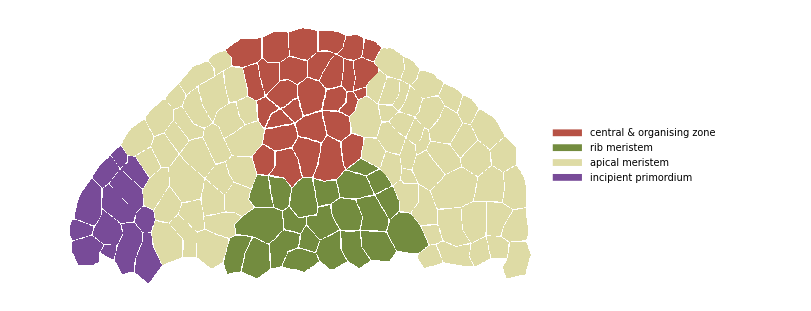

```mathematica
Txb0701SAMb1=Ch6SAMb1;
txbExport[Txb0701SAMb1]
```

```mathematica
samOnly = KeyDrop[cellPolygonPoints,czColours["Primordia"]];

b2Swatch = {Lighter[jStyle["CylinderColour"],1/2],jStyle["CylinderColour"],Darker[jStyle["CylinderColour"]]};

b2Colour[id_] := Which[
MemberQ[czLayers["L1"],id],b2Swatch[[1]],
MemberQ[czLayers["L2"],id],b2Swatch[[2]],
True,b2Swatch[[3]]
];
basepoly = Map[Polygon,samOnly];

split[pair_] := Module[{norm},
{Line[pair],Arrowheads[{-.01,.01}],GeometricTransformation[Arrow[pair],RotationTransform[90 Degree,Midpoint[Line[pair]]]]}
];

labels = KeyValueMap[Text[#1,Mean[#2]]&,samOnly];
splitPoints={ 
{{433.2,349.1},{432.6,374.2}},
{{300.2,319.4},{308.5,285.5}},
{{271.8,237.},{288.5,203.}}
};
periPoints = {
{{544.4,271.9},{564.5,261.3}}
,{{666.8,150.6},{666.8,110.5}}
};

Ch6SAMb2 := Module[{},
colouredCells = KeyValueMap[{EdgeForm[None],FaceForm[ b2Colour[#1]],Polygon[#2]}&,samOnly];
Legended[
Graphics[{
colouredCells
,{Thick,jStyle["ParastichyColour"][1],Map[split,splitPoints]}
,{Thick,jStyle["ParastichyColour"][2],Map[split,periPoints]}

},
ImageSize->600],
{SwatchLegend[b2Swatch,
Map[Style[#,FontFamily->jStyle["FontFamily"],FontSize->Scaled[0.025]]&,{"L1","L2","L3"}]
]
,LineLegend[{jStyle["ParastichyColour"][1],jStyle["ParastichyColour"][2]},
Map[Style[#,FontFamily->jStyle["FontFamily"],FontSize->Scaled[0.025]]&,{"Cell division:\nstem extension","Cell division:\ngirth expansion"}]
]
}]
];
```

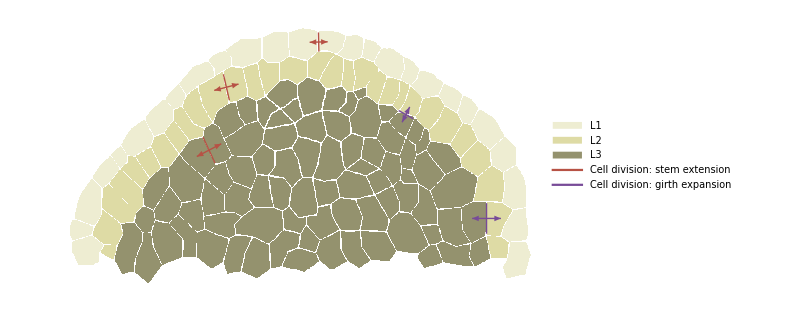

```mathematica
Txb0702SAMb2=Ch6SAMb2;
txbExport[Txb0702SAMb2]
```